```mathematica
Clear["Global`*"]
```

```mathematica
(* Subscript[先定义经常用到的式子和文献中给出的A, i]*)
raSinh[x_,h_,H_,x3_]:=Evaluate[D[Sinh[x*h]/Sinh[x*H],x]];
raSinh2[x_,h_,H_,x3_]:=Evaluate[D[Sinh[x*(H-x3)] Sinh[x*h]/Sinh[x*H],x]];
sh[x_,h_,H_,x3_]:=Sinh[x*h]/Sinh[x*H]Sinh[x*(H-x3)];
ch[x_,h_,H_,x3_]:=Sinh[x*h]/Sinh[x*H]Cosh[x*(H-x3)];

a1[x_,h_,H_,x3_]:=1/(Sinh[x*H]^2-(x*H)^2)*(
x*h*H*x3*Sinh[x*(H-x3)]Sinh[x(H-h)]
+x3(h Sinh[x H]Cosh[x(H-x3-h)]-H Sinh[x*h]Cosh[x3 x])
+x H x3 Sinh[x H]Cosh[x(H-x3)]raSinh[x,H-h,H,x3]
-H Sinh[x x3](Sinh[x*H] raSinh[x,h,H,x3]+x*H raSinh[x,H-h,H,x3])
);

a2[x_,h_,H_,x3_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
x3(H Sinh[x*h]Cosh[x x3]-h Sinh[x H]Cosh[x(H-x3-h)]
+x h H Sinh[x*(H-x3)]Sinh[x (H-h)]
+x H Cosh[x(H-x3)]Sinh[x*H] raSinh[x,H-h,H,x3])
-x*H^2 Sinh[x x3] raSinh[x,H-h,H,x3]+H Sinh[x*x3]*Sinh[x*H] raSinh[x,h,H,x3]
);

a3[x_,h_,H_,x3_]:=(Sinh[x*H]^2)^-1*
(h*Sinh[x*H]Cosh[x(H-x3-h)]-H*Sinh[x*h]Cosh[x x3]);

a4[x_,h_,H_,x3_]:=x/(Sinh[x*H]^2-(x*H)^2)*(x3 x H(h Sinh[x (x3-h)]
+H Sinh[x h]Sinh[x(H-x3)]/Sinh[x H])
-x h H^2 Sinh[x x3]Sinh[x(H-h)]/Sinh[x H]
+(-1)*(-H(H-h)Sinh[x h]Sinh[x x3]+x3(h Sinh[x H]Sinh[x(H-x3-h)]
+H Sinh[x h]Sinh[x x3])));(* For j=α,k=3*)
a4s[x_,h_,H_,x3_]:=x/(Sinh[x*H]^2-(x*H)^2)*(x3 x H(h Sinh[x (x3-h)]
+H Sinh[x h]Sinh[x(H-x3)]/Sinh[x H])
-x h H^2 Sinh[x x3]Sinh[x(H-h)]/Sinh[x H]
+(1)*(-H(H-h)Sinh[x h]Sinh[x x3]+x3(h Sinh[x H]Sinh[x(H-x3-h)]
+H Sinh[x h]Sinh[x x3])));(* For j=3,k=α*)

a5[x_,h_,H_,x3_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*Sinh[x*(H-h)]+(H-h)Sinh[x*h]Sinh[x H])Cosh[x(H-x3)]+
(Sinh[x*H] raSinh[x,h,H,x3]+x*H raSinh[x,H-h,H,x3])*Sinh[x*H]*Sinh[x*(H-x3)]
);

a6[x_,h_,H_,x3_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*Sinh[x*(H-h)]-(H-h)Sinh[x*h]Sinh[x H])Sinh[x(H-x3)]-
(Sinh[x*H] raSinh[x,h,H,x3]-x*H raSinh[x,H-h,H,x3])*Sinh[x*H]*Cosh[x*(H-x3)]
);(* 给出 h0*)
h0=1;k0=2Pi/h0;
```

```mathematica
(* 画出各个函数图像。*)
Manipulate[Plot[ f[x k0,h h0,10h0,z h0] x BesselJ[0,2Pi m x],{x,0,xm},PlotRange->All],{f,{a1,a2,a3,a4,a5,a6,sh}},{h,{1,3}},{z,{3.5,1.01,2,3.01,1}},{m,0,40,10},{xm,0.1,2/(z-h),5}]
```

```mathematica
(* 可见上述函数收敛相当快。事实上，贝塞尔函数只是提供周期性，振幅由各a决定。而a是与ρ无关的。所以，积分上限可取为定值。比如，2.*)
(* 下面定义积分式 j0sh≡-Graphics-j1xsh≡-Graphics-*)
(* j0a2≡-Graphics-   j1xa1≡-Graphics- *)
```

```mathematica
j0sh[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)2Pi x]sh[x,h,H h,x3 h],{x,0,Infinity},WorkingPrecision->15,AccuracyGoal->6,Method->{Automatic,"SymbolicProcessing"->False}];
j0xch[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x]x ch[x,h,H,x3],{x,0,400}];
j0xdsh[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x]x raSinh2[x,h,H,x3],{x,0,400},WorkingPrecision->15,AccuracyGoal->6,Method->{Automatic,"SymbolicProcessing"->False}];
j1xsh[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x]x sh[x,h,H,x3],{x,0,400},WorkingPrecision->15,AccuracyGoal->6,Method->{Automatic,"SymbolicProcessing"->False}];
j1xa1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x]x a1[x,h,H,x3],{x,0,400},Method->"GaussKronrodRule" ];
j0x2a1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x] x^2 a1[x,h,H,x3],{x,0,400},Method->{"GaussKronrodRule" }];
j0a2[r_,x3_,h_,H_]:=NIntegrate[BesselJ[0,r x]a2[x,h,H,x3],{x,0,Infinity},Method->"ExtrapolatingOscillatory"];
j1xa3[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x] x a3[x,h,H,x3],{x,0,400}];
j1xa4[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x] x a4[x,h,H,x3],{x,0,400},Method->"GaussKronrodRule"];(* For u13.*)
j1xa4s[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x] x a4s[x,h,H,x3],{x,0,400},Method->"GaussKronrodRule"];(* for u31.*)
```

```mathematica
(* 由此可以得到所有速度的表达式，when x3>h.*)
v11[r1_,r2_,x3_,h_,H_]:=j0sh[##]+r1^2/(√(r1^2+r2^2))j1xsh[##]&[r1,r2,x3,h,H];w11[r1_,r2_,x3_,h_,H_]:=j1xa1[##](r1^2-r2^2)/((√(r1^2+r2^2))^3)-r1^2/(r1^2+r2^2)j0x2a1[##]&[r1,r2,x3,h,H];
v12[r1_,r2_,x3_,h_,H_]:=(r1 r2)/(√(r1^2+r2^2))j1xsh[##]&[r1,r2,x3,h,H];w12[r1_,r2_,x3_,h_,H_]:=j1xa1[##](2r1 r2)/((√(r1^2+r2^2))^3)-(r1 r2)/(r1^2+r2^2)j0x2a1[##]&[r1,r2,x3,h,H];
v13[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xsh[##]&[r1,r2,x3,h,H];w13[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xa4[##]&[√(r1^2+r2^2),x3,h,H];(* For u13.*)
v31[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xsh[##]&[r1,r2,x3,h,H];
w31[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xa4s[##]&[r1,r2,x3,h,H];(* for u31.*)
v33[r1_,r2_,x3_,h_,H_]:=j0sh[##]-j0xdsh[##]&[√(r1^2+r2^2),x3,h,H];
w33[r1_,r2_,x3_,h_,H_]:=j0a2[##]&[√(r1^2+r2^2),x3,h,H];
```

```mathematica
u13[r1_,r2_,x3_,h_,H_]:=Piecewise[{{w13[r1,r2,x3,h,H],x3==h},{(w13[r1,r2,x3,h,H]+(x3-h)v13[r1,r2,x3,h,H]),H>x3>h},{(w13[r1,r2,x3,h,H]+(x3-h)v13[r1,r2,H-x3,H-h,H]),x3<h}}];
u23[r1_,r2_,x3_,h_,H_]:=u13[r2,r1,x3,h,H];
u33[r1_,r2_,x3_,h_,H_]:=Piecewise[{{(w33[r1,r2,x3,h,H]+v33[r1,r2,x3,h,H]),H>x3≥  h},{(w33[r1,r2,x3,h,H]+v33[r1,r2,H-x3,H-h,H]),x3<h}}];
```

```mathematica
u13[r1_,r2_,x3_,h_,H_];
```

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x^2\ « 1 »\ (H_\ (-h_ + H_)\ Sinh[x\ h_]\ Sinh[x\ x3_] - x\ Csch[x\ H_]\ h_\ H_^2\ Sinh[x\ (« 1 »)]\ Sinh[x\ x3_] - x3_\ (« 1 ») + x\ H_\ x3_\ (« 1 »))/-x^2\ H_^2 + Sinh[x\ H_]^2 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

```mathematica
(* 下面画图. 先定义初始条件。其中 r=（x）*)
n=100;h0=0.2;
xz=Table[i/n,{i,1,(3h0)n}];
```

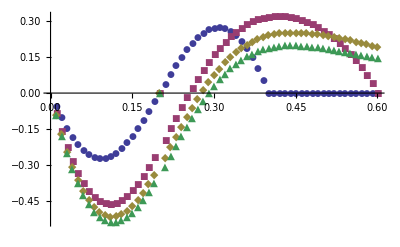

```mathematica
(* 对于 xz<h, 将 xz 换成 H-xz，将 h 换成 H-h.  Subscript[v13, 实际]=（x3-h）v13 *)
U13={};
Do[u13=Piecewise[{{(w13[h0,h0,#,h0,i h0]+(#-h0)v13[h0,h0,#,h0,i h0]),i h0>#>h0},{(w13[h0,h0,#,h0,i h0]+(#-h0)v13[h0,h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u13=Transpose@{xz,u13};U13=Append[U13,u13],{i,{2,3,4,10}}];

ListPlot[U13[[#]]&/@Range[Length@U13],PlotMarkers->Automatic]
```

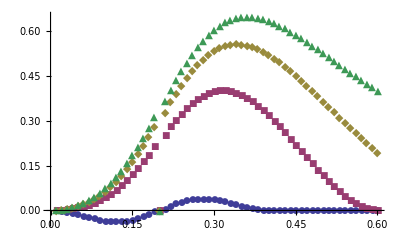

```mathematica
(* 上面u13的计算不错。计算速度u31*)
U31={};
Do[u31=Piecewise[{{(w31[h0,h0,#,h0,i h0]+(#-h0)v31[h0,h0,#,h0,i h0]),i h0>#>h0},{(w31[h0,h0,#,h0,i h0]+(#-h0)v31[h0,h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u31=Transpose@{xz,u31};U31=Append[U31,u31],{i,{2,3,4,10}}];

ListPlot[U31[[#]]&/@Range[Length@U31],PlotMarkers->Automatic]
```

NIntegrate::levmaxord: -0.16\ x\ Sinh[x/100]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + « 1 » + 1/100\ (0.4\ Cosh[x/100]\ Sinh[0.2\ x] + « 3 » + 0.4\ x\ Cosh[« 1 »]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ « 2 »\ Sinh[0.2\ x])\ Sinh[0.4\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.16\ x\ Sinh[x/100]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + « 1 » + 1/100\ (0.4\ Cosh[x/100]\ Sinh[0.2\ x] + « 3 » + 0.4\ x\ Cosh[« 1 »]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ « 2 »\ Sinh[0.2\ x])\ Sinh[0.4\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.16\ x\ Sinh[x/50]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + 0.4\ Sinh[x/50]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ « 1 »\ « 1 »\ Sinh[0.2\ x])\ Sinh[0.4\ x] + 1/50\ (0.4\ Cosh[x/50]\ Sinh[0.2\ x] + « 4 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.16\ x\ Sinh[x/50]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + 0.4\ Sinh[x/50]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ « 1 »\ « 1 »\ Sinh[0.2\ x])\ Sinh[0.4\ x] + 1/50\ (0.4\ Cosh[x/50]\ Sinh[0.2\ x] + « 4 ») 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.16\ x\ Sinh[3\ x/100]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + 0.4\ Sinh[3\ x/100]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x] + 3/100\ (« 1 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.16\ x\ Sinh[3\ x/100]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + 0.4\ Sinh[3\ x/100]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x] + 3/100\ (« 1 ») 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

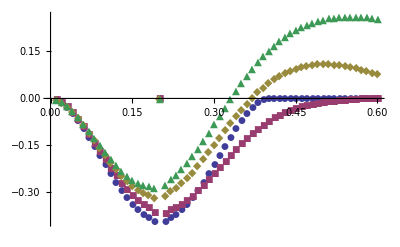

```mathematica
(* 上面u13的计算不错。计算速度u33*)
U33={};
Do[u33=Piecewise[{{(w33[h0,h0,#,h0,i h0]+v33[h0,h0,#,h0,i h0]),i h0>#>h0},{(w33[h0,h0,#,h0,i h0]+v33[h0,h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u33=Transpose@{xz,u33};U33=Append[U33,u33],{i,{2,3,4,10}}];

ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic]
```

```mathematica
ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic]
```

-Graphics-

```mathematica
(* U33 还不错。 计算 U12，r={h0,h0}.*)
U12={};
Do[u12=Piecewise[{{(w12[h0,h0,#,h0,i h0]+v12[h0,h0,#,h0,i h0]),i h0>#>h0},{(w12[h0,h0,#,h0,i h0]+v12[h0,h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u12=Transpose@{xz,u12};U12=Append[U12,u12],{i,{2,3,4,10}}];

ListPlot[U12[[#]]&/@Range[Length@U12],PlotMarkers->Automatic]
```

NIntegrate::levmaxord: 0.0008\ x\ Sinh[0.2\ x]\ Sinh[0.39\ x] + 0.004\ x\ Cosh[« 1 »]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x] + « 1 » - 0.4\ Sinh[x/100]\ (0.4\ x\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 0.0008\ x\ Sinh[0.2\ x]\ Sinh[0.39\ x] + 0.004\ x\ Cosh[« 1 »]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x] + « 1 » - 0.4\ Sinh[x/100]\ (0.4\ x\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: 0.0016\ x\ Sinh[0.2\ x]\ Sinh[0.38\ x] + 0.008\ x\ Cosh[0.38\ x]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x] + « 1 » - 0.4\ Sinh[x/50]\ (0.4\ x\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 0.0016\ x\ Sinh[0.2\ x]\ Sinh[0.38\ x] + 0.008\ x\ Cosh[0.38\ x]\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x] + « 1 » - 0.4\ Sinh[x/50]\ (0.4\ x\ (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x]) + (0.2\ Cosh[0.2\ x]\ Csch[0.4\ x] - 0.4\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.2\ x])\ Sinh[0.4\ x]) 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

ListPlot::argx: ListPlot 使用 0 个参数调用；预计有 1 个参数.

ListPlot[{},PlotMarkers→Automatic]

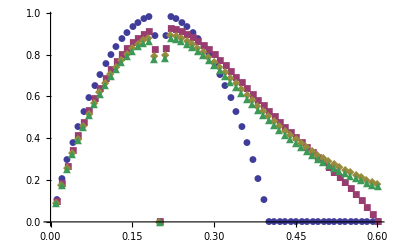

```mathematica
ListPlot[U12[[#]]&/@Range[Length@U12],PlotMarkers->Automatic]
```

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

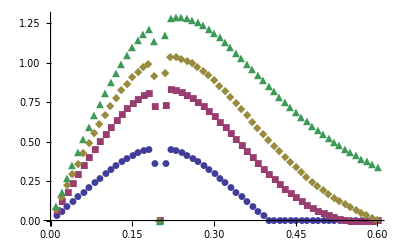

```mathematica
(*  计算 U11，r={h0,h0}.*)
U11={};
Do[u11=Piecewise[{{(w11[h0,h0,#,h0,i h0]+v11[h0,h0,#,h0,i h0]),i h0>#>h0},{(w11[h0,h0,#,h0,i h0]+v11[h0,h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u11=Transpose@{xz,u11};U11=Append[U11,u11],{i,{2,3,4,10}}];

ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic]
```

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

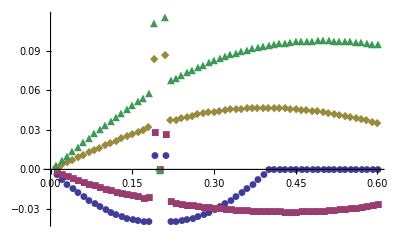

```mathematica
(* U33 还不错。 计算 U11，r={3h0,4h0}.*)
U11={};
Do[u11=Piecewise[{{(w11[3h0,4h0,#,h0,i h0]+v11[3h0,4h0,#,h0,i h0]),i h0>#>h0},{(w11[3h0,4h0,#,h0,i h0]+v11[3h0,4h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u11=Transpose@{xz,u11};U11=Append[U11,u11],{i,{2,4,8,16}}];

ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic]
```

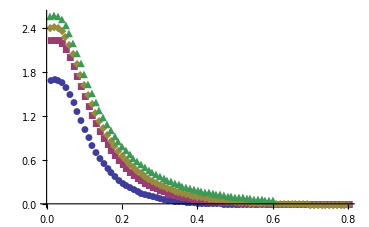

```mathematica
(* 计算 U11在水平方向的变化 r=(x,x)，x3=0.5h .*)
r=With[{m=100},Table[i/m,{i,1,(4h0)m}]];
U11={};
Do[u11=(w11[#,#,0.5h0,h0,i h0]+v11[#,#,i h0-0.5h0,i h0-h0,i h0])&/@r;
u11=Transpose@{r,u11};U11=Append[U11,u11],{i,{2,3,4,10}}];

ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic]
```

```mathematica
Length[U11[[1]]]
```

1

```mathematica
(* 下面均以 h 作为长度单位。因此，输入的（r1，r2,x3）代表 （r1*h, r2*h, x3*h）*)
(* 引入倒格矢 k=2Pi/h。λ=k η. *)
(* j0shNh = j0sh nature height*)
```

```mathematica
(* 在定义函数时，注意 h 是一个动态变量。在 x<h 和 x>h 的情况下，h 的取值是不同的。但是，作为长度单位的 h 是不能改变的。所以，在下面函数定义中，我们引入了局部变量 h0 来作为长度单位。因此，程序运行前，都要先给定一个 h0.*)
(* 对于无 a 项， 积分上限取为无穷，但流场在 z 方向以指数衰减，因此远场可以将积分上限下调。*)
(*For v11 and v33.*)
xn=9;
j0shNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=(2Pi)/(h0 √(r1^2+r2^2))},NIntegrate[k BesselJ[0,2Pi x]sh[x k,h h0,H h0,x3 h0],{x,0,Infinity}]]]
j0shNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},If[x3<1.1h,j0shNhNearh[r1,r2,x3,h,H],With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=xn(√(r1^2+r2^2))/(x3-h)},NIntegrate[k BesselJ[0,2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]]];

(*For v33*)
j0xdshNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2))},NIntegrate[k BesselJ[0,2Pi x]k x raSinh2[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]];
j0xdshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},If[x3<1.1h,j0xdshNhNearh[r1,r2,x3,h,H],With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=xn(√(r1^2+r2^2))/(x3-h)},NIntegrate[k BesselJ[0,2Pi x]k x raSinh2[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]]];

j1xshNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2))},NIntegrate[k BesselJ[1,2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]];
j1xshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=xn(√(r1^2+r2^2))/(x3-h)},If[x3<1.1h,j1xshNhNearh[r1,r2,x3,h,H],NIntegrate[k BesselJ[1,2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]]];

(* 由于 a1 在 r->∞ 时以 E^(-(x+h)y/ρ) 趋向于 0, 选取 10^-4 作为截断值, 
得到 ylim = (4 Log[10] ρ)/(x+h)=(9.2 ρ)/(x+h). *)
j1xa1Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0,xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k/(√(r1^2+r2^2)) BesselJ[1,2Pi x] k/(√(r1^2+r2^2)) x a1[x k/(√(r1^2+r2^2)) ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential" ]]];

j0x2a1Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[0,2Pi x](k x)^2 a1[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]]; 

j0a2Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[0,2Pi x]a2[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]];

(* 约化后的 Green function 与 a3 无关 *)
(*j1xa3Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[1,2Pi x] k x a3[x k ,h h0,H h0,x3 h0],{x,0,xlim}]]];*)

j1xa4Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h) },NIntegrate[k BesselJ[1,2Pi x] k x a4[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]];
(* For u13.*)

j1xa4sNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2 Pi/(h0 √(r1^2+r2^2)),xlim=9(√(r1^2+r2^2))/(x3+h)},NIntegrate[k BesselJ[1,2Pi x] k x a4s[x k ,h h0,H h0,x3 h0],{x,0,xlim},Method->"DoubleExponential"]]];
(* For u31.*)
```

```mathematica
(* 由此可以得到所有速度的表达式，when x3>h.*)
v11Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},j0shNh[##]+(r1^2 h0)/(√(r1^2+r2^2))j1xshNh[##]&[r1,r2,x3,h,H]];w11Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},j1xa1Nh[##](r1^2-r2^2)/((√(r1^2+r2^2))^3)( h0)^-1-r1^2/(r1^2+r2^2)j0x2a1Nh[##]&[r1,r2,x3,h,H]];

v12Nh[r1_,r2_,x3_,h_,H_]:=(r1 r2)/(√(r1^2+r2^2))j1xshNh[##]&[r1,r2,x3,h,H];w12Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},j1xa1Nh[##](2r1 r2)/((√(r1^2+r2^2))^3)( h0)^-1-(r1 r2)/(r1^2+r2^2)j0x2a1Nh[##]&[r1,r2,x3,h,H]];
v13Nh[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xshNh[##]&[r1,r2,x3,h,H];w13Nh[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xa4Nh[##]&[r1,r2,x3,h,H];(* For u13.*)

v31Nh[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xshNh[##]&[r1,r2,x3,h,H];
w31Nh[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xa4sNh[##]&[r1,r2,x3,h,H];(* for u31.*)

v33Nh[r1_,r2_,x3_,h_,H_]:=j0shNh[##]-j0xdshNh[##]&[r1,r2,x3,h,H];
w33Nh[r1_,r2_,x3_,h_,H_]:=j0a2Nh[##]&[r1,r2,x3,h,H];
```

```mathematica
u11Nh[r1_,r2_,x3_,h_,H_]:=Piecewise[{
{(w11Nh[r1,r2,x3,h,H]+v11Nh[r1,r2,x3,h,H]),H>x3≥  h},{(w11Nh[r1,r2,x3,h,H]+v11Nh[r1,r2,H-x3,H-h,H]),x3<h}}];
u22Nh[r1_,r2_,x3_,h_,H_]:=u11Nh[r2,r1,x3,h,H];

u12Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},Piecewise[{
{(w12Nh[r1,r2,x3,h,H]+v12Nh[r1,r2,x3,h,H]),H>x3≥  h},{(w12Nh[r1,r2,x3,h,H]+v12Nh[r1,r2,H-x3,H-h,H]),x3<h}}]];
u21Nh[r1_,r2_,x3_,h_,H_]:=u12Nh[r2,r1,x3,h,H];

u13Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},Piecewise[{
{w13Nh[r1,r2,x3,h,H],x3==1},
{(w13Nh[r1,r2,x3,h,H]+(x3-h)h0 v13Nh[r1,r2,x3,h,H]),H>x3> h},{(w13Nh[r1,r2,x3,h,H]+(x3-h)h0 v13Nh[r1,r2,H-x3,H-h,H]),x3<h}}]];
u23Nh[r1_,r2_,x3_,h_,H_]:=u13Nh[r2,r1,x3,h,H];

u31Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},Piecewise[{{w31Nh[r1,r2,x3,h,H],x3==1},{(w31Nh[r1,r2,x3,h,H]+(x3-h)h0 v31Nh[r1,r2,x3,h,H]),H>x3> h},{(w31Nh[r1,r2,x3,h,H]+(x3-h)h0 v31Nh[r1,r2,H-x3,H-h,H]),x3<h}}]];
u32Nh[r1_,r2_,x3_,h_,H_]:=u31Nh[r2,r1,x3,h,H];

u33Nh[r1_,r2_,x3_,h_,H_]:=Piecewise[{{(w33Nh[r1,r2,x3,h,H]+v33Nh[r1,r2,x3,h,H]),H>x3≥  h},{(w33Nh[r1,r2,x3,h,H]+v33Nh[r1,r2,H-x3,H-h,H]),x3<h}}];
```

```mathematica
(* 下面开始在 Nh 条件下画图.*)
(* r=(h0, h0, x3)=(1,1,x3) H=4h. h=h0=0.2*)
h0=1;k0=2Pi/h0;
xz=With[{n=20},Table[N[i],{i,1/n,3,1/n}]];
```

NIntegrate::ncvb: 在接近 {x} = {0.0525126} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -9.88716×10^-19 和 4.42398×10^-19.

i=2

i=3

i=4

i=10

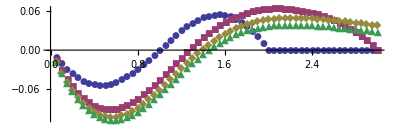

```mathematica
U13={};
Do[uu13=u13Nh[1,1,#,1,i]&/@xz;
uu13=Transpose@{xz,uu13};U13=Append[U13,uu13];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U13[[#]]&/@Range[Length@U13],PlotMarkers->Automatic,AspectRatio->1/3]
```

i=2

i=3

i=4

i=10

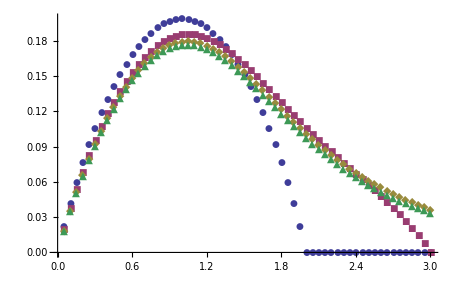

```mathematica
U12={};
Do[uu12=u12Nh[1,1,#,1,i]&/@xz;
uu12=Transpose@{xz,uu12};U12=Append[U12,uu12];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U12[[#]]&/@Range[Length@U12],PlotMarkers->Automatic]
```

i=2

i=3

i=4

i=10

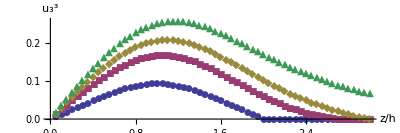

```mathematica
(* r=(1,1) *)
U11={};
Do[uu11=u11Nh[1,1,#,1,i]&/@xz;
uu11=Transpose@{xz,uu11};U11=Append[U11,uu11];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic,AxesLabel->{"z/h","u_3^3"},PlotLegends->Placed[{"H=2","H=3","H=4","H=10"},Above],AspectRatio->1/3]
```

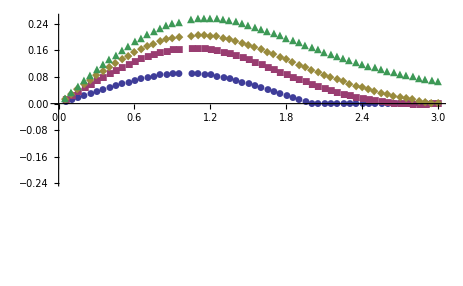

i=2

i=3

i=4

i=10

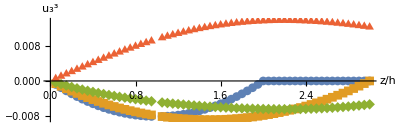

```mathematica
(* r=(3,4) *)
U11={};
Do[uu11=u11Nh[3,4,#,1,i]&/@xz;
uu11=Transpose@{xz,uu11};U11=Append[U11,uu11];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic,AxesLabel->{"z/h","u_3^3"},PlotLegends->Placed[{"H=2","H=3","H=4","H=10"},Above],AspectRatio->1/3]
```

```mathematica
ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic]
```

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

i=2

i=3

i=4

i=10

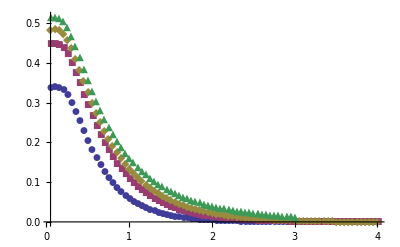

```mathematica
(* 固定 x3=0.5h, 在 r=(x,x) 上，画出流场图。*)
r=With[{m=20},Table[i,{i,1/m,4,1/m}]];
U11={};
Do[uu11rNh=(w11Nh[#,#,0.5,1,i ]+v11Nh[#,#,i -0.5,i -1,i ])&/@r;
uu11rNh=Transpose@{r,uu11rNh};U11=Append[U11,uu11rNh];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U11[[#]]&/@Range[Length@U11],PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
U31={};
Do[uu31=u31Nh[1,1,#,1,i]&/@xz;
uu31=Transpose@{xz,uu31};U31=Append[U31,uu31];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U31[[#]]&/@Range[Length@U31],PlotMarkers->Automatic,AspectRatio->1/3,AxesLabel->{"z/h","u_3^3"},PlotLegends->{"H=2","H=3","H=4","H=10"}]
```

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

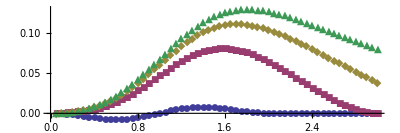

i=2

i=3

i=4

i=10

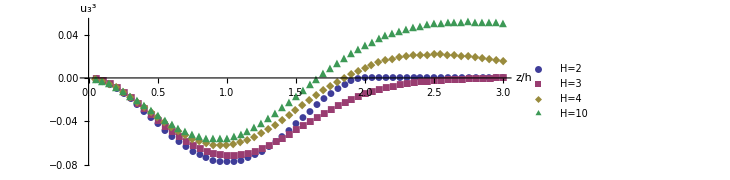

```mathematica
U33={};
Do[uu33=u33Nh[1,1,#,1,i]&/@xz;
uu33=Transpose@{xz,uu33};U33=Append[U33,uu33];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic,AspectRatio->1/3,AxesLabel->{"z/h","u_3^3"},PlotLegends->Placed[{"H=2","H=3","H=4","H=10"},Above]]
```

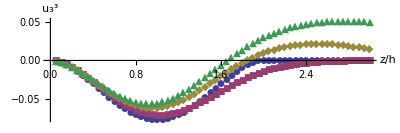

```mathematica
ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic,AspectRatio->1/3,AxesLabel->{"z/h","u_3^3"},PlotLegends->Placed[{"H=2","H=3","H=4","H=10"},Above]]
```

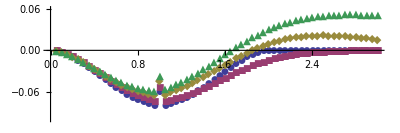

```mathematica
ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic,AspectRatio->1/3,PlotRange->{-0.1,0.06}]
```

```mathematica
(* 下面就要做 ∇·u=0 的截断误差分析。*)
```

```mathematica
(* 先给出格点坐标。dx=dy=dz=1/m=1/20.*)
xline=With[{m=20.0},Table[i,{i,1/m,4,1/m}]];
yline=With[{m=20.0},Table[i,{i,1/m,4,1/m}]];
zline=With[{m=20.0},Table[i,{i,1/m,4,1/m}]];
```

```mathematica
(* 注意到 x 与 y 的任意性，我们只需专注于两个方向：z 方向和 x 方向。*)
(* 首先是 x 方向的力产生的流场.*)
gradU1[x_,y_,z_,h_,H_,dx_,dy_,dz_]:=
(u11Nh[x+dx/2,y,z,h,H]-u11Nh[x-dx/2,y,z,h,H])/dx+
(u21Nh[x,y+dy/2,z,h,H]-u21Nh[x,y-dy/2,z,h,H])/dy+
(u31Nh[x,y,z+dz/2,h,H]-u31Nh[x,y,z-dz/2,h,H])/dz;
```

```mathematica
With[{m=100.0},With[{dx=1/m,dy=1/m,dz=1/m},R1z=ParallelMap[gradU1[2,2,#,1,4,dx,dy,dz]&,zline];R1z=Transpose@{zline,R1z}]]
```

NIntegrate::levmaxord: 1.25664\ x\ Sinh[24.8186\ x]\ Sinh[6\ π\ x] + 1.25664\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] « 1 » « 1 » - 4\ Sinh[0.314159\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 1.25664\ x\ Sinh[24.8186\ x]\ Sinh[6\ π\ x] + 1.25664\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] « 1 » « 1 » - 4\ Sinh[0.314159\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: 13.823\ x\ Sinh[21.677\ x]\ Sinh[6\ π\ x] + 13.823\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[3.45575\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 13.823\ x\ Sinh[21.677\ x]\ Sinh[6\ π\ x] + 13.823\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[3.45575\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: 1.25664\ x\ Sinh[24.8186\ x]\ Sinh[6\ π\ x] + 1.25664\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] « 1 » « 1 » - 4\ Sinh[0.314159\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 1.25664\ x\ Sinh[24.8186\ x]\ Sinh[6\ π\ x] + 1.25664\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] « 1 » « 1 » - 4\ Sinh[0.314159\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: 13.823\ x\ Sinh[21.677\ x]\ Sinh[6\ π\ x] + 13.823\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[3.45575\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 13.823\ x\ Sinh[21.677\ x]\ Sinh[6\ π\ x] + 13.823\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[3.45575\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: 1.25664\ x\ Sinh[24.8186\ x]\ Sinh[6\ π\ x] + 1.25664\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] « 1 » « 1 » - 4\ Sinh[0.314159\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 1.25664\ x\ Sinh[24.8186\ x]\ Sinh[6\ π\ x] + 1.25664\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] « 1 » « 1 » - 4\ Sinh[0.314159\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: 13.823\ x\ Sinh[21.677\ x]\ Sinh[6\ π\ x] + 13.823\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[3.45575\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 13.823\ x\ Sinh[21.677\ x]\ Sinh[6\ π\ x] + 13.823\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[3.45575\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 26.3894\ x\ Sinh[18.5354\ x]\ Sinh[6\ π\ x] + 26.3894\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[6.59734\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 26.3894\ x\ Sinh[18.5354\ x]\ Sinh[6\ π\ x] + 26.3894\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[6.59734\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 12 recursive bisections in x near {x} = {0.559968}. NIntegrate obtained 0.0245574 and 3.43082×10^-14 for the integral and error estimates.

NIntegrate::levmaxord: 38.9557\ x\ Sinh[15.3938\ x]\ Sinh[6\ π\ x] + 38.9557\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[9.73894\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 38.9557\ x\ Sinh[15.3938\ x]\ Sinh[6\ π\ x] + 38.9557\ x\ « 1 »\ (« 1 » - « 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[9.73894\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 51.5221\ x\ Sinh[12.2522\ x]\ Sinh[6\ π\ x] + « 4 » is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 51.5221\ x\ Sinh[12.2522\ x]\ Sinh[6\ π\ x] + « 4 » as a non-Levin function.

NIntegrate::levmaxord: 64.0885\ x\ Sinh[9.11062\ x]\ Sinh[6\ π\ x] + 64.0885\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[16.0221\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 64.0885\ x\ Sinh[9.11062\ x]\ Sinh[6\ π\ x] + 64.0885\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[16.0221\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: 51.5221\ x\ Sinh[12.2522\ x]\ Sinh[6\ π\ x] + « 4 » is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 51.5221\ x\ Sinh[12.2522\ x]\ Sinh[6\ π\ x] + « 4 » as a non-Levin function.

NIntegrate::levmaxord: 64.0885\ x\ Sinh[9.11062\ x]\ Sinh[6\ π\ x] + 64.0885\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[16.0221\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 64.0885\ x\ Sinh[9.11062\ x]\ Sinh[6\ π\ x] + 64.0885\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[16.0221\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 64.0885\ x\ Sinh[9.11062\ x]\ Sinh[6\ π\ x] + 64.0885\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[16.0221\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 64.0885\ x\ Sinh[9.11062\ x]\ Sinh[6\ π\ x] + 64.0885\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[16.0221\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 76.6549\ x\ Sinh[5.96903\ x]\ Sinh[6\ π\ x] + 76.6549\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[19.1637\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 76.6549\ x\ Sinh[5.96903\ x]\ Sinh[6\ π\ x] + 76.6549\ x\ Cosh[« 1 »]\ (« 1 »)\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[19.1637\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 89.2212\ x\ Sinh[2.82743\ x]\ Sinh[6\ π\ x] + 89.2212\ « 3 »\ Sinh[8\ π\ x] + 3.55\ (« 1 ») - 4\ Sinh[22.3053\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 89.2212\ x\ Sinh[2.82743\ x]\ Sinh[6\ π\ x] + 89.2212\ « 3 »\ Sinh[8\ π\ x] + 3.55\ (« 1 ») - 4\ Sinh[22.3053\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

{{0.05,-1.51248×10^-7},{0.1,-1.29756×10^-7},{0.15,-1.10593×10^-7},{0.2,-8.91452×10^-8},{0.25,-6.6333×10^-8},{0.3,-3.81103×10^-8},{0.35,1.11745×10^-8},{0.4,-6.72777×10^-7},{0.45,1.66758×10^-7},{0.5,5.63144×10^-7},{0.55,1.88566×10^-6},{0.6,6.3915×10^-6},{0.65,-1.91804×10^-6},{0.7,-4.03739×10^-6},{0.75,1.35712×10^-7},{0.8,4.38186×10^-7},{0.85,6.38732×10^-7},{0.9,0.000273777},{0.95,0.147248},{1.,78.8209},{1.05,0.147248},{1.1,0.000273818},{1.15,7.00767×10^-7},{1.2,5.21441×10^-7},{1.25,2.71136×10^-6},{1.3,-3.90977×10^-6},{1.35,-1.7673×10^-6},{1.4,6.56586×10^-6},{1.45,2.08186×10^-6},{1.5,7.87682×10^-7},{1.55,4.16902×10^-7},{1.6,1.64008×10^-6},{1.65,3.13884×10^-7},{1.7,2.90966×10^-7},{1.75,2.89497×10^-7},{1.8,2.9262×10^-7},{1.85,2.98848×10^-7},{1.9,3.00923×10^-7},{1.95,7.57547×10^-7},{2.,5.28847×10^-7},{2.05,4.15211×10^-7},{2.1,4.13427×10^-7},{2.15,3.5384×10^-7},{2.2,3.25581×10^-7},{2.25,3.11422×10^-7},{2.3,3.03358×10^-7},{2.35,2.97774×10^-7},{2.4,2.93061×10^-7},{2.45,2.88519×10^-7},{2.5,2.83883×10^-7},{2.55,2.79068×10^-7},{2.6,2.74075×10^-7},{2.65,2.46839×10^-7},{2.7,2.63827×10^-7},{2.75,2.58048×10^-7},{2.8,2.53108×10^-7},{2.85,2.48099×10^-7},{2.9,2.43121×10^-7},{2.95,2.38245×10^-7},{3.,2.33529×10^-7},{3.05,2.29007×10^-7},{3.1,2.24705×10^-7},{3.15,2.20691×10^-7},{3.2,2.16847×10^-7},{3.25,2.13226×10^-7},{3.3,2.09804×10^-7},{3.35,2.06554×10^-7},{3.4,2.01721×10^-7},{3.45,2.00359×10^-7},{3.5,1.97322×10^-7},{3.55,1.94214×10^-7},{3.6,1.90944×10^-7},{3.65,1.87407×10^-7},{3.7,1.83484×10^-7},{3.75,1.7904×10^-7},{3.8,1.73923×10^-7},{3.85,1.67968×10^-7},{3.9,1.60987×10^-7},{3.95,1.52778×10^-7},{4.,-0.0000491115}}

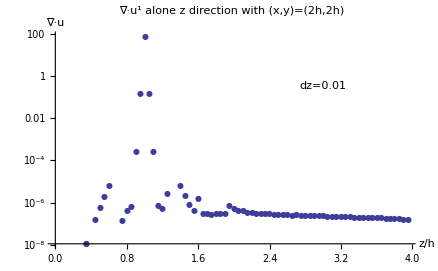

```mathematica
ListLogPlot[R1z,PlotRange->All,PlotMarkers->{Automatic,8},AxesLabel->{"z/h","∇·u^1"},PlotLegends->Placed[Text[Style["dz=0.01",13]],{0.75,0.75}],LabelStyle->Directive[12],PlotLabel->Text[Style["∇·u^1 alone z direction with (x,y)=(2h,2h)",FontFamily->"Times",14]]]
```

```mathematica
(* 考察 x 方向上的残差。取 z=2h. *)
With[{m=100.0},With[{dx=1/m,dy=1/m,dz=1/m},R1x=ParallelMap[gradU1[#,2,2,1,4,dx,dy,dz]&,xline];R1x=Transpose@{zline,R1x}]]
```

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

{{0.05,-5.40704×10^-8},{0.1,-1.06734×10^-7},{0.15,-1.56639×10^-7},{0.2,-2.02537×10^-7},{0.25,-2.43331×10^-7},{0.3,-2.78118×10^-7},{0.35,-3.06212×10^-7},{0.4,-3.27175×10^-7},{0.45,-3.40817×10^-7},{0.5,-3.47201×10^-7},{0.55,-3.46621×10^-7},{0.6,-3.39574×10^-7},{0.65,-3.94092×10^-7},{0.7,-3.0412×10^-7},{0.75,-2.77918×10^-7},{0.8,-2.47719×10^-7},{0.85,-2.31706×10^-7},{0.9,-1.99916×10^-7},{0.95,-1.65292×10^-7},{1.,-1.27544×10^-7},{1.05,-7.69947×10^-8},{1.1,-4.08563×10^-8},{1.15,-1.66076×10^-8},{1.2,1.87129×10^-8},{1.25,1.1622×10^-7},{1.3,1.69503×10^-7},{1.35,2.17089×10^-7},{1.4,2.53258×10^-7},{1.45,2.73689×10^-7},{1.5,3.69693×10^-7},{1.55,2.55579×10^-7},{1.6,2.21753×10^-7},{1.65,1.82541×10^-7},{1.7,1.52117×10^-7},{1.75,1.45471×10^-7},{1.8,-6.40484×10^-8},{1.85,2.41652×10^-7},{1.9,3.39371×10^-7},{1.95,4.46145×10^-7},{2.,5.28847×10^-7},{2.05,5.57657×10^-7},{2.1,5.09201×10^-7},{2.15,3.83224×10^-7},{2.2,2.05152×10^-7},{2.25,2.4363×10^-8},{2.3,-9.9513×10^-8},{2.35,-1.13882×10^-7},{2.4,4.945×10^-12},{2.45,2.19188×10^-7},{2.5,4.77121×10^-7},{2.55,6.77909×10^-7},{2.6,7.49894×10^-7},{2.65,6.34552×10^-7},{2.7,3.54413×10^-7},{2.75,7.89798×10^-9},{2.8,-3.29943×10^-7},{2.85,-4.90713×10^-7},{2.9,1.60554×10^-7},{2.95,-1.25592×10^-7},{3.,3.11148×10^-7},{3.05,4.5804×10^-7},{3.1,9.05582×10^-7},{3.15,8.4771×10^-7},{3.2,6.32882×10^-6},{3.25,2.17427×10^-8},{3.3,-4.64022×10^-7},{3.35,-7.57495×10^-7},{3.4,2.59219×10^-6},{3.45,7.11058×10^-8},{3.5,-1.55637×10^-6},{3.55,6.62797×10^-7},{3.6,9.96508×10^-7},{3.65,8.9482×10^-7},{3.7,6.36228×10^-7},{3.75,7.64641×10^-8},{3.8,-5.38962×10^-7},{3.85,-1.09389×10^-6},{3.9,-9.38036×10^-7},{3.95,-5.80872×10^-7},{4.,2.16349×10^-8}}

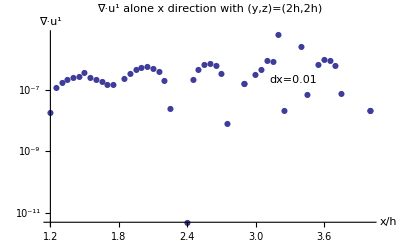

```mathematica
ListLogPlot[R1x,PlotRange->All,PlotMarkers->{Automatic,8},AxesLabel->{"x/h","∇·u^1"},PlotLegends->Placed[Text[Style["dx=0.01",13]],{0.75,0.75}],LabelStyle->Directive[12],PlotLabel->Text[Style["∇·u^1 alone x direction with (y,z)=(2h,2h)",FontFamily->"Times",14]]]
```

```mathematica
(* 其次是 z 方向的力产生的流场.*)
gradU3[x_,y_,z_,h_,H_,dx_,dy_,dz_]:=
(u13Nh[x+dx/2,y,z,h,H]-u13Nh[x-dx/2,y,z,h,H])/dx+
(u23Nh[x,y+dy/2,z,h,H]-u23Nh[x,y-dy/2,z,h,H])/dy+
(u33Nh[x,y,z+dz/2,h,H]-u33Nh[x,y,z-dz/2,h,H])/dz;
```

```mathematica
With[{m=100.0},With[{dx=1/m,dy=1/m,dz=1/m},R3z=ParallelMap[gradU3[2,2,#,1,4,dx,dy,dz]&,zline];R3z=Transpose@{zline,R3z}]]
```

NIntegrate::levmaxord: -32\ π\ x\ Sinh[3.48717\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.555\ (4\ Cosh[3.48717\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[21.6456\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[3.48717\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.555\ (4\ Cosh[3.48717\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[21.6456\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[0.345575\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.055\ (4\ Cosh[0.345575\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[24.7872\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[0.345575\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.055\ (4\ Cosh[0.345575\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[24.7872\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[0.282743\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.045\ (4\ Cosh[0.282743\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[24.85\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[0.282743\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.045\ (4\ Cosh[0.282743\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[24.85\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[3.42434\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.545\ (4\ Cosh[3.42434\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[21.7084\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[3.42434\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.545\ (4\ Cosh[3.42434\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[21.7084\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[0.659734\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.105\ (4\ Cosh[0.659734\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[24.473\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[0.659734\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.105\ (4\ Cosh[0.659734\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[24.473\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[3.80133\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.605\ (4\ Cosh[3.80133\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[21.3314\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[3.80133\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 0.605\ (4\ Cosh[3.80133\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[21.3314\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[6.62876\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.055\ (4\ Cosh[6.62876\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[18.504\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[6.62876\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.055\ (4\ Cosh[6.62876\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[18.504\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[6.56593\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[6.56593\ x]\ (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x] + 1.045\ (« 1 ») is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[6.56593\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[6.56593\ x]\ (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x] + 1.045\ (« 1 ») as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[9.77035\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.555\ (4\ Cosh[9.77035\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[15.3624\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[9.77035\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.555\ (4\ Cosh[9.77035\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[15.3624\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[9.70752\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[9.70752\ x]\ (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x] + 1.545\ (« 1 ») is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[9.70752\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[9.70752\ x]\ (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x] + 1.545\ (« 1 ») as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[6.94292\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.105\ (4\ Cosh[6.94292\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[18.1898\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[6.94292\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.105\ (4\ Cosh[6.94292\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[18.1898\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[10.0845\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.605\ (4\ Cosh[10.0845\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[15.0482\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[10.0845\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 1.605\ (4\ Cosh[10.0845\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[15.0482\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[12.9119\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.055\ (4\ Cosh[12.9119\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[12.2208\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[12.9119\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.055\ (4\ Cosh[12.9119\ x]\ Sinh[2\ π\ x] + « 1 » - « 1 » + 8\ π\ x\ Cosh[12.2208\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[12.8491\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.045\ (4\ Cosh[12.8491\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[12.2836\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[12.8491\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.045\ (4\ Cosh[12.8491\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[12.2836\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[16.0535\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.555\ (4\ Cosh[16.0535\ x]\ Sinh[2\ π\ x] + 8\ « 4 » - « 1 » + 8\ π\ x\ Cosh[9.0792\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[16.0535\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.555\ (4\ Cosh[16.0535\ x]\ Sinh[2\ π\ x] + 8\ « 4 » - « 1 » + 8\ π\ x\ Cosh[9.0792\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[13.2261\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.105\ (4\ Cosh[13.2261\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[11.9066\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[13.2261\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.105\ (4\ Cosh[13.2261\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[11.9066\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[15.9907\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.545\ (4\ Cosh[15.9907\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[9.14203\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[15.9907\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.545\ (4\ Cosh[15.9907\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[9.14203\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[16.3677\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.605\ (4\ Cosh[16.3677\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[8.76504\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[16.3677\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 2.605\ (4\ Cosh[16.3677\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[8.76504\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[19.1951\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.055\ (4\ Cosh[19.1951\ x]\ Sinh[2\ π\ x] + 8\ « 4 » - « 1 » + 8\ π\ x\ Cosh[5.93761\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[19.1951\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.055\ (4\ Cosh[19.1951\ x]\ Sinh[2\ π\ x] + 8\ « 4 » - « 1 » + 8\ π\ x\ Cosh[5.93761\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[19.1323\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.045\ (4\ Cosh[19.1323\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[6.00044\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[19.1323\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.045\ (4\ Cosh[19.1323\ x]\ Sinh[2\ π\ x] + 8\ π\ x\ « 1 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[6.00044\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[22.3367\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.555\ (4\ Cosh[22.3367\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ « 1 » - « 1 » + 8\ π\ x\ Cosh[2.79602\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[22.3367\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.555\ (4\ Cosh[22.3367\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ « 1 » - « 1 » + 8\ π\ x\ Cosh[2.79602\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[22.2739\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.545\ (4\ Cosh[22.2739\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[2.85885\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[22.2739\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + « 1 » + 3.545\ (4\ Cosh[22.2739\ x]\ Sinh[2\ π\ x] + 8\ « 3 »\ Sinh[6\ π\ x] - « 1 » + 8\ π\ x\ Cosh[2.85885\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[19.5093\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ « 2 »\ Sinh[8\ π\ x] + 3.105\ (4\ Cosh[19.5093\ x]\ Sinh[2\ π\ x] + « 3 » + 8\ π\ x\ Cosh[5.62345\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[19.5093\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ « 2 »\ Sinh[8\ π\ x] + 3.105\ (4\ Cosh[19.5093\ x]\ Sinh[2\ π\ x] + « 3 » + 8\ π\ x\ Cosh[5.62345\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[22.6509\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ « 2 »\ Sinh[8\ π\ x] + 3.605\ (4\ Cosh[22.6509\ x]\ Sinh[2\ π\ x] + « 3 » + 8\ π\ x\ Cosh[2.48186\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating -32\ π\ x\ Sinh[22.6509\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ « 2 »\ Sinh[8\ π\ x] + 3.605\ (4\ Cosh[22.6509\ x]\ Sinh[2\ π\ x] + « 3 » + 8\ π\ x\ Cosh[2.48186\ x]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

{{0.05,2.7146×10^-7},{0.1,2.93833×10^-7},{0.15,3.12919×10^-7},{0.2,3.32917×10^-7},{0.25,3.67848×10^-7},{0.3,4.63962×10^-7},{0.35,7.74137×10^-7},{0.4,1.98751×10^-6},{0.45,5.14033×10^-6},{0.5,0.0000159352},{0.55,0.0000503691},{0.6,0.000158591},{0.65,0.000437159},{0.7,0.00130246},{0.75,0.00373244},{0.8,0.0100898},{0.85,0.0246037},{0.9,0.047607},{0.95,0.0254811},{1.,4.78128×10^-8},{1.05,-0.025481},{1.1,-0.0476069},{1.15,-0.0246036},{1.2,-0.0100897},{1.25,-0.00373202},{1.3,-0.00130234},{1.35,-0.000437021},{1.4,-0.000158456},{1.45,-0.0000502113},{1.5,-0.0000157674},{1.55,-4.96329×10^-6},{1.6,-1.16744×10^-6},{1.65,-5.81857×10^-7},{1.7,-2.68786×10^-7},{1.75,-1.71317×10^-7},{1.8,-1.38109×10^-7},{1.85,-1.22965×10^-7},{1.9,-1.13592×10^-7},{1.95,2.28736×10^-7},{2.,2.91279×10^-8},{2.05,-4.11194×10^-8},{2.1,-3.72819×10^-8},{2.15,-4.71357×10^-8},{2.2,-4.34294×10^-8},{2.25,-3.4282×10^-8},{2.3,-1.85049×10^-8},{2.35,-1.23884×10^-8},{2.4,-2.48039×10^-10},{2.45,1.08741×10^-8},{2.5,2.11841×10^-8},{2.55,3.07222×10^-8},{2.6,3.94591×10^-8},{2.65,3.42562×10^-8},{2.7,5.41378×10^-8},{2.75,6.19879×10^-8},{2.8,6.66868×10^-8},{2.85,7.03573×10^-8},{2.9,7.29862×10^-8},{2.95,7.45505×10^-8},{3.,7.50259×10^-8},{3.05,7.43859×10^-8},{3.1,7.26045×10^-8},{3.15,6.96576×10^-8},{3.2,6.54852×10^-8},{3.25,6.01286×10^-8},{3.3,5.35326×10^-8},{3.35,4.56714×10^-8},{3.4,3.48388×10^-8},{3.45,2.60827×10^-8},{3.5,1.42711×10^-8},{3.55,1.08799×10^-9},{3.6,-1.34935×10^-8},{3.65,-2.94988×10^-8},{3.7,-4.69515×10^-8},{3.75,-6.58719×10^-8},{3.8,-8.62753×10^-8},{3.85,-1.0817×10^-7},{3.9,-1.31557×10^-7},{3.95,-1.56422×10^-7},{4.,0.0000331606}}

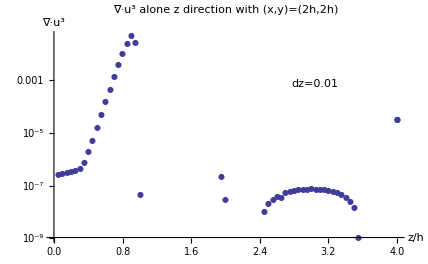

```mathematica
ListLogPlot[R3z,PlotRange->All,PlotMarkers->{Automatic,8},AxesLabel->{"z/h","∇·u^3"},PlotLegends->Placed[Text[Style["dz=0.01",13]],{0.75,0.75}],LabelStyle->Directive[12],PlotLabel->Text[Style["∇·u^3 alone z direction with (x,y)=(2h,2h)",FontFamily->"Times",14]]]
```

```mathematica
(* 考察 x 方向上的残差。*)
With[{m=100.0},With[{dx=1/m,dy=1/m,dz=1/m},R3x=ParallelMap[gradU2[#,2,2,1,4,dx,dy,dz]&,xline];R3x=Transpose@{zline,R3x}]]
```

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

NIntegrate::levmaxord: 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) is a Levin function of differential order 52 which exceeds value of option "MaxOrder" -> 50. Treating 16\ π\ x\ Sinh[4\ π\ x]\ Sinh[6\ π\ x] + 16\ π\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + 2\ « 1 » - 4\ Sinh[4\ π\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) as a non-Levin function.

General::stop: Further output of NIntegrate :: levmaxord will be suppressed during this calculation.

{{0.05,-1.48098×10^-7},{0.1,-1.33664×10^-7},{0.15,-1.10099×10^-7},{0.2,-7.81214×10^-8},{0.25,-3.87025×10^-8},{0.3,6.96778×10^-9},{0.35,5.75203×10^-8},{0.4,1.11456×10^-7},{0.45,1.67198×10^-7},{0.5,2.23151×10^-7},{0.55,2.77768×10^-7},{0.6,3.29622×10^-7},{0.65,1.70511×10^-7},{0.7,4.33757×10^-7},{0.75,4.80902×10^-7},{0.8,5.22195×10^-7},{0.85,5.16542×10^-7},{0.9,5.39049×10^-7},{0.95,5.58732×10^-7},{1.,5.77294×10^-7},{1.05,6.14097×10^-7},{1.1,6.17582×10^-7},{1.15,5.97313×10^-7},{1.2,5.95021×10^-7},{1.25,6.90841×10^-7},{1.3,7.10195×10^-7},{1.35,7.19067×10^-7},{1.4,7.10765×10^-7},{1.45,6.81412×10^-7},{1.5,7.55126×10^-7},{1.55,5.53507×10^-7},{1.6,4.65566×10^-7},{1.65,3.7726×10^-7},{1.7,3.05412×10^-7},{1.75,2.65832×10^-7},{1.8,4.06352×10^-9},{1.85,3.14493×10^-7},{1.9,3.90714×10^-7},{1.95,4.73348×10^-7},{2.,5.28847×10^-7},{2.05,5.30046×10^-7},{2.1,4.58563×10^-7},{2.15,3.19207×10^-7},{2.2,1.39693×10^-7},{2.25,-3.34327×10^-8},{2.3,-1.4876×10^-7},{2.35,-1.65238×10^-7},{2.4,-7.34428×10^-8},{2.45,1.01225×10^-7},{2.5,3.00517×10^-7},{2.55,4.51243×10^-7},{2.6,4.90686×10^-7},{2.65,3.91082×10^-7},{2.7,1.7349×10^-7},{2.75,1.38206×10^-7},{2.8,-3.25916×10^-7},{2.85,-4.34637×10^-7},{2.9,2.08982×10^-8},{2.95,-1.74468×10^-7},{3.,1.19019×10^-7},{3.05,2.13043×10^-7},{3.1,4.98128×10^-7},{3.15,4.53412×10^-7},{3.2,6.10549×10^-6},{3.25,-6.86606×10^-8},{3.3,-3.61764×10^-7},{3.35,-5.31158×10^-7},{3.4,-5.12718×10^-7},{3.45,-3.39769×10^-8},{3.5,-9.62702×10^-7},{3.55,3.02×10^-7},{3.6,4.8413×10^-7},{3.65,4.22596×10^-7},{3.7,2.78007×10^-7},{3.75,-2.34222×10^-8},{3.8,-3.46215×10^-7},{3.85,-6.29116×10^-7},{3.9,-5.40124×10^-7},{3.95,-3.51359×10^-7},{4.,-4.45684×10^-8}}

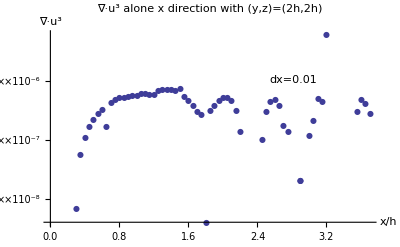

```mathematica
ListLogPlot[R3x,PlotRange->All,PlotMarkers->{Automatic,8},AxesLabel->{"x/h","∇·u^3"},PlotLegends->Placed[Text[Style["dx=0.01",13]],{0.75,0.75}],LabelStyle->Directive[12],PlotLabel->Text[Style["∇·u^3 alone x direction with (y,z)=(2h,2h)",FontFamily->"Times",14]]]
```

```mathematica
(* 可见在*)
```

```mathematica
VectorPlot3D
```

```mathematica
logscale
```

```mathematica
ListPlot[ss]
```

```mathematica
FontFamily
```

FontFamily

```mathematica
With[{a=1},Print[a];Print[a+1]]
```

1

2

```mathematica
ListPlot3D
```

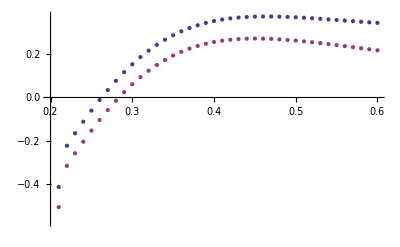

```mathematica
ListPlot[U13[[#]]&/@Range[2]]
```

```mathematica
Do[U13=Append[U13,i],{i,3}]
```

```mathematica
U13
```

{1,2,3}

```mathematica
w13[h0,h0,1.5h0,h0,H]
```

```mathematica
j1a4[h0,h0,1.1h0,h0,H]
```

-0.136708

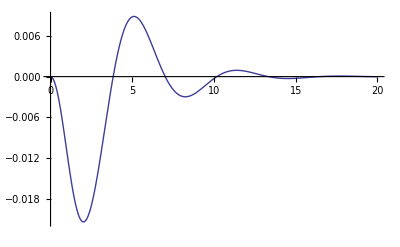

```mathematica
Plot[ a4[x,h0,H,1.1h0]BesselJ[1,x],{x,0,20},PlotRange->All]
```

```mathematica
a2[1]
```

a2[1]

```mathematica
(* 流速为 Subscript[u, j]^k=Subscript[v, j]^k+Subscript[w, j]^k，其中j下标代表空间坐标，k指标代表三个解。*)
(* 压强为 p^k=q^k+S^k*)
```

```mathematica
n=100;h=0.1;H=10h;
xz=Table[h+i/n,{i,1,(3h-h)n}];
```

```mathematica
H-xz
```

{0.89,0.88,0.87,0.86,0.85,0.84,0.83,0.82,0.81,0.8,0.79,0.78,0.77,0.76,0.75,0.74,0.73,0.72,0.71,0.7}

```mathematica
w33up=NIntegrate[BesselJ[0,√2 h x]a2[x,h,H]/.{x3->#}&/@xz,{x,0,400}];
w33down=NIntegrate[BesselJ[0,√2 h x]a2[x,H-h,H]/.{x3->#}&/@(H-xz),{x,0,400}];
Join[w33down,w33up]
```

{-0.733209,-0.765885,-0.790627,-0.808341,-0.819922,-0.826222,-0.828024,-0.826035,-0.820884,-0.81312,-0.803223,-0.791606,-0.778622,-0.764572,-0.74971,-0.734251,-0.718376,-0.702234,-0.68595,-0.669628,-0.744835,-0.778779,-0.804814,-0.823844,-0.836764,-0.844423,-0.847603,-0.847008,-0.843266,-0.836926,-0.828466,-0.818295,-0.806767,-0.794181,-0.780791,-0.766809,-0.752415,-0.737757,-0.722959,-0.708122}

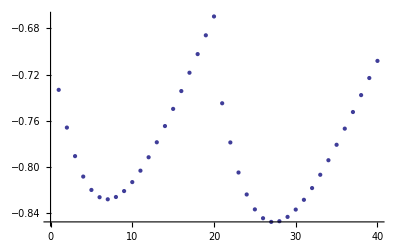

```mathematica
ListPlot[%34]
```

```mathematica
v33up=NIntegrate[BesselJ[0,√2 h x](Sinh[x h]/Sinh[x H] Sinh[x (H-x3)]-x raSinh2[x,h,H])/.{x3->#}&/@xz,{x,0,500}]
v33down=NIntegrate[BesselJ[0,√2 h x](Sinh[x (H-h)]/Sinh[x H] Sinh[x (H-x3)]-x raSinh2[x,H-h,H])/.{x3->#}&/@(H-xz),{x,0,500}]
Join[v33down,v33up]
```

{0.206846,0.290656,0.396458,0.510284,0.626348,0.739193,0.844198,0.937926,1.01821,1.08407,1.13548,1.17311,1.19813,1.21193,1.21602,1.2119,1.20097,1.1845,1.16364,1.13935}

{-154.03,-53784.6,-1.28186×10^7,-2.63491×10^9,-4.9885×10^11,-8.95098×10^13,-1.54586×10^16,-2.59418×10^18,-4.25749×10^20,-6.86481×10^22,-1.09125×10^25,-1.71471×10^27,-2.66894×10^29,-4.12183×10^31,-6.32448×10^33,-9.65203×10^35,-1.46641×10^38,-2.2195×10^40,-3.34872×10^42,-5.03895×10^44}

{-154.03,-53784.6,-1.28186×10^7,-2.63491×10^9,-4.9885×10^11,-8.95098×10^13,-1.54586×10^16,-2.59418×10^18,-4.25749×10^20,-6.86481×10^22,-1.09125×10^25,-1.71471×10^27,-2.66894×10^29,-4.12183×10^31,-6.32448×10^33,-9.65203×10^35,-1.46641×10^38,-2.2195×10^40,-3.34872×10^42,-5.03895×10^44,0.206846,0.290656,0.396458,0.510284,0.626348,0.739193,0.844198,0.937926,1.01821,1.08407,1.13548,1.17311,1.19813,1.21193,1.21602,1.2119,1.20097,1.1845,1.16364,1.13935}

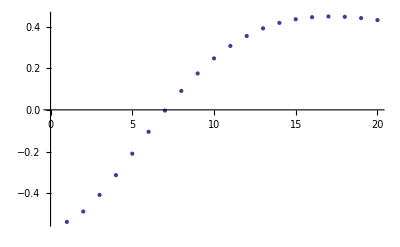

```mathematica
ListPlot[v33+w33]
```

```mathematica
(* 定义积分-Graphics-*)
j0sinh[h_,H_,ρ_]:=Integrate[BesselJ[0,ρ x](Sin h[x h])/Sinh[x H] Sinh[x(H-x3)],{x,0,500}];
j1xsinh[h_,H_,ρ_]:=Integrate[BesselJ[1,ρ x](Sin h[x h])/Sinh[x H] Sinh[x(H-x3)],{x,0,500}];
j0xRasinh[h_,H_,ρ_]:=Integrate[x BesselJ[0,ρ x]raSinh2[x,h,H],{x,0,500}];
j0xcosh[h_,H_,ρ_]:=Integrate[x BesselJ[0,ρ x](Sin h[x h])/Sinh[x H] Cosh[x(H-x3)],{x,0,500}];
δ[x_Integer,y_Integer]:=KroneckerDelta[x,y];
```

```mathematica
vjk=Table[1,{j,3},{k,3}]
```

{{1,1,1},{1,1,1},{1,1,1}}

```mathematica
r={x1,x2};
```

```mathematica
r={x1,x2};
Do[vjk[[j,k]]=Function[δ[j,k]j0sinh[#1,#2,#3]+Sum[δ[j,a]δ[k,b](r[[a]]r[[b]])/ρ,{a,2},{b,2}]j1xsinh[#1,#2,#3]-
δ[j,3]δ[k,3]j0xRasinh[#1,#2,#3]+
Sum[(δ[j,3]δ[k,a]+δ[j,a]δ[k,3])r[[a]],{a,2}]j0xcosh[#1,#2,#3]][h,H,ρ],{j,1,3},{k,1,3}]
```

```mathematica
vjk//MatrixForm
```

vjk

```mathematica
vjk[[j,k]]=Function[δ[j,k]j0sinh[#1,#2,#3]+Sum[δ[j,a]δ[k,b](r[[a]]r[[b]])/ρ,{a,2},{b,2}]j1xsinh[#1,#2,#3]-
δ[j,3]δ[k,3]j0xRasinh[#1,#2,#3]+
Sum[(δ[j,3]δ[k,a]+δ[j,a]δ[k,3])r[[a]],{a,2}]j0xcosh[#1,#2,#3]][h,H,ρ]/.{j->3,k->3,h->0.1,H->0.4,x3->#,ρ->0.1 √2}&/@xz
```

Integrate::idiv: 0.29\ x\ BesselJ[0, 0.141421\ x]\ Cosh[0.29\ x]\ Csch[0.4\ x]\ Sinh[0.1\ x] + « 1 » « 1 » 1.\ x\ BesselJ[0, 0.141421\ x]\ « 1 »\ Csch[0.4\ x]\ Sinh[0.1\ x]\ Sinh[0.29\ x] 的积分在 {0, 500} 上不收敛.

Integrate::idiv: 0.28\ x\ BesselJ[0, 0.141421\ x]\ Cosh[0.28\ x]\ Csch[0.4\ x]\ Sinh[0.1\ x] + 0.1\ x\ « 2 »\ Csch[0.4\ x]\ Sinh[0.28\ x] - 1.\ x\ BesselJ[0, 0.141421\ x]\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.1\ x]\ Sinh[0.28\ x] 的积分在 {0, 500} 上不收敛.

Integrate::idiv: 0.27\ x\ BesselJ[0, 0.141421\ x]\ Cosh[0.27\ x]\ Csch[0.4\ x]\ Sinh[0.1\ x] + 0.1\ x\ « 2 »\ Csch[0.4\ x]\ Sinh[0.27\ x] - 1.\ x\ BesselJ[0, 0.141421\ x]\ Coth[0.4\ x]\ Csch[0.4\ x]\ Sinh[0.1\ x]\ Sinh[0.27\ x] 的积分在 {0, 500} 上不收敛.

General::stop: 在本次计算中，Integrate :: idiv 的进一步输出将被抑制.

```mathematica
wab=Table[1,{a,2},{b,2}]
```

{{1,1},{1,1}}

```mathematica
j1a1[h_,H_,ρ_]:=Integrate[BesselJ[1,ρ x]a1[x,h,H],{x,0,500}]
```

```mathematica
wab[[1,1]]=Function[][h,H,ρ]/.{j->3,k->3}
```

```mathematica
(* Draft *)
```

```mathematica
w33+v33
```

{27.9463,30.6948,33.5014,36.3525,40.2548,42.1631,45.1078,48.067,51.0301,53.9826,56.9056,59.7728,62.5484,65.1843,67.6173,69.7662,71.5305,72.7904,73.4105,75.2739}

```mathematica
w333=NIntegrate[BesselJ[0,√2 h x]a2[x,h,H]/.{x3->#}&/@xz,{x,1.95 10^-6,220}]
```

{3.71336,4.09136,4.47909,4.87581,5.28084,5.69351,6.11327,6.53963,6.97219,7.41067,7.85484,8.30458,8.75983,9.22062,9.68703,10.1592,10.6374,11.1218,11.6128,12.1107}

```mathematica
dist=ProbabilityDistribution[BesselJ[0,√2 h x] √2 h,{x,0,Infinity}]
```

ProbabilityDistribution[0.141421 BesselJ[0,0.141421 x],{x,0,∞}]

```mathematica
s=NIntegrate[PDF[dist,x],{x,0,Infinity}]
```

1.

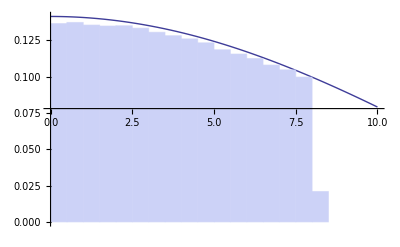

```mathematica
data=RandomVariate[dist,400000];
Show[Plot[Evaluate[PDF[dist,x]],{x,0,10},PlotStyle->Thick,PlotRange->All],
Histogram[data,20,"ProbabilityDensity"]
]
```

```mathematica
sample=RandomVariate[dist,10^2];
integral=Mean[a6[#1,h,H]/.{x3->#2}&/@xz[[1]]&/@sample]
```

0.11

```mathematica
Partition[{{a,b,c,d,e},{a,b,c,d,e}},2,1]
```

{{{a,b,c,d,e},{a,b,c,d,e}}}

```mathematica
s={a,b,c,d,e}
```

{a,b,c,d,e}

```mathematica
Join[s,s]
```

{a,b,c,d,e,a,b,c,d,e}

```mathematica
ss={s,s}
```

{{a,b,c,d,e},{a,b,c,d,e}}

```mathematica
MatrixForm[{{a,b,c,d,e},{a,b,c,d,e}}]
```

(a | b | c | d | e
a | b | c | d | e)

```mathematica
tss=Transpose[ss]//MatrixForm
```

(a | a
b | b
c | c
d | d
e | e)

```mathematica
tss
```

(a | a
b | b
c | c
d | d
e | e)

```mathematica
sh[x_,h_,H_,x3_]:=Sinh[x*h]/Sinh[x*H]Sinh[x*(H-x3)];
ch[x_,h_,H_,x3_]:=Sinh[x*h]/Sinh[x*H]Cosh[x*(H-x3)];
```

```mathematica
w33[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x]a2[x,h,H,x3],{x,0,200}];
v33[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x](sh[x,h,H,x3]-x raSinh2[x,h,H,x3]),{x,0,200}];
```

```mathematica
h0=0.1;H=4h0;
xz=With[{n=100},Table[h0+i/n,{i,1,(3h0-h0)n}]];
```

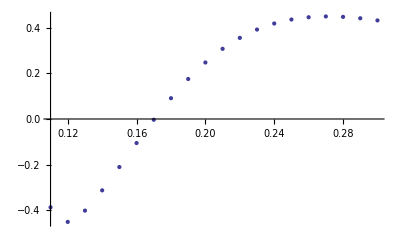

{{0.11,-0.779314},{0.12,-0.883522},{0.13,-0.875471},{0.14,-0.828864},{0.15,-0.769661},{0.16,-0.708289},{0.17,-0.650931},{0.18,-0.601878},{0.19,-0.563955},{0.2,-0.538716},{0.21,-0.526674},{0.22,-0.527563},{0.23,-0.540589},{0.24,-0.56464},{0.25,-0.598451},{0.26,-0.640722},{0.27,-0.690195},{0.28,-0.745694},{0.29,-0.806152},{0.3,-0.870612}}

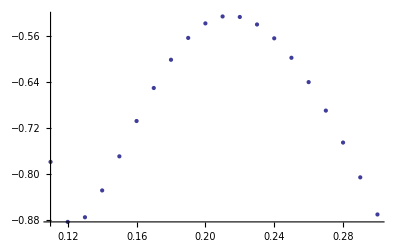

```mathematica
u33=(w33[h0,h0,#,h0,H]+v33[h0,h0,#,h0,H])&/@xz;
u33=Transpose@{xz,u33};
ListPlot[u33]
```

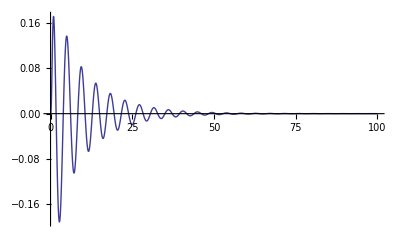

```mathematica
Plot[BesselJ[0,√(h0^2+h0^2)x](sh[x,h0,H,1.1h0]-x raSinh2[x,h0,H,1.1h0]),{x,0,100},PlotRange->All]
```

```mathematica
j0sh[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x]sh[x,h,H,x3],{x,0,400}];
j1xsh[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x]x sh[x,h,H,x3],{x,0,400}];
j0xch[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x]x ch[x,h,H,x3],{x,0,400}];
j1xa1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x]x a1[x,h,H,x3],{x,0,400}];
j0x2a1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x] x^2 a1[x,h,H,x3],{x,0,400}];
j1a3[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x] a3[x,h,H,x3],{x,0,400}];
j1a4[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x] a4[x,h,H,x3],{x,0,400}];
```

```mathematica
v11[r1_,r2_,x3_,h_,H_]:=j0sh[r1,r2,x3,h,H]+r1^2/(√(r1^2+r2^2))j1xsh[r1,r2,x3,h,H];w11[r1_,r2_,x3_,h_,H_]:=j1xa1[r1,r2,x3,h,H](r1^2-r2^2)/((√(r1^2+r2^2))^3)-r1^2/(r1^2+r2^2)j0x2a1[r1,r2,x3,h,H];
v12[r1_,r2_,x3_,h_,H_]:=(r1 r2)/(√(r1^2+r2^2))j1xsh[r1,r2,x3,h,H];w12[r1_,r2_,x3_,h_,H_]:=j1xa1[r1,r2,x3,h,H](2r1 r2)/((√(r1^2+r2^2))^3)-(r1 r2)/(r1^2+r2^2)j0x2a1[r1,r2,x3,h,H];
v13[r1_,r2_,x3_,h_,H_]:=r1 j0xch[r1,r2,x3,h,H];w13[r1_,r2_,x3_,h_,H_]:=-(r1 r2)/(r1^2+r2^2)(j1a3[r1,r2,x3,h,H]+j1a4[r1,r2,x3,h,H]);
```

```mathematica
H=10h0;
u12=(w12[h0,h0,#,h0,H]+v12[h0,h0,#,h0,H])&/@xz;
u12=Transpose@{xz,u12};
ListPlot[u12]
```

NIntegrate::inumri: 在以 {{0., 8.60619×10^-13}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[0, 0.141421\ x]\ (« 1 »)/-1.\ x^2 + Sinh[1.\ x]^2 得到 Overflow、Indeterminate 或者 Infinity.

NIntegrate::ncvb: 在接近 {x} = {6.72645×10^-6} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -4.35645 和 0.623164.

NIntegrate::inumri: 在以 {{0., 8.60619×10^-13}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[0, 0.141421\ x]\ (« 1 »)/-1.\ x^2 + Sinh[1.\ x]^2 得到 Overflow、Indeterminate 或者 Infinity.

General::stop: 在本次计算中，NIntegrate :: inumri 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x} = {6.72645×10^-6} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -4.25945 和 0.616177.

NIntegrate::ncvb: 在接近 {x} = {6.72645×10^-6} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -4.17066 和 0.609189.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

NIntegrate::inumri: 在以 {{0., 8.60619×10^-13}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[0, 0.141421\ x]\ (« 1 »)/-1.\ x^2 + Sinh[1.\ x]^2 得到 Overflow、Indeterminate 或者 Infinity.

General::stop: 在本次计算中，NIntegrate :: inumri 的进一步输出将被抑制.

NIntegrate::inumri: 在以 {{0., 8.60619×10^-13}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[0, 0.141421\ x]\ (« 1 »)/-1.\ x^2 + Sinh[1.\ x]^2 得到 Overflow、Indeterminate 或者 Infinity.

General::stop: 在本次计算中，NIntegrate :: inumri 的进一步输出将被抑制.

$Aborted

```mathematica
j1a4[h0,h0,2h0,h0,H]
```

NIntegrate::inumri: 在以 {{0., 8.60619×10^-13}} 为界的区域内，对于所有采样点，计算被积函数 0.2\ x^2\ BesselJ[0, 0.141421\ x]\ (« 1 »)/-1.\ x^2 + Sinh[1.\ x]^2 得到 Overflow、Indeterminate 或者 Infinity.

NIntegrate[BesselJ[0,√(0.1^2+0.1^2) x] a4[x,0.1,1.,0.2],{x,0,400}]

Power::infy: 碰到无穷表达式 1/0..

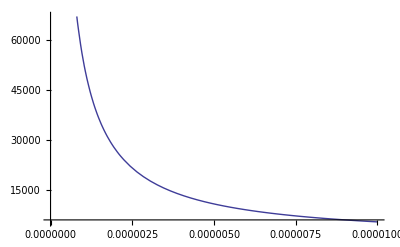

```mathematica
Plot[a4[x,h0,H,2h0]+a3[x,h0,H,2h0], {x,0,10^-5}]
```

```mathematica
NIntegrate[a4[x,h0,H,2h0]BesselJ[0,√(h0^2+h0^2)x] ,{x,0,1}]
```

NIntegrate::inumri: 在以 {{0., 1.91189×10^-8}} 为界的区域内，对于所有采样点，计算被积函数 0.2\ x^2\ BesselJ[0, 0.141421\ x]\ (« 1 »)/-1.\ x^2 + Sinh[1.\ x]^2 得到 Overflow、Indeterminate 或者 Infinity.

NIntegrate[a4[x,h0,H,2 h0] BesselJ[0,√(h0^2+h0^2) x],{x,0,1}]

```mathematica
a4[10^-6,h0,H,2h0]
```

54019.2

```mathematica
h0=0.2;H=10h0;
xz=With[{n=100},Table[i/n,{i,20,(3h0)n}]];
u13=j1xsh[h0,h0,#,h0,H]*(#-h0)1/(√2)-1/(2h0)j1a4[h0,h0,#,h0,H]&/@xz;
u13=Transpose@{xz,u13};
ListPlot[u13]
```

NIntegrate::inumrexpr: 在以 {{1.06437, 398.936}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[1, 0.282843\ x]\ sh[x, 0.2, 2., 1/5] 推出的表达式 {x\ sh[x, 0.2, 2., 1/5], 0} 得到非数值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.282843\ x]\ sh[x, 0.2, 2., 1/5] 得到非数值.

NIntegrate::levtime: 求解线性系统时在 LevinRule 中花费的时间超过了 10. 秒. 请尝试增加 "TimeConstraint" 选项的值，或者降低 "Points" 选项的值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumrexpr: 在以 {{1.06437, 398.936}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[1, 0.282843\ x]\ sh[x, 0.2, 2., 21/100] 推出的表达式 {x\ sh[x, 0.2, 2., 21/100], 0} 得到非数值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

General::stop: 在本次计算中，NIntegrate :: mtdfb 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.282843\ x]\ sh[x, 0.2, 2., 21/100] 得到非数值.

NIntegrate::inumrexpr: 在以 {{1.06437, 398.936}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[1, 0.282843\ x]\ sh[x, 0.2, 2., 21/100] 推出的表达式 {x\ sh[x, 0.2, 2., 21/100], 0} 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumrexpr 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.282843\ x]\ sh[x, 0.2, 2., 21/100] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

NIntegrate::levtime: 求解线性系统时在 LevinRule 中花费的时间超过了 10. 秒. 请尝试增加 "TimeConstraint" 选项的值，或者降低 "Points" 选项的值.

$Aborted

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.141421\ x]\ sh[x, 0.9, 1., 1.] 得到非数值.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.141421\ x]\ sh[x, 0.9, 1., 0.99] 得到非数值.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.141421\ x]\ sh[x, 0.9, 1., 0.98] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

Transpose::nmtx: 无法变换一维列表 {{1/5, 21/100, 11/50, 23/100, 6/25, 1/4, 13/50, 27/100, 7/25, 29/100, 3/10, 31/100, 8/25, 33/100, 17/50, 7/20, 9/25, 37/100, 19/50, 39/100, 2/5, 41/100, 21/50, 43/100, 11/25, 9/20, 23/50, 47/100, 12/25, 49/100, 1/2, 51/100, 13/25, 53/100, 27/50, 11/20, 14/25, 57/100, 29/50, 59/100, 3/5}, {« 1 »}} 的前两层的位置.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.141421\ x]\ sh[x, 0.9, 1., 1.] 得到非数值.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.141421\ x]\ sh[x, 0.9, 1., 0.99] 得到非数值.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.141421\ x]\ sh[x, 0.9, 1., 0.98] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

Transpose::nmtx: 无法变换一维列表 {{1/5, 21/100, 11/50, 23/100, 6/25, 1/4, 13/50, 27/100, 7/25, 29/100, 3/10, 31/100, 8/25, 33/100, 17/50, 7/20, 9/25, 37/100, 19/50, 39/100, 2/5, 41/100, 21/50, 43/100, 11/25, 9/20, 23/50, 47/100, 12/25, 49/100, 1/2, 51/100, 13/25, 53/100, 27/50, 11/20, 14/25, 57/100, 29/50, 59/100, 3/5}, {« 1 »}} 的前两层的位置.

General::stop: 在本次计算中，Transpose :: nmtx 的进一步输出将被抑制.

$Aborted

```mathematica
j1xsh[h0,h0,2h0,h0,H](2h0-h0)*1/(√2)
```

0.825038

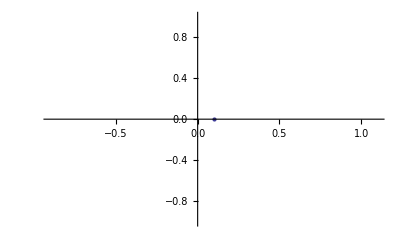

```mathematica
h0=0.1;H=10h0;
xz=With[{n=100},Table[i/n,{i,0,(3h0)n}]];
u13=Piecewise[{{j1xsh[h0,h0,#,h0,H](#-h0)*1/(√2),#>h0},{j1xsh[h0,h0,H-#,H-h0,H](#-h0)*1/(√2),#≤ h0}}]&/@xz;
u13=Transpose@{xz,u13};
ListPlot[u13]
```

```mathematica
a2[x_,h_,H_,x3_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
x3((H Sinh[x*h]Cosh[x x3]-h Sinh[x H]Cosh[x(H-x3-h)]
+x h H Sinh[x*(H-x3)]Sinh[x (H-h)])
+x H Cosh[x(H-x3)]Sinh[x*H] raSinh[x,H-h,H]
-x*H^2 Sinh[x x3] raSinh[x,H-h,H])+H Sinh[x*x3]*Sinh[x*H] raSinh[x,h,H]
);
```

```mathematica
a2[1,1,1,1]
```

(raSinh[1,1,1] Sinh[1]^2)/(-1+Sinh[1]^2)

```mathematica
Plot[j0sh[a4[x,h0,H,2h0]]]
```

```mathematica
v13[h0,h0,3.1h0,3h0,4 h0]
```

3.41972

```mathematica
w13[h0,h0,h0,h0,4h0]
```

0.198786

```mathematica
IntegerPart[-0.13191210244484453]
```

0

```mathematica
a3[x,h0,4h0,0]BesselJ[1,x]-x BesselJ[0,x]ch[x,h0,4h0,0]
```

-x BesselJ[0,x] Coth[0.8 x] Sinh[0.2 x]+BesselJ[1,x] Csch[0.8 x]^2 (-0.8 Sinh[0.2 x]+0.2 Cosh[0.6 x] Sinh[0.8 x])

```mathematica
Simplify[-x BesselJ[0,x] Coth[0.8 x] Sinh[0.2 x]+BesselJ[1,x] Csch[0.8 x]^2 (-0.8 Sinh[0.2 x]+0.2 Cosh[0.6000000000000001 x] Sinh[0.8 x])]
```

-x BesselJ[0,x] Coth[0.8 x] Sinh[0.2 x]+BesselJ[1,x] Csch[0.8 x] (0.2 Cosh[0.6 x]-0.8 Csch[0.8 x] Sinh[0.2 x])

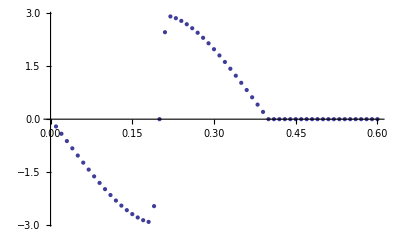

```mathematica
ListPlot[U13[[1]]]
```

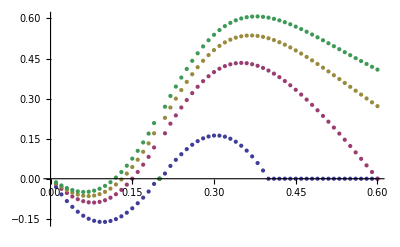

```mathematica
ListPlot[U13[[#]]&/@Range[Length[U13]]]
```

```mathematica
Length[U13]
```

4

```mathematica
w33[h0,h0,2h0,h0,2h0]
```

-0.75765

```mathematica
a2[0.1,h0,2h0,2h0]
```

-7.31899×10^-16

```mathematica
Simplify[%308]
```

(1.73472×10^-16 x^2 (1. Cosh[0.4 x] Sinh[0.2 x]-0.5 Cosh[0.2 x] Sinh[0.4 x]))/(1. x^2-6.25 Sinh[0.4 x]^2)

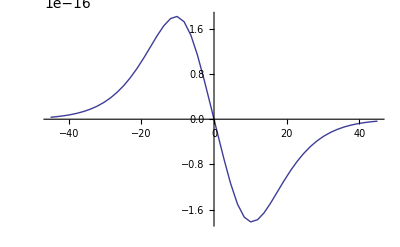

```mathematica
Plot[(1.7347234759768068*^-16 x^2 (1. Cosh[0.4 x] Sinh[0.2 x]-0.5 Cosh[0.2 x] Sinh[0.4 x]))/(1. x^2-6.249999999999999 Sinh[0.4 x]^2),{x,-45.,45.}]
```

```mathematica
Simplify[%258]
```

-(0.08 x^2 ((-1.77636×10^-15 Cosh[0.2 x]-2. x Coth[0.2 x]) Sinh[0.1 x]+Cosh[0.1 x] (1. x+1.0842×10^-15 Sinh[0.2 x])))/(1. x^2-25. Sinh[0.2 x]^2)

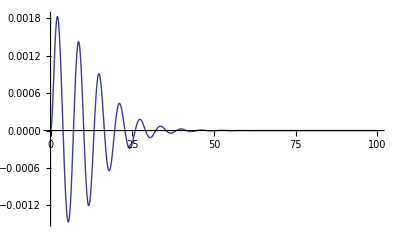

```mathematica
Plot[BesselJ[1,5h0 x]a1[x,h0,4h0,0.01h0] x^2,{x,0,100},PlotRange->All]
```

```mathematica
j1xa1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[1,√(r1^2+r2^2)x]x a1[x,h,H,x3],{x,0,400},Method->{"GaussKronrodRule" }];
j0x2a1[3h0,4h0,3.5h0,3h0,4h0]
```

NIntegrate::levmaxord: 0.336\ x\ Sinh[0.1\ x]\ Sinh[0.2\ x] + « 4 » 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 0.336\ x\ Sinh[0.1\ x]\ Sinh[0.2\ x] + « 4 » 视为非 Levin 函数处理.

0.0381291

```mathematica
j0x2a1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x] x^2 a1[x,h,H,x3],{x,0,400},Method->{"GaussKronrodRule" }];
```

```mathematica
j0x2a1[3h0,4h0,3.5h0,3h0,4h0]
```

0.0381291

```mathematica
U11
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

$Aborted

```mathematica
U11
```

```mathematica
D[BesselJ[1,a √(x^2+y^2)] x/(√(x^2+y^2)),x]
```

-(x^2 BesselJ[1,a √(x^2+y^2)])/((x^2+y^2)^(3/2))+BesselJ[1,a √(x^2+y^2)]/(√(x^2+y^2))+(a x^2 (BesselJ[0,a √(x^2+y^2)]-BesselJ[2,a √(x^2+y^2)]))/(2 (x^2+y^2))

```mathematica
u11=Piecewise[{{(w11[3h0,4h0,#,h0,4 h0]+v11[3h0,4h0,#,h0,4 h0]),4 h0>#>h0}}]&/@xz
```

NIntegrate::levmaxord: 0.0336\ x\ Sinh[0.59\ x]\ Sinh[0.6\ x] + « 1 » « 1 » « 1 » - 0.8\ « 1 »\ (0.8\ x\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + (« 1 » - « 1 »)\ « 1 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 0.0336\ x\ Sinh[0.59\ x]\ Sinh[0.6\ x] + « 1 » « 1 » « 1 » - 0.8\ « 1 »\ (0.8\ x\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + (« 1 » - « 1 »)\ « 1 ») 视为非 Levin 函数处理.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -1.03675×10^28 和 1.1692×10^49.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

NIntegrate::levmaxord: 0.0352\ x\ Sinh[0.58\ x]\ Sinh[0.6\ x] + « 4 » 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 0.0352\ x\ Sinh[0.58\ x]\ Sinh[0.6\ x] + « 4 » 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -2.83442×10^46 和 4.01413×10^45.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 -5.70899×10^45 和 3.42539×10^46.

General::stop: 在本次计算中，NIntegrate :: eincr 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate :: slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x} = {10.6438} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 1.48422×10^45 和 2.30255×10^45.

NIntegrate::ncvb: 在接近 {x} = {11.0344} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -5.28595×10^42 和 1.97582×10^43.

NIntegrate::ncvb: 在接近 {x} = {10.6438} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -5.13701×10^41 和 3.23313×10^40.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-3.7323×10^27+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,21/100],{x,0,400}],-0.0691503+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,11/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,11/50],{x,0,400}],-3.03995×10^46,1.48422×10^45+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,6/25],{x,0,400}],-0.0747174+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,1/4],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,1/4],{x,0,400}],-0.0763555+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,13/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,13/50],{x,0,400}],-1.90294×10^42+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,27/100],{x,0,400}],-5.13701×10^41+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,7/25],{x,0,400}],2.28426×10^40+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,29/100],{x,0,400}],-1.70515×10^40,1.2919×10^39+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,31/100],{x,0,400}],-2.55159×10^38+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,8/25],{x,0,400}],-9.77977×10^35+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,33/100],{x,0,400}],1.09425×10^36+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,17/50],{x,0,400}],1.17394×10^36+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,7/20],{x,0,400}],-2.2667×10^34+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,9/25],{x,0,400}],1.75912×10^33,-0.0872692+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,19/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,19/50],{x,0,400}],1.21755×10^31+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,39/100],{x,0,400}],-1.16145×10^31+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,2/5],{x,0,400}],-0.0874169+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,41/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,41/100],{x,0,400}],-0.0872334+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,21/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,21/50],{x,0,400}],-0.0869335+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,43/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,43/100],{x,0,400}],-0.0865169+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,11/25],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,11/25],{x,0,400}],-0.085984+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,9/20],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,9/20],{x,0,400}],-0.0853347+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,23/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,23/50],{x,0,400}],-0.0845692+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,47/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,47/100],{x,0,400}],-0.0836879+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,12/25],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,12/25],{x,0,400}],-0.082691+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,49/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,49/100],{x,0,400}],-0.0815791+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,1/2],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,1/2],{x,0,400}],-0.0803524+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,51/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,51/100],{x,0,400}],-0.0790117+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,13/25],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,13/25],{x,0,400}],-0.0775576+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,53/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,53/100],{x,0,400}],-0.0759907+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,27/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,27/50],{x,0,400}],-0.0743119+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,11/20],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,11/20],{x,0,400}],-0.072522+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,14/25],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,14/25],{x,0,400}],-0.0706221+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,57/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,57/100],{x,0,400}],-0.0686131+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,29/50],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,29/50],{x,0,400}],-0.0664963+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,59/100],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,59/100],{x,0,400}],-0.0642728+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.2,0.8,3/5],{x,0,400}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.2,0.8,3/5],{x,0,400}]}

```mathematica
{(w11[3h0,4h0,#,h0,4 h0]+v11[3h0,4h0,4 h0-#,4 h0-h0,4 h0]),#<h0}
```

NIntegrate::levmaxord: -0.8\ (« 1 »)\ Sinh[x\ #1] + 0.8\ x\ Cosh[x\ (0.8  - #1)]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[« 1 »]\ « 1 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]\ #1 + « 1 » + 0.16\ x\ Sinh[0.6\ x]\ Sinh[x\ (0.8  - #1)]\ #1 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.8\ (« 1 »)\ Sinh[x\ #1] + 0.8\ x\ Cosh[x\ (0.8  - #1)]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[« 1 »]\ « 1 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]\ #1 + « 1 » + 0.16\ x\ Sinh[0.6\ x]\ Sinh[x\ (0.8  - #1)]\ #1 视为非 Levin 函数处理.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 1.\ x]\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

NIntegrate::levmaxord: -0.8\ (« 1 »)\ Sinh[x\ #1] + 0.8\ x\ Cosh[x\ (0.8  - #1)]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[« 1 »]\ « 1 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]\ #1 + « 1 » + 0.16\ x\ Sinh[0.6\ x]\ Sinh[x\ (0.8  - #1)]\ #1 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.8\ (« 1 »)\ Sinh[x\ #1] + 0.8\ x\ Cosh[x\ (0.8  - #1)]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[« 1 »]\ « 1 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]\ #1 + « 1 » + 0.16\ x\ Sinh[0.6\ x]\ Sinh[x\ (0.8  - #1)]\ #1 视为非 Levin 函数处理.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 1.\ x]\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

NIntegrate::levmaxord: -0.8\ (« 1 »)\ Sinh[x\ #1] + 0.8\ x\ Cosh[x\ (0.8  - #1)]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[« 1 »]\ « 1 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]\ #1 + « 1 » + 0.16\ x\ Sinh[0.6\ x]\ Sinh[x\ (0.8  - #1)]\ #1 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.8\ (« 1 »)\ Sinh[x\ #1] + 0.8\ x\ Cosh[x\ (0.8  - #1)]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[« 1 »]\ « 1 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]\ #1 + « 1 » + 0.16\ x\ Sinh[0.6\ x]\ Sinh[x\ (0.8  - #1)]\ #1 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

General::stop: 在本次计算中，NIntegrate :: mtdfb 的进一步输出将被抑制.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 « 1 »/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

{-0.28 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x a1[x,0.2,0.8,#1],{x,0,400},Method→GaussKronrodRule,Exclusions→{0}]-0.36 NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] x^2 a1[x,0.2,0.8,#1],{x,0,400},Method→{GaussKronrodRule},Exclusions→{0}]+0.36 NIntegrate[BesselJ[1,√(0.6^2+0.8^2) x] x sh[x,0.6,0.8,0.8-#1],{x,0,400},WorkingPrecision→15,AccuracyGoal→6,Method→{Automatic,SymbolicProcessing→False}]+NIntegrate[BesselJ[0,√(0.6^2+0.8^2) x] sh[x,0.6,0.8,0.8-#1],{x,0,400},WorkingPrecision→15,AccuracyGoal→6,Method→{Automatic,SymbolicProcessing→False}],#1<0.2}

```mathematica
u11=Transpose@{xz,u11};
```

{{1/100,0.0772282},{1/50,0.152051},{3/100,0.224656},{1/25,0.295178},{1/20,0.363689},{3/50,0.430196},{7/100,0.494635},{2/25,0.556877},{9/100,0.616731},{1/10,0.673949},{11/100,0.728235},{3/25,0.77926},{13/100,0.826668},{7/50,0.870098},{3/20,0.909194},{4/25,0.943622},{17/100,0.973054},{9/50,0.995572},{19/100,0.916199},{1/5,0},{21/100,-0.0670793},{11/50,-0.0691503},{23/100,-0.071114},{6/25,-0.07297},{1/4,-0.0747174},{13/50,-0.0763555},{27/100,-0.0778838},{7/25,-0.0793014},{29/100,-0.0806079},{3/10,-0.0818026},{31/100,-0.0828848},{8/25,-0.083854},{33/100,-0.0847097},{17/50,-0.0854514},{7/20,-0.0860786},{9/25,-0.0865909},{37/100,-0.0869878},{19/50,-0.0872692},{39/100,-0.0874347},{2/5,-0.087484},{41/100,-0.0874169},{21/50,-0.0872334},{43/100,-0.0869335},{11/25,-0.0865169},{9/20,-0.085984},{23/50,-0.0853347},{47/100,-0.0845692},{12/25,-0.0836879},{49/100,-0.082691},{1/2,-0.0815791},{51/100,-0.0803524},{13/25,-0.0790117},{53/100,-0.0775576},{27/50,-0.0759907},{11/20,-0.0743119},{14/25,-0.072522},{57/100,-0.0706221},{29/50,-0.0686131},{59/100,-0.0664963},{3/5,-0.0642728}}

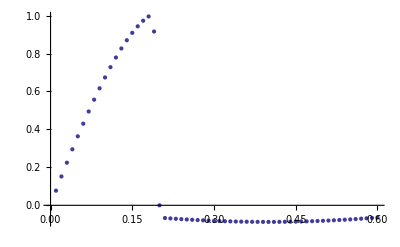

```mathematica
ListPlot[u11]
```

```mathematica
u11=Piecewise[{{(w11[3h0,4h0,#,h0,4 h0]),4 h0>#}}]&/@xz
```

NIntegrate::levmaxord: « 1 » 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 « 1 » 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

{-0.00417538,-0.00825571,-0.0122406,-0.0161296,-0.0199222,-0.0236181,-0.0272168,-0.0307177,-0.0341204,-0.0374243,-0.0406289,-0.0437337,-0.046738,-0.0496412,-0.0524427,-0.0551419,-0.0577381,-0.0602306,-0.0626188,-0.0649019,-0.0670793,-0.0691503,-0.071114,-0.07297,-0.0747174,-0.0763555,-0.0778838,-0.0793014,-0.0806079,-0.0818026,-0.0828848,-0.083854,-0.0847097,-0.0854514,-0.0860786,-0.0865909,-0.0869878,-0.0872692,-0.0874347,-0.087484,-0.0874169,-0.0872334,-0.0869335,-0.0865169,-0.085984,-0.0853347,-0.0845692,-0.0836879,-0.082691,-0.0815791,-0.0803524,-0.0790117,-0.0775576,-0.0759907,-0.0743119,-0.072522,-0.0706221,-0.0686131,-0.0664963,-0.0642728}

```mathematica
u11=Piecewise[{{(v11[3h0,4h0,#,h0,4 h0]),4 h0>#>h0},{(v11[3h0,4h0,4h0-#,4h0-h0,4 h0]),#<h0}}]&/@xz
```

{0.00230948,0.00461472,0.00691146,0.00919586,0.0114633,0.0137098,0.0159315,0.0181242,0.0202839,0.0224072,0.0244898,0.0265281,0.0285196,0.0304594,0.0323449,0.0341715,0.0359579,0.0385847,0.0904903,0,0.0935577,0.044715,0.0451416,0.0463947,0.0475888,0.0487008,0.0497307,0.0506766,0.0515389,0.0523154,0.0530056,0.0536094,0.0541259,0.054555,0.0548968,0.0551511,0.055318,0.0553984,0.0553924,0.0553006,0.0551238,0.0548631,0.0545195,0.0540937,0.0535872,0.0530014,0.0523378,0.0515978,0.0507831,0.0498954,0.0489365,0.0479082,0.0468126,0.0456515,0.044427,0.0431413,0.0417964,0.0403947,0.0389384,0.0374297}

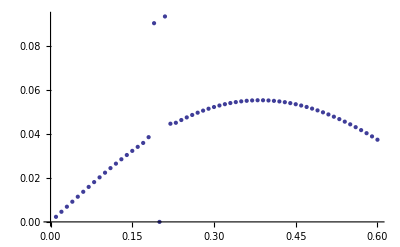

```mathematica
u11=Transpose@{xz,u11};
ListPlot[u11]
```

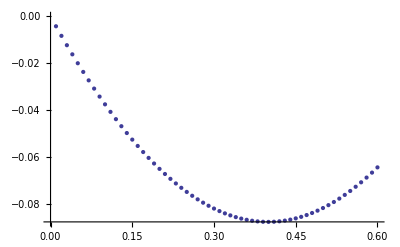

```mathematica
u11=Transpose@{xz,u11};
ListPlot[u11]
```

```mathematica
j0x2a1[r1_,r2_,x3_,h_,H_]:=NIntegrate[BesselJ[0,√(r1^2+r2^2)x] x^2 a1[x,h,H,x3],{x,0,400},Method->"GaussKronrodRule" ];
```

```mathematica
j0x2a1[3h0,4h0,2h0,h0,4 h0]
```

0.094158

```mathematica
NIntegrate[BesselJ[1,√(0.6000000000000001^2+0.8^2) x] x sh[x,0.2,0.8,13/25],{x,0,400},WorkingPrecision->15,AccuracyGoal->6,Method->{Automatic,"SymbolicProcessing"->False}]
```

0.0810559248310979

```mathematica
v11[3h0,4h0,2h0,h0,4 h0]
w11[3h0,4h0,2h0,h0,4 h0]
```

0.0553006

-0.087484

```mathematica
NIntegrate[BesselJ[0,√(0.6000000000000001^2+0.8^2) x] sh[x,0.2,0.8,#],{x,0,400},WorkingPrecision->15,AccuracyGoal->6,Method->{Automatic,"SymbolicProcessing"->False}]&/@xz[[25;;]]
```

{0.0181960904287265,0.0186347103470959,0.0190429357180196,0.0194194853204768,0.0197653482506534,0.0200789687469422,0.0203599819137912,0.0206087147370824,0.0208244258084477,0.0210069144451115,0.0211562957291728,0.0212723093075381,0.0213549525077088,0.0214042584499078,0.0214203083976323,0.0214032340084317,0.0213532174705822,0.0212704907022901,0.0211556068909969,0.0210082359017828,0.0208291827077453,0.0206188464530102,0.020377676869184,0.0201061696581026,0.0198048630893842,0.0194743353514311,0.0191152023207682,0.0187281156084903,0.0183137607669198,0.0178728555993754,0.0174061485391376,0.0169144170789353,0.016398466241205,0.0158591270845067,0.0152972552443558,0.014713729508252}

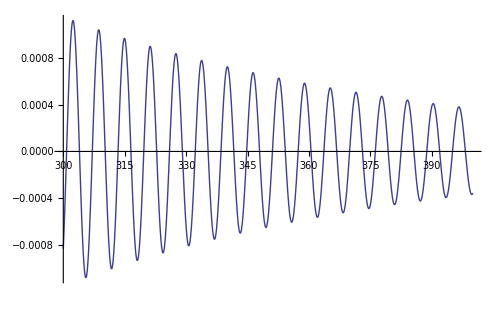

```mathematica
Plot[BesselJ[0,√(0.6000000000000001^2+0.8^2) x] sh[x,0.2,0.8,21/100],{x,300,400},PlotRange->All]
```

```mathematica
Clear[g]
```

```mathematica
f[x_,y_]:=x+y;g[x_,y_]:=x y;
```

```mathematica
f@@{a,b}
```

a+b

```mathematica
f[##]+g[##]&[a,b]
```

a+b+a b

```mathematica
v11[r1_,r2_,x3_,h_,H_]:=j0sh[##]+r1^2/(√(r1^2+r2^2))j1xsh[##]&[r1,r2,x3,h,H];
```

```mathematica
v11[3h0,4h0,2h0,h0,4 h0]
```

0.0553006

```mathematica
ListVectorPlot[]
```

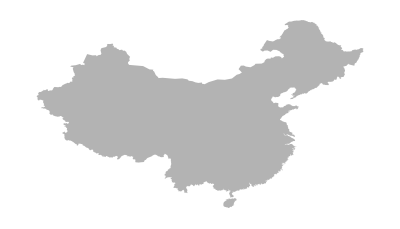

```mathematica
g=Graphics[{GrayLevel[.7],CountryData["China","Polygon"]}]
```

```mathematica
vectors=ListVectorPlot[Table[{{x,y},-Through[{Sin,Cos}[WeatherData[{y,x},"WindDirection"]°]]},{x,60,130,7},{y,24,60,6}]];
```

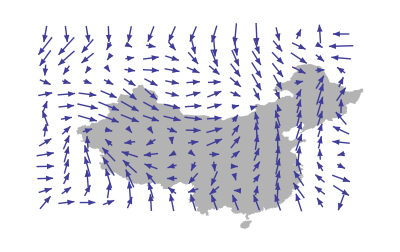

```mathematica
Show [g,vectors]
```

```mathematica
With[{nmin=0.1,nmax=5,n=10},Table[{x,y},{x,nmin h0,nmax h0,(nmax-nmin)/n},{y,nmin h0,nmax h0,(nmax-nmin)/n}]]
```

{{{0.02,0.02},{0.02,0.51},{0.02,1.}},{{0.51,0.02},{0.51,0.51},{0.51,1.}},{{1.,0.02},{1.,0.51},{1.,1.}}}

```mathematica
v23[r1_,r2_,x3_,h_,H_]:=v13 @@{r2,r1,x3,h,H};w23[r1_,r2_,x3_,h_,H_]:=w13@@{r2,r1,x3,h,H};
```

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 « 1 »/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

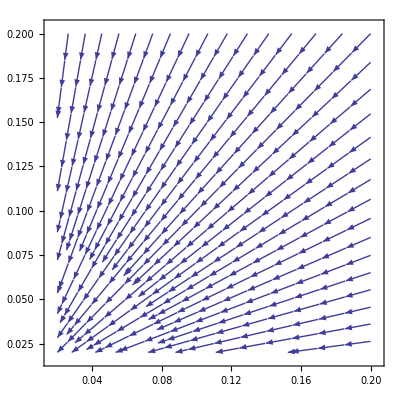

```mathematica
(* x3=h0, 范围为（0.1h0 , 5h0）。力的方向沿z方向。所以只用考虑13,23*)
StreamPlot[{w13[##],w23[##]}&[x,y,h0,h0,4h0],{x,0.1h0,1h0},{y,0.1h0,1h0}]
```

```mathematica
{f[##],g[##]}&[x,y]
```

{x+y,x y}

```mathematica
{w13[##],w23[##]}&[5h0,5h0,h0,h0,4h0]
```

{0.000288388,0.000288388}

```mathematica
{w13[##],w23[##]}&[h0,h0,h0,h0,4h0]
```

{-0.303902,-0.303902}

```mathematica
##&[h0,h0,1.1h0,h0,4h0]
```

Sequence[0.2,0.2,0.22,0.2,0.8]

```mathematica
Array[]
```

```mathematica
w13@@{0.0001h0,0.0001h0,h0,h0,4h0}
```

-0.0000893285

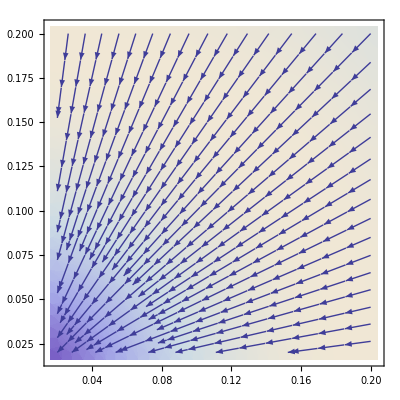

```mathematica
StreamDensityPlot[{w13[##],w23[##]}&[x,y,h0,h0,4h0],{x,0.1h0,h0},{y,0.1h0,h0}]
```

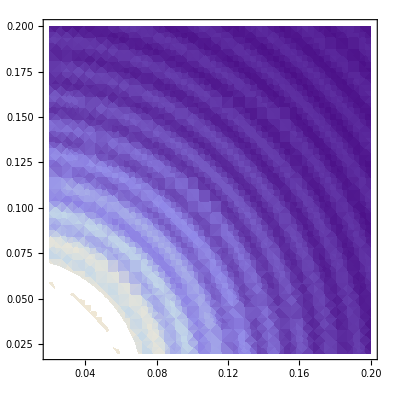

```mathematica
DensityPlot[(w33[##]+v33[##])&[x,y,h0,h0,4h0],{x,0.1h0,1h0},{y,0.1h0,1h0}]
```

```mathematica
DensityPlot[(w33[##]+v33[##])&[x,y,h0,h0,4h0],{x,0.01h0,0.1h0},{y,0.01h0,0.1h0},PlotLegends->Automatic]
```

-Graphics-

```mathematica
StreamDensityPlot[{w13[##],w23[##]}&[x,y,h0,h0,4h0],{x,0.1h0,5h0},{y,0.1h0,5h0},PlotLegends->BarLegend["LakeColors"]]
```

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x^2\ « 1 »\ (0.48\ Sinh[0.2\ x]^2 - « 20 »\ « 4 » + « 1 » - 0.2\ (0.8\ Sinh[Times[« 2 »]]^2 + 0.2\ Sinh[« 19 »\ x]\ Sinh[0.8\ x]))/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

-Graphics-

```mathematica
(f[##]+g[##])&[x,y]
```

x+y+x y

```mathematica
Options[VectorDensityPlot]//Short
```

{AlignmentPoint→Center,«63»,WorkingPrecision→MachinePrecision}

```mathematica
SetOptions[VectorDensityPlot,PlotLegends->BarLegend["LakeColors",Automatic]];
```

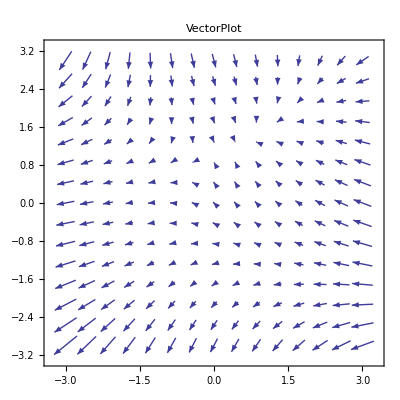
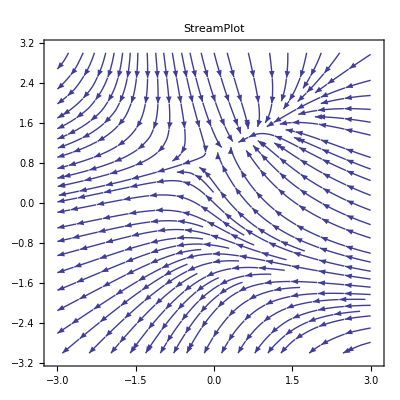
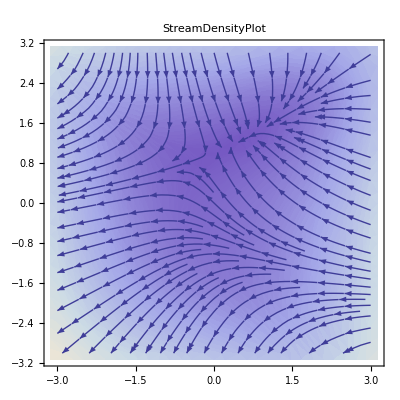
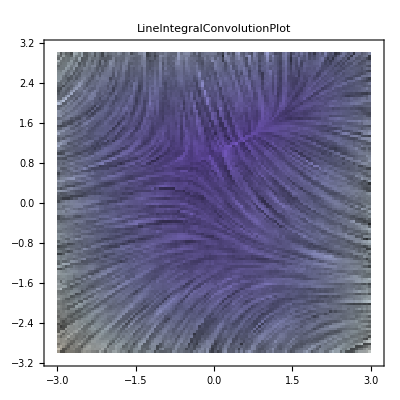
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[f[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},PlotLabel->f],{f,{VectorPlot,VectorDensityPlot,StreamPlot,StreamDensityPlot,LineIntegralConvolutionPlot}}]
```

```mathematica
VectorDensityPlot[{{x,y},{y,-x}},{x,-h0,h0},{y,-h0,h0},PlotLegends->BarLegend["LakeColors"],
RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2≥ (h0)^2]];//AbsoluteTiming
VectorDensityPlot[{{x,y},{y,-x}},{x,-h0,h0},{y,-h0,h0},PlotLegends->BarLegend["LakeColors"]];//AbsoluteTiming
```

{0.08706,Null}

{0.08006,Null}

```mathematica
(* 画出z方向的点力，在其所在xy平面造成的xy流速场。*)
With[{n=10},VectorDensityPlot[{u13[##],u23[##]}&[x h0,y h0,h0,h0,4h0],{x,4,n },{y,4 ,n },PlotLabel->titlexy,MaxRecursion->2,RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2≥ (4h0)^2],
FrameLabel->{"x/h","y/h"}]]
```

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x^2\ « 1 »\ (0.48\ Sinh[0.2\ x]^2 - « 20 »\ « 4 » + « 1 » - 0.2\ (0.8\ Sinh[Times[« 2 »]]^2 + 0.2\ Sinh[« 19 »\ x]\ Sinh[0.8\ x]))/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

-Graphics-

```mathematica
With[{n=10},VectorDensityPlot[{u13[##],u23[##]}&[x h0,y h0,h0,h0,4h0],{x,4,n },{y,4 ,n },PlotLabel->titlexy,MaxRecursion->2,RegionFunction->Function[{x,y,vx,vy,n},x^2+y^2≥ (4h0)^2],
FrameLabel->{"x/h","y/h"}]]
```

```mathematica
(* 画出z方向的点力，在其所在xz平面造成的xz流速场。*)
With[{n=5,H=4h0},VectorDensityPlot[{u13[##],u33[##]}&[x h0,0,z h0,h0,H],{x,-n,n },{z,0,H/h0},PlotLabel->titlexz,MaxRecursion->2,
FrameLabel->{"x/h","z/h"}]]
```

```mathematica
{u13[##],u33[##]}&[x h0,0,z h0,h0,H]
u13xz[x_,z_,H_]:=
```

NIntegrate::ncvb: 在接近 {x} = {10.3508} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -4.67606×10^29 和 4.59916×10^28.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x^2\ BesselJ[1, 0.2\ x\ √x^2]\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2 得到非数值.

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[1, 0.2\ x\ √x^2]\ Csch[0.8\ x]\ Sinh[0.2\ x]\ Sinh[x\ (0.8  - 0.2\ z)] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

NIntegrate::inumrexpr: 在以 {{1.06437, 398.936}} 为界的区域内，对于所有采样点，计算从被积函数 x^2\ BesselJ[0, 0.2\ x\ √x^2]\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2 推出的表达式 {x^2\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2, 0} 得到非数值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumrexpr: 在以 {{1.06437, 398.936}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[0, 0.2\ x\ √x^2]\ ((0.8  - 0.2\ z)\ Cosh[x\ (0.8  - 0.2\ z)]\ Csch[0.8\ x]\ Sinh[0.2\ x] + 0.2\ Cosh[0.2\ x]\ Csch[0.8\ x]\ Sinh[x\ (0.8  - 0.2\ z)] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x]\ Sinh[x\ (0.8  - 0.2\ z)]) 推出的表达式 {x\ (0.8  - 0.2\ z)\ Csch[0.8\ x], 0, 0, 0, 0.2\ x\ Csch[0.8\ x], 0., 0., 0., -0.8\ x\ Coth[0.8\ x]\ Csch[0.8\ x], 0., 0., 0., 0, 0, 0, 0, 0., 0., 0., 0., 0., 0., 0., 0.} 得到非数值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumrexpr: 在以 {{1.06437, 398.936}} 为界的区域内，对于所有采样点，计算从被积函数 x^2\ BesselJ[0, 0.2\ x\ √x^2]\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2 推出的表达式 {x^2\ (« 1 »)/-0.64\ x^2 + Sinh[0.8\ x]^2, 0} 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumrexpr 的进一步输出将被抑制.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

General::stop: 在本次计算中，NIntegrate :: mtdfb 的进一步输出将被抑制.

-Graphics-

```mathematica
w33@@{h0,h0,h0,h0,4h0}-w33@@{h0,h0,3h0,3h0,4h0}
```

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.2\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[0.2\ x]\ « 1 »\ Sinh[0.8\ x] + 0.2\ (0.8\ Cosh[0.2\ x]\ Sinh[0.2\ x] + « 4 ») 是一个微分阶数为 51 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.2\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[0.2\ x]\ « 1 »\ Sinh[0.8\ x] + 0.2\ (0.8\ Cosh[0.2\ x]\ Sinh[0.2\ x] + « 4 ») 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ (0.2\ Cosh[0.2\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x])\ Sinh[0.6\ x] + « 1 » + 0.6\ (0.48\ x\ « 1 »^2 + « 3 » + « 1 ») 是一个微分阶数为 51 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ (0.2\ Cosh[0.2\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x])\ Sinh[0.6\ x] + « 1 » + 0.6\ (0.48\ x\ « 1 »^2 + « 3 » + « 1 ») 视为非 Levin 函数处理.

2.55351×10^-15

```mathematica
j0xdsh[h0,h0,h0,h0,4h0]
j0xdsh[h0,h0,3h0,3h0,4h0]
```

0.718072

0.718072

```mathematica
x
```

x

```mathematica
Clear[x,h,y]
```

```mathematica
h
```

h

```mathematica
u13[]
```

```mathematica
raSinh2[y,h,H,x]-raSinh2[y,H-h,H,H-x]
```

(H-x) Cosh[(H-x) y] Csch[H y] Sinh[h y]-x Cosh[x y] Csch[H y] Sinh[(-h+H) y]+h Cosh[h y] Csch[H y] Sinh[(H-x) y]-H Coth[H y] Csch[H y] Sinh[h y] Sinh[(H-x) y]-(-h+H) Cosh[(-h+H) y] Csch[H y] Sinh[x y]+H Coth[H y] Csch[H y] Sinh[(-h+H) y] Sinh[x y]

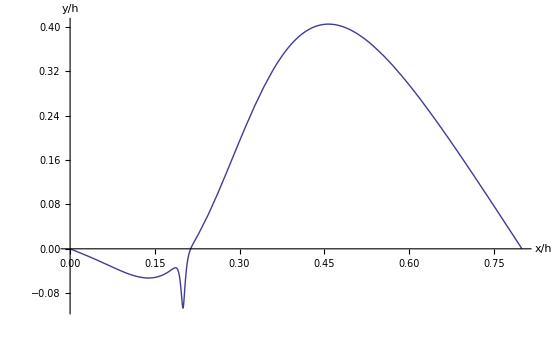

```mathematica
(* v33在（Subscript[h, 0],Subscript[h, 0],x）上的变化。*)
Plot[Piecewise[{{v33[##]&[h0,h0,x3 h0,h0,4h0],x3>h0},{v33[##]&[h0,h0,4h0-x3 h0,4h0-h0,4h0],x3<h0}}],{x3,0,4},AxesLabel->{"x3/h","v33"}]
```

```mathematica
u13@@{h0,h0,h0,h0,4h0}
```

-0.303902

```mathematica
titlexy=Style["力点所在xy平面的流场",FontFamily->"Helvetica"]
```

力点所在xy平面的流场

```mathematica
titlexz=Style["力点所在xz平面的流场",FontFamily->"Helvetica"]
```

力点所在xz平面的流场

```mathematica
VectorDensityPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3},RegionFunction->Function[{x,y,vx,vy,n},n>3]]
```

-Graphics-

```mathematica
f[x_,y_]:=x+y
```

```mathematica
g[x_,y_]:=x+f[##]&[x,y]
```

```mathematica
g[x,y]
```

2 x+y

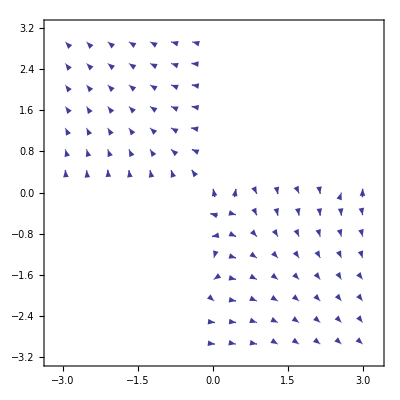
{0.06104,-Graphics-}

```mathematica
ListVectorPlot[Table[{{x,y}=RandomReal[{-3,3},{2}],{1/x,1/y}},{200}],RegionFunction->Function[{x,y,vx,vy,n},x y<0]]//AbsoluteTiming
```

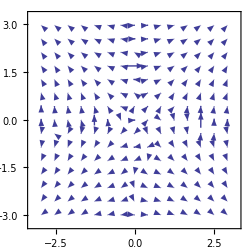
{0.06204,-Graphics-}

```mathematica
ListVectorPlot[Table[{{x,y}=RandomReal[{-3,3},{2}],{1/x,1/y}},{200}]]//AbsoluteTiming
```

```mathematica
ss=Flatten[Table[{x,y},{x,-5h0,5h0,10h0/2},{y,0,4h0,4h0/2}],1]
```

{{-1.,0.},{-1.,0.4},{-1.,0.8},{0.,0.},{0.,0.4},{0.,0.8},{1.,0.},{1.,0.4},{1.,0.8}}

```mathematica
f[list_List,z_]:=list[[1]]+list[[2]]+z;
```

```mathematica
f[#,1]&/@ss
```

{0.,0.4,0.8,1.,1.4,1.8,2.,2.4,2.8}

```mathematica
g[x_,y_,z_]:=x+y+z
```

```mathematica
Join[{g[#[[1]],#[[2]],1],g[#[[1]],#[[2]],1]}&/@ss,ss]
```

{{0.,0.},{0.4,0.4},{0.8,0.8},{1.,1.},{1.4,1.4},{1.8,1.8},{2.,2.},{2.4,2.4},{2.8,2.8},{-1.,0.},{-1.,0.4},{-1.,0.8},{0.,0.},{0.,0.4},{0.,0.8},{1.,0.},{1.,0.4},{1.,0.8}}

```mathematica
u13[#[[1]],0,#[[2]],h0,4h0]&/@ss
```

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0.\ ComplexInfinity.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 0.\ ComplexInfinity.

Power::infy: 碰到无穷表达式 1/0..

General::stop: 在本次计算中，Power :: infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0.\ ComplexInfinity.

General::stop: 在本次计算中，Infinity :: indet 的进一步输出将被抑制.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

General::stop: 在本次计算中，NIntegrate :: izero 的进一步输出将被抑制.

{0.,0.000013954,0,Indeterminate,Indeterminate,0,0.,-0.000013954,0}

```mathematica
u13=Piecewise[{{(w13[h0,h0,#,h0,i h0]+(#-h0)v13[h0,h0,#,h0,i h0]),i h0>#>h0},{(w13[h0,h0,#,h0,i h0]+(#-h0)v13[h0,h0,i h0-#,i h0-h0,i h0]),#<h0}}]&/@xz;
u13=Transpose@{xz,u13};U13=Append[U13,u13],{i,{2,3,4,10}}];
```

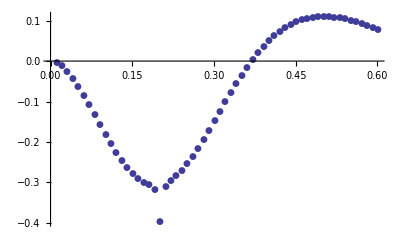

```mathematica
U33={};
Do[uu33=u33[h0,h0,#,h0,i h0]&/@xz;
uu33=Transpose@{xz,uu33};U33=Append[U33,uu33],{i,{4}}];
ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic]
```

```mathematica
Flatten[With[{n=10},Table[{{x,z},x+z},{x,h0/n,4(h0),4h0/n},{z,h0/n,3h0,(3h0)/n}]],1]
```

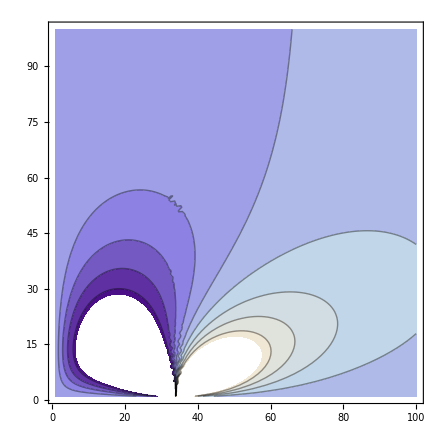

```mathematica
(* u13 在xz平面上的contour值.*)
ListContourPlot[With[{n=100},Table[u13[i,0,j,h0,4 h0],{i,h0/n,4(h0),4h0/n},{j,h0/n,3h0,(3h0)/n}]]]
```

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.04\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[« 20 »\ x]\ « 1 »\ Sinh[0.8\ x] + 0.04\ (« 1 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.04\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[« 20 »\ x]\ « 1 »\ Sinh[0.8\ x] + 0.04\ (« 1 ») 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.16\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[« 20 »\ x]\ « 1 »\ Sinh[0.8\ x] + 0.16\ (« 1 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.16\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[« 20 »\ x]\ « 1 »\ Sinh[0.8\ x] + 0.16\ (« 1 ») 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.28\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.28\ (0.8\ Cosh[0.28\ x]\ Sinh[0.2\ x] + « 1 » - « 1 » + 0.8\ « 3 »\ Sinh[0.8\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.28\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.28\ (0.8\ Cosh[0.28\ x]\ Sinh[0.2\ x] + « 1 » - « 1 » + 0.8\ « 3 »\ Sinh[0.8\ x]) 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

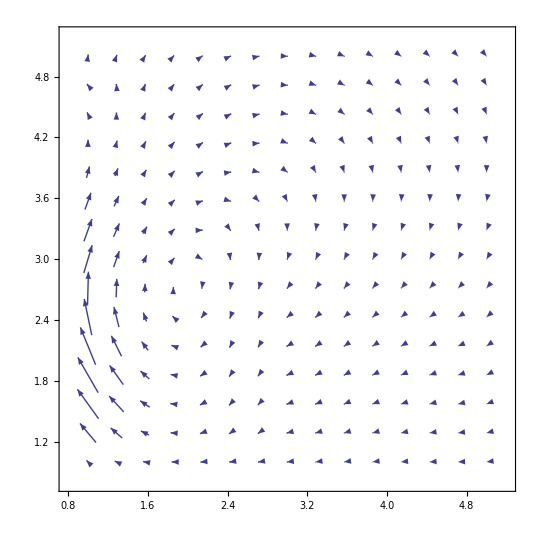

```mathematica
(* （u13，u33） 在xz平面上的速度场（每个方向5个点，总共25个点）.*)
ListVectorPlot[With[{n=5},Table[{u13[i ,0,j ,h0,4 h0],u33[i,0,j,h0,4 h0]},{i,h0/n,4(h0),4h0/n},{j,h0/n,3h0,(3h0)/n}]]]
```

```mathematica
With[{n=10},Table[{{x,z},u13[x,0,z,h0,4h0]},{x,h0/n,4(h0),4h0/n},{z,h0/n,3h0,(3h0)/n}]]
```

{{{{0.02,0.02},-0.235753},{{0.02,0.08},-0.764193},{{0.02,0.14},-2.4777},{{0.02,0.2},-0.0887496},{{0.02,0.26},2.30144},{{0.02,0.32},0.61159},{{0.02,0.38},0.260231},{{0.02,0.44},0.138455},{{0.02,0.5},0.0842857},{{0.02,0.56},0.0561622}},{{{0.1,0.02},-0.710253},{{0.1,0.08},-1.9134},{{0.1,0.14},-2.31809},{{0.1,0.2},-0.381267},{{0.1,0.26},1.57783},{{0.1,0.32},1.32295},{{0.1,0.38},0.83149},{{0.1,0.44},0.525134},{{0.1,0.5},0.349624},{{0.1,0.56},0.245276}},{{{0.18,0.02},-0.52738},{{0.18,0.08},-1.34716},{{0.18,0.14},-1.27702},{{0.18,0.2},-0.495404},{{0.18,0.26},0.349824},{{0.18,0.32},0.69465},{{0.18,0.38},0.675414},{{0.18,0.44},0.550141},{{0.18,0.5},0.427551},{{0.18,0.56},0.330278}},{{{0.26,0.02},-0.290263},{{0.26,0.08},-0.788887},{{0.26,0.14},-0.789799},{{0.26,0.2},-0.456356},{{0.26,0.26},-0.0381669},{{0.26,0.32},0.258314},{{0.26,0.38},0.387386},{{0.26,0.44},0.404604},{{0.26,0.5},0.370598},{{0.26,0.56},0.319302}},{{{0.34,0.02},-0.150728},{{0.34,0.08},-0.443119},{{0.34,0.14},-0.489296},{{0.34,0.2},-0.352609},{{0.34,0.26},-0.138828},{{0.34,0.32},0.0572887},{{0.34,0.38},0.189009},{{0.34,0.44},0.254663},{{0.34,0.5},0.272333},{{0.34,0.56},0.260049}},{{{0.42,0.02},-0.0788556},{{0.42,0.08},-0.247545},{{0.42,0.14},-0.297595},{{0.42,0.2},-0.246435},{{0.42,0.26},-0.137967},{{0.42,0.32},-0.0182578},{{0.42,0.38},0.0813661},{{0.42,0.44},0.148341},{{0.42,0.5},0.183113},{{0.42,0.56},0.191129}},{{{0.5,0.02},-0.0419427},{{0.5,0.08},-0.138607},{{0.5,0.14},-0.177965},{{0.5,0.2},-0.16182},{{0.5,0.26},-0.107507},{{0.5,0.32},-0.0373091},{{0.5,0.38},0.0299953},{{0.5,0.44},0.0829337},{{0.5,0.5},0.116842},{{0.5,0.56},0.131209}},{{{0.58,0.02},-0.0224787},{{0.58,0.08},-0.0774714},{{0.58,0.14},-0.10466},{{0.58,0.2},-0.101662},{{0.58,0.26},-0.0747938},{{0.58,0.32},-0.034639},{{0.58,0.38},0.00813615},{{0.58,0.44},0.0453424},{{0.58,0.5},0.0719677},{{0.58,0.56},0.0855913}},{{{0.66,0.02},-0.0119589},{{0.66,0.08},-0.0428176},{{0.66,0.14},-0.0602974},{{0.66,0.2},-0.0615214},{{0.66,0.26},-0.0484193},{{0.66,0.32},-0.0259041},{{0.66,0.38},0.000153484},{{0.66,0.44},0.0244588},{{0.66,0.5},0.0430589},{{0.66,0.56},0.0534497}},{{{0.74,0.02},-0.00619899},{{0.74,0.08},-0.0231004},{{0.74,0.14},-0.0337753},{{0.74,0.2},-0.0358508},{{0.74,0.26},-0.0296114},{{0.74,0.32},-0.0172649},{{0.74,0.38},-0.0019696},{{0.74,0.44},0.0130353},{{0.74,0.5},0.0250103},{{0.74,0.56},0.0319874}}}

```mathematica
uxz5Point=With[{n=5},Table[{u13[i ,0,j ,h0,4 h0],u33[i,0,j,h0,4 h0]},{i,-4h0,4(h0),4h0/n},{j,h0/n,4h0,(4h0)/n}]]
```

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.04\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.04\ (0.8\ Cosh[0.04\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.04\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.04\ (0.8\ Cosh[0.04\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.36\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ (0.2\ Cosh[0.2\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x])\ Sinh[« 19 »\ x]\ Sinh[0.8\ x] + 0.36\ (0.8\ Cosh[0.36\ x]\ Sinh[0.2\ x] + « 4 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.36\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ (0.2\ Cosh[0.2\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x])\ Sinh[« 19 »\ x]\ Sinh[0.8\ x] + 0.36\ (0.8\ Cosh[0.36\ x]\ Sinh[0.2\ x] + « 4 ») 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.52\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ (0.2\ Cosh[0.2\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x])\ Sinh[« 19 »\ x]\ Sinh[0.8\ x] + 0.52\ (0.8\ Cosh[0.52\ x]\ Sinh[0.2\ x] + « 4 ») 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.52\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ (0.2\ Cosh[0.2\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.2\ x])\ Sinh[« 19 »\ x]\ Sinh[0.8\ x] + 0.52\ (0.8\ Cosh[0.52\ x]\ Sinh[0.2\ x] + « 4 ») 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

{{{0.00734934,-0.00113548},{0.0232453,0},{0.00550533,-0.035407},{-0.0183132,-0.0271225},{-0.0178488,-0.00743149}},{{0.0272677,-0.00351368},{0.0699918,0},{0.0084797,-0.0822879},{-0.0539599,-0.0559627},{-0.0509309,-0.0149639}},{{0.0928988,-0.0109925},{0.180595,0},{-0.0158946,-0.148781},{-0.138074,-0.0724891},{-0.113808,-0.016579}},{{0.323526,-0.0344571},{0.38045,0},{-0.19287,-0.100194},{-0.292859,0.0394134},{-0.186552,0.0179874}},{{1.02372,0.0197935},{0.484326,0},{-0.798662,0.895477},{-0.385753,0.494308},{-0.174969,0.114616}},{{-2.39005×10^-15,0.92335},{-4.95873×10^-16,0},{1.89619×10^-15,3.5063},{2.75201×10^-16,0.926654},{1.13099×10^-16,0.183562}},{{-1.02372,0.0197935},{-0.484326,0},{0.798662,0.895477},{0.385753,0.494308},{0.174969,0.114616}},{{-0.323526,-0.0344571},{-0.38045,0},{0.19287,-0.100194},{0.292859,0.0394134},{0.186552,0.0179874}},{{-0.0928988,-0.0109925},{-0.180595,0},{0.0158946,-0.148781},{0.138074,-0.0724891},{0.113808,-0.016579}},{{-0.0272677,-0.00351368},{-0.0699918,0},{-0.0084797,-0.0822879},{0.0539599,-0.0559627},{0.0509309,-0.0149639}},{{-0.00734934,-0.00113548},{-0.0232453,0},{-0.00550533,-0.035407},{0.0183132,-0.0271225},{0.0178488,-0.00743149}}}

```mathematica
uxy5Point=With[{n=5},Table[{u13[i ,j,h0 ,h0,4 h0],u23[i,j,h0,h0,4 h0]},{i,-4h0,4(h0),4h0/n},{j,-4h0,4h0,(4h0)/n}]];
```

```mathematica
uxz9Point=With[{n=9},Table[{u13[i ,0,j ,h0,4 h0],u33[i,0,j,h0,4 h0]},{i,-4h0+h0/(n+1),4h0,4h0/n},{j,h0/n,4h0,(4h0)/n}]];
```

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.0222222\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.0222222\ (0.8\ Cosh[0.0222222\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 1 »])\ Sinh[0.8\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.0222222\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.0222222\ (0.8\ Cosh[0.0222222\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 1 »])\ Sinh[0.8\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.111111\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.111111\ (0.8\ Cosh[0.111111\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.111111\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.111111\ (0.8\ Cosh[0.111111\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.288889\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.288889\ (0.8\ Cosh[0.288889\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.288889\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + « 1 » + 0.288889\ (0.8\ Cosh[0.288889\ x]\ Sinh[0.2\ x] + « 3 » + 0.8\ x\ « 1 »\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ « 2 »\ Sinh[« 19 »\ x])\ Sinh[0.8\ x]) 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

```mathematica
uxy5PointBottom=With[{n=5},Table[{u13[i ,j,h0/(n-1) ,h0,4 h0],u23[i,j,h0/(n-1),h0,4 h0]},{i,-4h0,4(h0),4h0/n},{j,-4h0,4h0,(4h0)/n}]];
```

```mathematica
uxzPoint={};
```

```mathematica
uxzPoint=Append[uxzPoint,uxz5Point]
```

{{{{-0.283859,0.29616},{-1.40436,5.92389},{-0.0984606,0},{1.21471,7.47396},{0.295537,2.88127},{0.121441,1.38662},{0.0640691,0.686629},{0.0380593,0.29101},{0.0192691,0.062409}},{{-0.771776,0.0711351},{-2.14709,0.98917},{-0.408696,0},{1.4077,2.00065},{0.852254,1.58852},{0.458664,0.968498},{0.270398,0.528015},{0.168861,0.233014},{0.0868908,0.0504835}},{{-0.504098,-0.0131605},{-1.2451,-0.154763},{-0.49663,0},{0.425586,0.210786},{0.601758,0.469647},{0.476287,0.429596},{0.340743,0.282996},{0.233703,0.135757},{0.123952,0.029967}},{{-0.252138,-0.0140338},{-0.697111,-0.201811},{-0.422148,0},{0.0449714,-0.183625},{0.300321,-0.00155615},{0.346475,0.088255},{0.304104,0.0885958},{0.231494,0.0495383},{0.126795,0.0111644}},{{-0.122108,-0.00768765},{-0.383847,-0.127272},{-0.300593,0},{-0.0667675,-0.219758},{0.1255,-0.137388},{0.215877,-0.0593285},{0.227996,-0.0168087},{0.19042,-0.0028737},{0.106933,-0.000599571}},{{-0.0601825,-0.00393317},{-0.209432,-0.0720916},{-0.193995,0},{-0.0792973,-0.172509},{0.0439155,-0.145056},{0.12478,-0.0977234},{0.154301,-0.0550217},{0.138531,-0.0245945},{0.0788651,-0.00555883}},{{-0.0300998,-0.00204221},{-0.113278,-0.0401962},{-0.117661,0},{-0.0622694,-0.11857},{0.011068,-0.114577},{0.0693037,-0.089482},{0.0974654,-0.0574078},{0.0920578,-0.0277615},{0.052499,-0.00627265}},{{-0.0150062,-0.00108172},{-0.060297,-0.0224107},{-0.0680275,0},{-0.0416459,-0.0761543},{0.0000171678,-0.079863},{0.0375113,-0.0673932},{0.0582898,-0.0459172},{0.0567992,-0.0228864},{0.0320767,-0.00513056}},{{-0.0072812,-0.00057594},{-0.0311835,-0.0124222},{-0.0375593,0},{-0.0252548,-0.0466327},{-0.00251317,-0.0515204},{0.0198156,-0.0455107},{0.0331152,-0.032018},{0.0327289,-0.0161469},{0.0180879,-0.00357231}}},{{{-0.758899,0.762295},{-0.174086,0},{0.62125,3.16401},{0.142917,0.890528},{0.054415,0.17835}},{{-0.80338,-0.0352561},{-0.49663,0},{0.607615,0.447273},{0.391098,0.345363},{0.192961,0.0866911}},{{-0.235886,-0.0263679},{-0.324817,0},{0.11979,-0.145646},{0.249113,-0.0127284},{0.171188,0.00358893}},{{-0.0684346,-0.00822233},{-0.144606,0},{0.00329456,-0.132994},{0.11066,-0.073417},{0.0953926,-0.0179494}},{{-0.0199203,-0.00265606},{-0.0539502,0},{-0.00843466,-0.0678622},{0.0417608,-0.0480723},{0.0400908,-0.0130182}}}}

```mathematica
With[{n=5},Table[j,{j,h0/n,4h0,(4h0)/n}]]
```

{0.04,0.2,0.36,0.52,0.68}

```mathematica
With[{n=5},Table[i,{i,-4h0,4h0,(4h0)/n}]]
```

{-0.8,-0.64,-0.48,-0.32,-0.16,1.11022×10^-16,0.16,0.32,0.48,0.64,0.8}

```mathematica
Length[uxz5Point[[1]]]
```

5

```mathematica
u13[0,0,h0 ,0.5h0,4 h0]
```

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

Indeterminate

```mathematica
uxz9Point
```

{{{0.00407892,-0.000356075},{0.0184531,-0.00789043},{0.0232453,0},{0.0164717,-0.0313781},{0.00244043,-0.035625},{-0.0120296,-0.0321759},{-0.0208949,-0.0229454},{-0.0206594,-0.0115897},{-0.0111283,-0.00253083}},{{0.00875997,-0.000674629},{0.0369049,-0.0144136},{0.0437718,0},{0.0288413,-0.0529309},{0.00228143,-0.0578363},{-0.0233029,-0.0506119},{-0.0383326,-0.0353848},{-0.0378075,-0.0178137},{-0.0210333,-0.00395586}},{{0.0178854,-0.00126641},{0.0707418,-0.0259388},{0.0783442,0},{0.0465396,-0.0854843},{-0.00163144,-0.088137},{-0.0438279,-0.073227},{-0.0666024,-0.049316},{-0.064504,-0.0244502},{-0.036556,-0.00549492}},{{0.0357738,-0.00240056},{0.132237,-0.0465197},{0.133967,0},{0.0674384,-0.131232},{-0.0164714,-0.123354},{-0.0804976,-0.0937125},{-0.109926,-0.0587683},{-0.102717,-0.0280615},{-0.0586166,-0.00634646}},{{0.0716921,-0.00464921},{0.243847,-0.0833488},{0.217907,0},{0.0806252,-0.186411},{-0.0582935,-0.148909},{-0.143774,-0.0943604},{-0.171376,-0.0499439},{-0.151418,-0.0213973},{-0.0860039,-0.00482646}},{{0.146214,-0.00905649},{0.44608,-0.1453},{0.330959,0},{0.0524217,-0.224046},{-0.158432,-0.120957},{-0.245202,-0.0358552},{-0.24786,0.00195839},{-0.20262,0.0069528},{-0.113187,0.00162772}},{{0.302011,-0.0155804},{0.807402,-0.214959},{0.449032,0},{-0.104752,-0.138077},{-0.364189,0.0731146},{-0.382471,0.152384},{-0.319356,0.12881},{-0.236963,0.0682476},{-0.128804,0.015299}},{{0.584984,-0.00577331},{1.43469,-0.0530803},{0.494685,0},{-0.600288,0.450497},{-0.687553,0.678941},{-0.4942,0.550811},{-0.335824,0.343251},{-0.224505,0.160672},{-0.1181,0.0352886}},{{0.762127,0.123057},{2.37926,1.81169},{0.350098,0},{-1.73221,2.99775},{-0.824717,1.9636},{-0.406025,1.1059},{-0.230203,0.582621},{-0.141205,0.25337},{-0.0722382,0.0546942}},{{Indeterminate,0.31418},{Indeterminate,6.54206},{Indeterminate,0},{Indeterminate,8.1203},{Indeterminate,2.96122},{Indeterminate,1.4081},{Indeterminate,0.694209},{Indeterminate,0.293698},{Indeterminate,0.0629565}},{{-0.762127,0.123057},{-2.37926,1.81169},{-0.350098,0},{1.73221,2.99775},{0.824717,1.9636},{0.406025,1.1059},{0.230203,0.582621},{0.141205,0.25337},{0.0722382,0.0546942}},{{-0.584984,-0.00577331},{-1.43469,-0.0530803},{-0.494685,0},{0.600288,0.450497},{0.687553,0.678941},{0.4942,0.550811},{0.335824,0.343251},{0.224505,0.160672},{0.1181,0.0352886}},{{-0.302011,-0.0155804},{-0.807402,-0.214959},{-0.449032,0},{0.104752,-0.138077},{0.364189,0.0731146},{0.382471,0.152384},{0.319356,0.12881},{0.236963,0.0682476},{0.128804,0.015299}},{{-0.146214,-0.00905649},{-0.44608,-0.1453},{-0.330959,0},{-0.0524217,-0.224046},{0.158432,-0.120957},{0.245202,-0.0358552},{0.24786,0.00195839},{0.20262,0.0069528},{0.113187,0.00162772}},{{-0.0716921,-0.00464921},{-0.243847,-0.0833488},{-0.217907,0},{-0.0806252,-0.186411},{0.0582935,-0.148909},{0.143774,-0.0943604},{0.171376,-0.0499439},{0.151418,-0.0213973},{0.0860039,-0.00482646}},{{-0.0357738,-0.00240056},{-0.132237,-0.0465197},{-0.133967,0},{-0.0674384,-0.131232},{0.0164714,-0.123354},{0.0804976,-0.0937125},{0.109926,-0.0587683},{0.102717,-0.0280615},{0.0586166,-0.00634646}},{{-0.0178854,-0.00126641},{-0.0707418,-0.0259388},{-0.0783442,0},{-0.0465396,-0.0854843},{0.00163144,-0.088137},{0.0438279,-0.073227},{0.0666024,-0.049316},{0.064504,-0.0244502},{0.036556,-0.00549492}},{{-0.00875997,-0.000674629},{-0.0369049,-0.0144136},{-0.0437718,0},{-0.0288413,-0.0529309},{-0.00228143,-0.0578363},{0.0233029,-0.0506119},{0.0383326,-0.0353848},{0.0378075,-0.0178137},{0.0210333,-0.00395586}},{{-0.00407892,-0.000356075},{-0.0184531,-0.00789043},{-0.0232453,0},{-0.0164717,-0.0313781},{-0.00244043,-0.035625},{0.0120296,-0.0321759},{0.0208949,-0.0229454},{0.0206594,-0.0115897},{0.0111283,-0.00253083}}}

{}

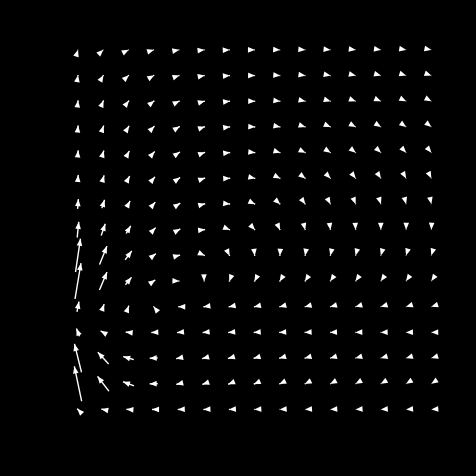

```mathematica
ListVectorPlot[uxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black]
```

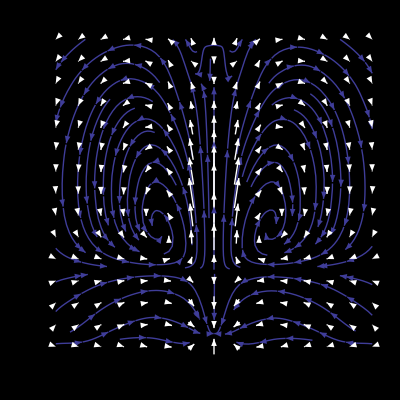

```mathematica
Show[ListStreamPlot[uxz5Point,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[uxz5Point,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

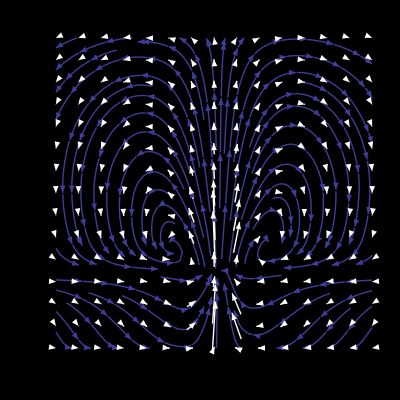

```mathematica
Show[ListStreamPlot[uxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[uxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

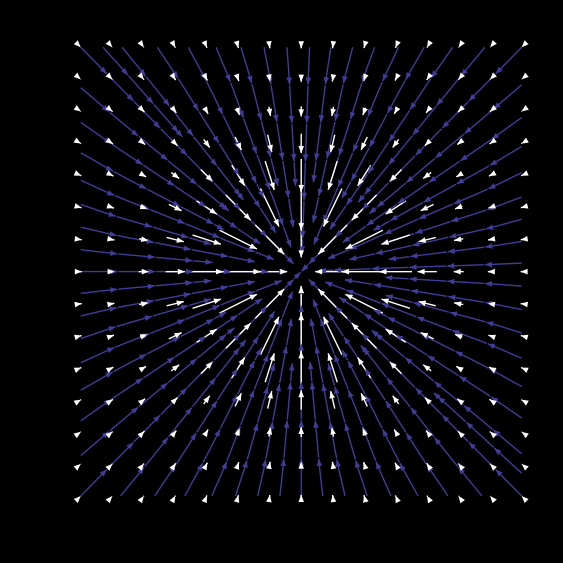

```mathematica
Show[ListStreamPlot[uxy5Point,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[uxy5Point,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

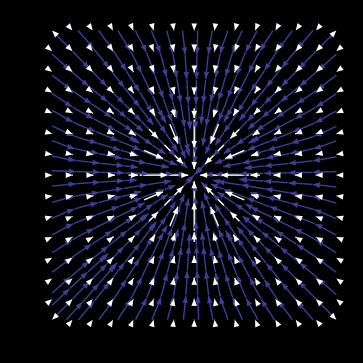

```mathematica
Show[ListStreamPlot[uxy5PointBottom,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[uxy5PointBottom,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

```mathematica
uNhxz9Point=With[{n=9},Table[{u13Nh[i ,0,j ,1,10],u33Nh[i,0,j,1,4 ]},{i,-4,4,1/n},{j,1/n,4,1/n}]];
```

NIntegrate::levmaxord: -32\ π\ x\ Sinh[2\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[« 1 »/9]\ (« 1 »)\ Sinh[8\ π\ x] + 1/9\ (4\ Cosh[2\ π\ x/9]\ Sinh[2\ π\ x] + 8\ π\ x\ Sinh[6\ π\ x]\ Sinh[70\ π\ x/9] - Cosh[52\ π\ x/9]\ Sinh[8\ π\ x] + 8\ π\ x\ Cosh[70\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -32\ π\ x\ Sinh[2\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[« 1 »/9]\ (« 1 »)\ Sinh[8\ π\ x] + 1/9\ (4\ Cosh[2\ π\ x/9]\ Sinh[2\ π\ x] + 8\ π\ x\ Sinh[6\ π\ x]\ Sinh[70\ π\ x/9] - Cosh[52\ π\ x/9]\ Sinh[8\ π\ x] + 8\ π\ x\ Cosh[70\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[4\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[« 1 »/9]\ (« 1 »)\ Sinh[8\ π\ x] + 2/9\ (4\ Cosh[4\ π\ x/9]\ Sinh[2\ π\ x] + 8\ π\ x\ Sinh[6\ π\ x]\ Sinh[68\ π\ x/9] - Cosh[50\ π\ x/9]\ Sinh[8\ π\ x] + 8\ π\ x\ Cosh[68\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -32\ π\ x\ Sinh[4\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[« 1 »/9]\ (« 1 »)\ Sinh[8\ π\ x] + 2/9\ (4\ Cosh[4\ π\ x/9]\ Sinh[2\ π\ x] + 8\ π\ x\ Sinh[6\ π\ x]\ Sinh[68\ π\ x/9] - Cosh[50\ π\ x/9]\ Sinh[8\ π\ x] + 8\ π\ x\ Cosh[68\ π\ x/9]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -32\ π\ x\ Sinh[2\ π\ x/3]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[« 1 »/3]\ (« 1 »)\ Sinh[8\ π\ x] + 1/3\ (4\ Cosh[2\ π\ x/3]\ Sinh[2\ π\ x] + 8\ π\ x\ Sinh[6\ π\ x]\ Sinh[22\ π\ x/3] - Cosh[16\ π\ x/3]\ Sinh[8\ π\ x] + 8\ π\ x\ Cosh[22\ π\ x/3]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -32\ π\ x\ Sinh[2\ π\ x/3]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + 4\ Sinh[« 1 »/3]\ (« 1 »)\ Sinh[8\ π\ x] + 1/3\ (4\ Cosh[2\ π\ x/3]\ Sinh[2\ π\ x] + 8\ π\ x\ Sinh[6\ π\ x]\ Sinh[22\ π\ x/3] - Cosh[16\ π\ x/3]\ Sinh[8\ π\ x] + 8\ π\ x\ Cosh[22\ π\ x/3]\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x]) 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x} = {0.425722} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00469413 和 1.20865×10^-14.

NIntegrate::ncvb: 在接近 {x} = {0.459835} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00492286 和 1.31597×10^-14.

NIntegrate::ncvb: 在接近 {x} = {0.416657} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0117583 和 3.14224×10^-14.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

Power::infy: 碰到无穷表达式 1/0.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

Power::infy: 碰到无穷表达式 1/0.

General::stop: 在本次计算中，Power :: infy 的进一步输出将被抑制.

Infinity::indet: 碰到不定表达式 0\ ComplexInfinity.

General::stop: 在本次计算中，Infinity :: indet 的进一步输出将被抑制.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

General::stop: 在本次计算中，NIntegrate :: izero 的进一步输出将被抑制.

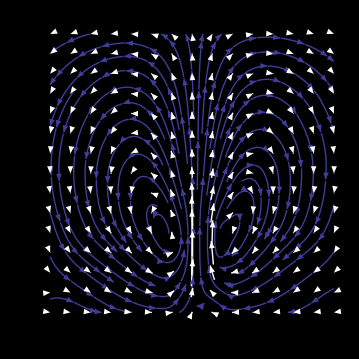

```mathematica
Show[ListStreamPlot[uNhxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[uNhxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

```mathematica
(* H取(4,8,12)*)
UNhxz9Point={};
Do[
uNhxz9Point=With[{n=9.0},Table[{u13Nh[i ,0,j ,1,H],u33Nh[i,0,j,1,H ]},{i,-4+1/(1+n),4,4/n},{j,1/n,4,4/n}]];UNhxz9Point=Append[UNhxz9Point,uNhxz9Point];Print["H=",H],{H,{2,3,4,10}}];
```

NIntegrate::levmaxord: -8\ π\ x\ Sinh[0.698132\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x]) + 2\ Sinh[« 19 »\ x]\ « 1 »\ Sinh[4\ π\ x] + 0.111111\ (2\ Cosh[0.698132\ x]\ Sinh[2\ π\ x] + « 3 » + 4\ π\ x\ Cosh[11.8682\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x])\ Sinh[4\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -8\ π\ x\ Sinh[0.698132\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x]) + 2\ Sinh[« 19 »\ x]\ « 1 »\ Sinh[4\ π\ x] + 0.111111\ (2\ Cosh[0.698132\ x]\ Sinh[2\ π\ x] + « 3 » + 4\ π\ x\ Cosh[11.8682\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x])\ Sinh[4\ π\ x]) 视为非 Levin 函数处理.

NIntegrate::levmaxord: -8\ π\ x\ Sinh[3.49066\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x]) + « 1 » + 0.555556\ (2\ Cosh[3.49066\ x]\ Sinh[2\ π\ x] + 4\ π\ x\ Sinh[« 1 »]\ Sinh[2\ π\ x] - « 1 » + 4\ π\ x\ Cosh[9.07571\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x])\ Sinh[4\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -8\ π\ x\ Sinh[3.49066\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x]) + « 1 » + 0.555556\ (2\ Cosh[3.49066\ x]\ Sinh[2\ π\ x] + 4\ π\ x\ Sinh[« 1 »]\ Sinh[2\ π\ x] - « 1 » + 4\ π\ x\ Cosh[9.07571\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x])\ Sinh[4\ π\ x]) 视为非 Levin 函数处理.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {0.0658219} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -3.81466×10^-20 和 1.69325×10^-18.

NIntegrate::ncvb: 在接近 {x} = {0.398857} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.00218582 和 8.22632×10^-15.

NIntegrate::levmaxord: -8\ π\ x\ Sinh[9.07571\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x]) + « 1 » + 1.44444\ (2\ Cosh[9.07571\ x]\ Sinh[2\ π\ x] + 4\ π\ x\ Sinh[« 1 »]\ Sinh[2\ π\ x] - « 1 » + 4\ π\ x\ Cosh[3.49066\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x])\ Sinh[4\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -8\ π\ x\ Sinh[9.07571\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x]) + « 1 » + 1.44444\ (2\ Cosh[9.07571\ x]\ Sinh[2\ π\ x] + 4\ π\ x\ Sinh[« 1 »]\ Sinh[2\ π\ x] - « 1 » + 4\ π\ x\ Cosh[3.49066\ x]\ (Cosh[2\ π\ x]\ Csch[4\ π\ x] - 2\ Coth[4\ π\ x]\ Csch[4\ π\ x]\ Sinh[2\ π\ x])\ Sinh[4\ π\ x]) 视为非 Levin 函数处理.

General::stop: 在本次计算中，NIntegrate :: levmaxord 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {0.0658219} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -3.72954×10^-19 和 1.89462×10^-18.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate :: slwcon 的进一步输出将被抑制.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

H=2

H=3

H=4

H=10

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

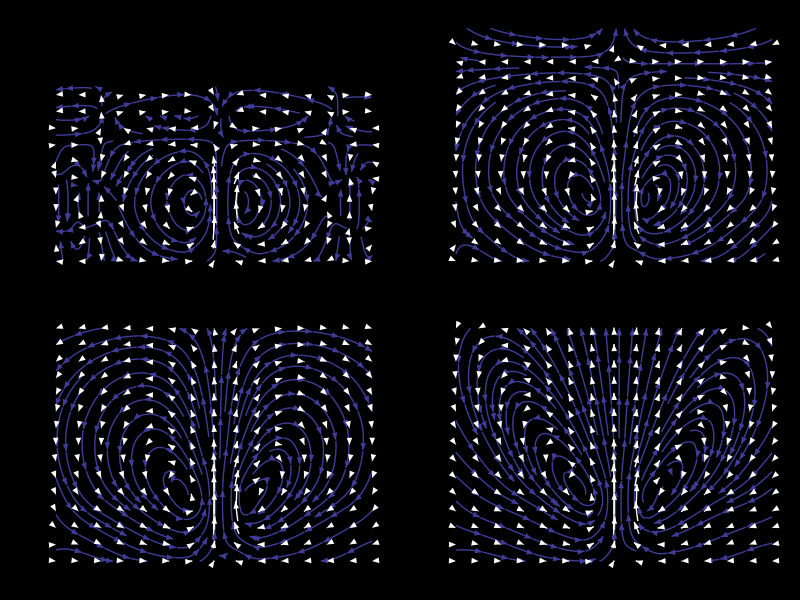

```mathematica
Grid[Partition[Table[Show[ListStreamPlot[UNhxz9Point[[n]],VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[UNhxz9Point[[n]],VectorStyle->White,FrameStyle->LightGray,Background->Black]],{n,1,4}],2]]
```

```mathematica
u11xy5PointHeight4=With[{n=5},Table[{u11Nh[i ,j,1.1,1,4 ],u21Nh[i,j,1.1,1,4 ]},{i,-4-1/(n+1),4+1/(n+1),4/n},{j,-4-1/(n+1),4+1/(n+1),4/n}]];
u11xy5PointHeight8=With[{n=5},Table[{u11Nh[i ,j,1.1,1,8 ],u21Nh[i,j,1.1,1,8 ]},{i,-4-1/(n+1),4+1/(n+1),4/n},{j,-4-1/(n+1),4+1/(n+1),4/n}]];
```

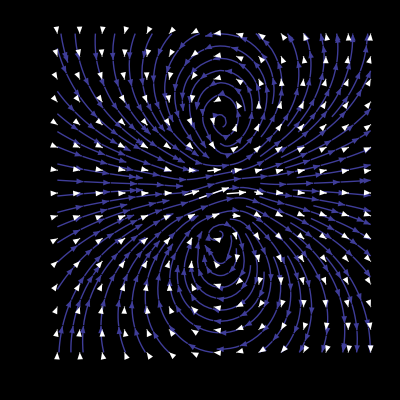

```mathematica
Show[ListStreamPlot[u11xy5PointHeight4,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[u11xy5PointHeight4,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

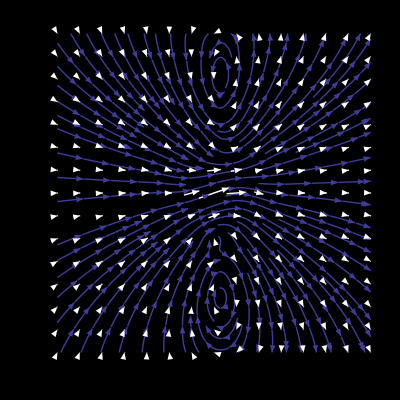

```mathematica
Show[ListStreamPlot[u11xy5PointHeight8,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[u11xy5PointHeight8,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

```mathematica
u11xy5PointHeight2=With[{n=5},Table[{u11Nh[i ,j,1.1,1,2 ],u21Nh[i,j,1.1,1,2 ]},{i,-4-1/(n+1),4+1/(n+1),4/n},{j,-4-1/(n+1),4+1/(n+1),4/n}]];
```

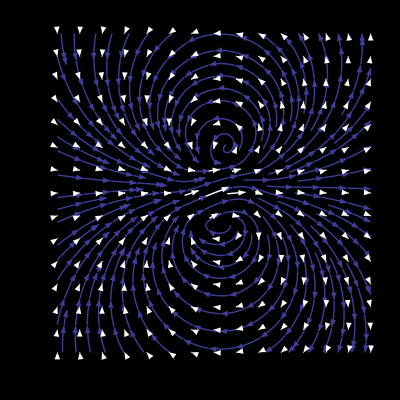

{{{0.00180753,0.025124},{0.00961361,0.0288688},{0.0212589,0.0303873},{0.0357489,0.0269839},{0.0489172,0.0164182},{0.054414,0.},{0.0489172,-0.0164182},{0.0357489,-0.0269839},{0.0212589,-0.0303873},{0.00961361,-0.0288688},{0.00180753,-0.025124}},{{-0.00337734,0.0288688},{0.00586511,0.0361596},{0.0227055,0.042278},{0.0480332,0.0420258},{0.07513,0.0280635},{0.0876143,0.},{0.07513,-0.0280635},{0.0480332,-0.0420258},{0.0227055,-0.042278},{0.00586511,-0.0361596},{-0.00337734,-0.0288688}},{{-0.0111542,0.0303873},{-0.00195668,0.042278},{0.0202407,0.0570449},{0.0639036,0.0675346},{0.124286,0.0531483},{0.157341,0.},{0.124286,-0.0531483},{0.0639036,-0.0675346},{0.0202407,-0.0570449},{-0.00195668,-0.042278},{-0.0111542,-0.0303873}},{{-0.0209174,0.0269839},{-0.0150055,0.0420258},{0.00762478,0.0675346},{0.0726349,0.103311},{0.211148,0.110936},{0.319816,0.},{0.211148,-0.110936},{0.0726349,-0.103311},{0.00762478,-0.0675346},{-0.0150055,-0.0420258},{-0.0209174,-0.0269839}},{{-0.0298901,0.0164182},{-0.0301081,0.0280635},{-0.0174424,0.0531483},{0.0447438,0.110936},{0.31309,0.224289},{0.859798,0.},{0.31309,-0.224289},{0.0447438,-0.110936},{-0.0174424,-0.0531483},{-0.0301081,-0.0280635},{-0.0298901,-0.0164182}},{{-0.0336652,0.},{-0.0373721,0.},{-0.0333756,0.},{0.00510113,0.},{0.238301,0.},{Indeterminate,Indeterminate},{0.238301,0.},{0.00510113,0.},{-0.0333756,0.},{-0.0373721,0.},{-0.0336652,0.}},{{-0.0298901,-0.0164182},{-0.0301081,-0.0280635},{-0.0174424,-0.0531483},{0.0447438,-0.110936},{0.31309,-0.224289},{0.859798,0.},{0.31309,0.224289},{0.0447438,0.110936},{-0.0174424,0.0531483},{-0.0301081,0.0280635},{-0.0298901,0.0164182}},{{-0.0209174,-0.0269839},{-0.0150055,-0.0420258},{0.00762478,-0.0675346},{0.0726349,-0.103311},{0.211148,-0.110936},{0.319816,0.},{0.211148,0.110936},{0.0726349,0.103311},{0.00762478,0.0675346},{-0.0150055,0.0420258},{-0.0209174,0.0269839}},{{-0.0111542,-0.0303873},{-0.00195668,-0.042278},{0.0202407,-0.0570449},{0.0639036,-0.0675346},{0.124286,-0.0531483},{0.157341,0.},{0.124286,0.0531483},{0.0639036,0.0675346},{0.0202407,0.0570449},{-0.00195668,0.042278},{-0.0111542,0.0303873}},{{-0.00337734,-0.0288688},{0.00586511,-0.0361596},{0.0227055,-0.042278},{0.0480332,-0.0420258},{0.07513,-0.0280635},{0.0876143,0.},{0.07513,0.0280635},{0.0480332,0.0420258},{0.0227055,0.042278},{0.00586511,0.0361596},{-0.00337734,0.0288688}},{{0.00180753,-0.025124},{0.00961361,-0.0288688},{0.0212589,-0.0303873},{0.0357489,-0.0269839},{0.0489172,-0.0164182},{0.054414,0.},{0.0489172,0.0164182},{0.0357489,0.0269839},{0.0212589,0.0303873},{0.00961361,0.0288688},{0.00180753,0.025124}}}

```mathematica
Show[ListStreamPlot[u11xy5PointHeight2,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[u11xy5PointHeight2,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

```mathematica
u11Nh[-3 ,-3,1.1,1,4]
```

0.00796195

```mathematica
u11xy5PointHeight4
```

{{{-7.35175×10^11,-7.35175×10^11},{-4.33789×10^13,-3.47031×10^13},{1.63914×10^13,9.83483×10^12},{7.13046×10^13,2.85218×10^13},{-1.27543×10^13,-2.55085×10^12},{4.56769×10^13,0.},{-1.27543×10^13,2.55085×10^12},{7.13046×10^13,-2.85218×10^13},{1.63914×10^13,-9.83483×10^12},{-4.33789×10^13,3.47031×10^13},{-7.35175×10^11,7.35175×10^11}},{{-2.77625×10^13,-3.47031×10^13},{8.2901×10^11,8.2901×10^11},{2.92332×10^13,2.19249×10^13},{-3.69866×10^13,-1.84933×10^13},{1.04945×10^14,2.62363×10^13},{2.95451×10^13,0.},{1.04945×10^14,-2.62363×10^13},{-3.69866×10^13,1.84933×10^13},{2.92332×10^13,-2.19249×10^13},{8.2901×10^11,-8.2901×10^11},{-2.77625×10^13,3.47031×10^13}},{{5.9009×10^12,9.83483×10^12},{1.64437×10^13,2.19249×10^13},{-3.55618×10^13,-3.55618×10^13},{-2.65615×10^13,-1.77077×10^13},{-2.76952×10^13,-9.23172×10^12},{4.28095×10^13,0.},{-2.76952×10^13,9.23172×10^12},{-2.65615×10^13,1.77077×10^13},{-3.55618×10^13,3.55618×10^13},{1.64437×10^13,-2.19249×10^13},{5.9009×10^12,-9.83483×10^12}},{{1.14087×10^13,2.85218×10^13},{-9.24665×10^12,-1.84933×10^13},{-1.18051×10^13,-1.77077×10^13},{3.59094×10^13,3.59094×10^13},{-5.35146×10^13,-2.67573×10^13},{-1.24378×10^13,0.},{-5.35146×10^13,2.67573×10^13},{3.59094×10^13,-3.59094×10^13},{-1.18051×10^13,1.77077×10^13},{-9.24665×10^12,1.84933×10^13},{1.14087×10^13,-2.85218×10^13}},{{-5.1017×10^11,-2.55085×10^12},{6.55908×10^12,2.62363×10^13},{-3.07724×10^12,-9.23172×10^12},{-1.33786×10^13,-2.67573×10^13},{-1.13639×10^13,-1.13639×10^13},{1.16683×10^13,0.},{-1.13639×10^13,1.13639×10^13},{-1.33786×10^13,2.67573×10^13},{-3.07724×10^12,9.23172×10^12},{6.55908×10^12,-2.62363×10^13},{-5.1017×10^11,2.55085×10^12}},{{-0.0318104,0.},{-0.0354885,0.},{-0.0321617,0.},{0.00378691,0.},{0.234373,0.},{Indeterminate,Indeterminate},{0.234373,0.},{0.00378691,0.},{-0.0321617,0.},{-0.0354885,0.},{-0.0318104,0.}},{{-5.1017×10^11,2.55085×10^12},{6.55908×10^12,-2.62363×10^13},{-3.07724×10^12,9.23172×10^12},{-1.33786×10^13,2.67573×10^13},{-1.13639×10^13,1.13639×10^13},{1.16683×10^13,0.},{-1.13639×10^13,-1.13639×10^13},{-1.33786×10^13,-2.67573×10^13},{-3.07724×10^12,-9.23172×10^12},{6.55908×10^12,2.62363×10^13},{-5.1017×10^11,-2.55085×10^12}},{{1.14087×10^13,-2.85218×10^13},{-9.24665×10^12,1.84933×10^13},{-1.18051×10^13,1.77077×10^13},{3.59094×10^13,-3.59094×10^13},{-5.35146×10^13,2.67573×10^13},{-1.24378×10^13,0.},{-5.35146×10^13,-2.67573×10^13},{3.59094×10^13,3.59094×10^13},{-1.18051×10^13,-1.77077×10^13},{-9.24665×10^12,-1.84933×10^13},{1.14087×10^13,2.85218×10^13}},{{5.9009×10^12,-9.83483×10^12},{1.64437×10^13,-2.19249×10^13},{-3.55618×10^13,3.55618×10^13},{-2.65615×10^13,1.77077×10^13},{-2.76952×10^13,9.23172×10^12},{4.28095×10^13,0.},{-2.76952×10^13,-9.23172×10^12},{-2.65615×10^13,-1.77077×10^13},{-3.55618×10^13,-3.55618×10^13},{1.64437×10^13,2.19249×10^13},{5.9009×10^12,9.83483×10^12}},{{-2.77625×10^13,3.47031×10^13},{8.2901×10^11,-8.2901×10^11},{2.92332×10^13,-2.19249×10^13},{-3.69866×10^13,1.84933×10^13},{1.04945×10^14,-2.62363×10^13},{2.95451×10^13,0.},{1.04945×10^14,2.62363×10^13},{-3.69866×10^13,-1.84933×10^13},{2.92332×10^13,2.19249×10^13},{8.2901×10^11,8.2901×10^11},{-2.77625×10^13,-3.47031×10^13}},{{-7.35175×10^11,7.35175×10^11},{-4.33789×10^13,3.47031×10^13},{1.63914×10^13,-9.83483×10^12},{7.13046×10^13,-2.85218×10^13},{-1.27543×10^13,2.55085×10^12},{4.56769×10^13,0.},{-1.27543×10^13,-2.55085×10^12},{7.13046×10^13,2.85218×10^13},{1.63914×10^13,9.83483×10^12},{-4.33789×10^13,-3.47031×10^13},{-7.35175×10^11,-7.35175×10^11}}}

```mathematica
UNhxz9Point[[1,1]]
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

{{-0.0000913438,8.34686×10^-6},{-0.000182937,0.00010569},{3.81466×10^-20,-0.00311986},{0.000182937,0.00010569},{0.0000913438,8.34686×10^-6},{0,0},{0,0},{0,0},{0,0}}

```mathematica
DeleteCases[{1,1,x,2,3,y,9,y},_Rationals]
```

{1,1,x,2,3,y,9,y}

```mathematica
?x
```

Global`x

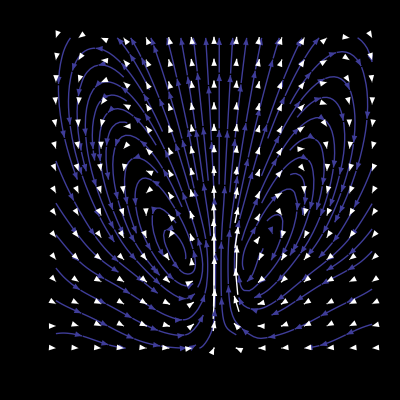

```mathematica
Show[ListStreamPlot[uNhxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black],
ListVectorPlot[uNhxz9Point,VectorStyle->White,FrameStyle->LightGray,Background->Black]]
```

```mathematica
NIntegrate[BesselJ[0,√(0.6800000000000002^2+0^2) x] x raSinh2[x,0.2,0.8,0.5200000000000001],{x,0,400},WorkingPrecision->15,AccuracyGoal->6,Method->{Automatic,"SymbolicProcessing"->False}]
```

0.146411408013693

```mathematica
u13[h0,0,0,h0,4 h0]
```

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

0.

```mathematica
h0
```

0.2

```mathematica
sh[x,h0,4h0,h0]
```

0.168856

```mathematica
x
```

1.18762

```mathematica
f
```

6

```mathematica
w13@@{r1,r2,x3,h,H}
```

NIntegrate::inumr: 在以 {{0, 400}} 为界的区域内，对于所有采样点，计算被积函数 x^2\ « 1 »\ (H\ (-h + H)\ Sinh[h\ x]\ Sinh[x\ x3] - « 1 » - « 1 » + H\ x\ x3\ (H\ Csch[H\ x]\ Sinh[h\ x]\ Sinh[x\ Plus[« 2 »]] + h\ Sinh[x\ Plus[« 2 »]]))/-H^2\ x^2 + Sinh[H\ x]^2 得到非数值.

1/(√(r1^2+r2^2))r1 NIntegrate[BesselJ[1,√(r1^2+r2^2) x] x a4[x,h,H,x3],{x,0,400},Method→GaussKronrodRule]

```mathematica
w33[h0,h0,h0,h0,4 h0]
```

NIntegrate::levmaxord: -0.64\ x\ Sinh[0.2\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[0.2\ x]\ « 1 »\ Sinh[0.8\ x] + 0.2\ (0.8\ Cosh[0.2\ x]\ Sinh[0.2\ x] + « 4 ») 是一个微分阶数为 51 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 -0.64\ x\ Sinh[0.2\ x]\ (0.6\ Cosh[0.6\ x]\ Csch[0.8\ x] - 0.8\ Coth[0.8\ x]\ Csch[0.8\ x]\ Sinh[0.6\ x]) + 0.8\ Sinh[0.2\ x]\ « 1 »\ Sinh[0.8\ x] + 0.2\ (0.8\ Cosh[0.2\ x]\ Sinh[0.2\ x] + « 4 ») 视为非 Levin 函数处理.

-0.290835

```mathematica
u13[0.1h0 ,0,0.1h0 ,h0,4 h0]
```

-0.235753

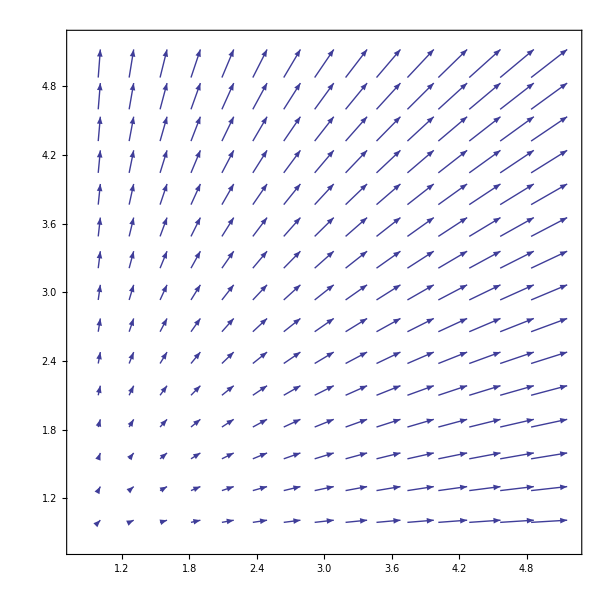

```mathematica
ListVectorPlot[With[{n=5},Table[{i,j},{i,h0/n,4(h0),4h0/n},{j,h0/n,3h0,(3h0)/n}]]]
```

```mathematica
Plot[BesselJ[0,2Pi x+Pi/4],{x,0,10}]
```

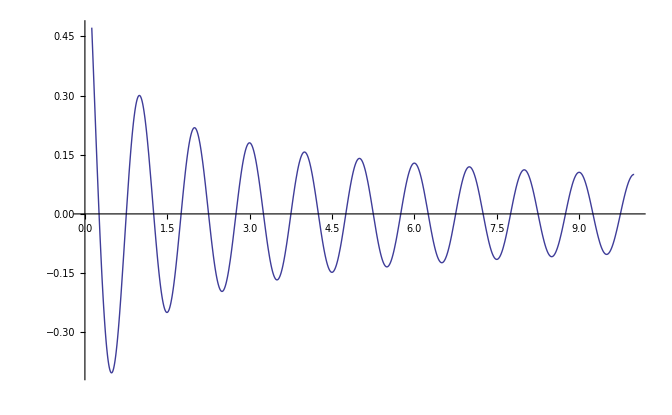
```mathematica
-Graphics-\
```

```mathematica
j0sh[r1_,r2_,x3_,h_,H_]:=With[{k=2Pi/h},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi x]sh[x k,h,H h,x3 h],{x,0,3}]];
```

```mathematica
j0sh[1,1,2,h0,4]
```

0.591576

```mathematica
xz=With[{n=100},Table[4h]]
```

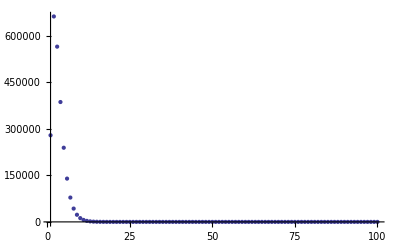

```mathematica
ListPlot[With[{n=100},Table[x j0sh[1,1,x,h0,4],{x,1/100,4,4/100}]],PlotRange->All]
```

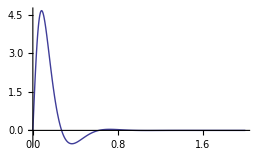

```mathematica
Plot[k BesselJ[0,√(r1^2+r2^2)2Pi x]sh[x k,h,H h,x3 h]/.{r1->1,r2->1,h->h0,H->4,k->2Pi/h0,x3->2},{x,0,2},PlotRange->All]
```

```mathematica
raSinh2[x 2Pi/h0,h0,H h0,x3 h0]
```

(0.2 H-0.2 x3) Cosh[31.4159 x (0.2 H-0.2 x3)] Csch[6.28319 H x] Sinh[6.28319 x]+0.2 Cosh[6.28319 x] Csch[6.28319 H x] Sinh[31.4159 x (0.2 H-0.2 x3)]-0.2 H Coth[6.28319 H x] Csch[6.28319 H x] Sinh[6.28319 x] Sinh[31.4159 x (0.2 H-0.2 x3)]

```mathematica
raSinh2[x,h0,H h0,x3 h0]/.x->2Pi/h0 y
```

(0.2 H-0.2 x3) Cosh[31.4159 (0.2 H-0.2 x3) y] Csch[6.28319 H y] Sinh[6.28319 y]+0.2 Cosh[6.28319 y] Csch[6.28319 H y] Sinh[31.4159 (0.2 H-0.2 x3) y]-0.2 H Coth[6.28319 H y] Csch[6.28319 H y] Sinh[6.28319 y] Sinh[31.4159 (0.2 H-0.2 x3) y]

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ π\ x]\ Sinh[2\ (-h\ (-1 + H)\ (-0.0000204286 + H) + h\ (-1 + H)\ H)\ π\ x/h\ (-1 + H)]/h^2\ (-1 + H)^2 得到非数值.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ π\ x]\ Sinh[2\ (-1.00004\ h + h\ H)\ π\ x/h]/h^2 得到非数值.

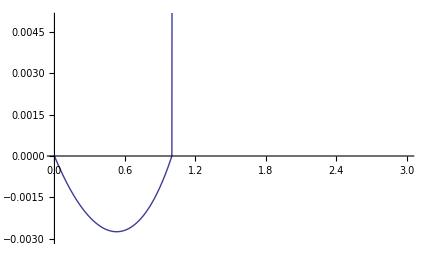

```mathematica
Show[Plot[((x3-1)h v13Nh[r1,r2,H-x3,(H-1)h,H])/.{r1->1,r2->1,H->4,h->h0},{x3,0,1},PlotRange->{{0,3},{-0.003,0.005}}],Plot[((x3-1)h v13Nh[r1,r2,x3,h,H])/.{r1->1,r2->1,H->4,h->h0},{x3,1,3}]]
```

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ π\ x]\ Sinh[2\ (-1.00004\ h + h\ H)\ π\ x/h]/h^2 得到非数值.

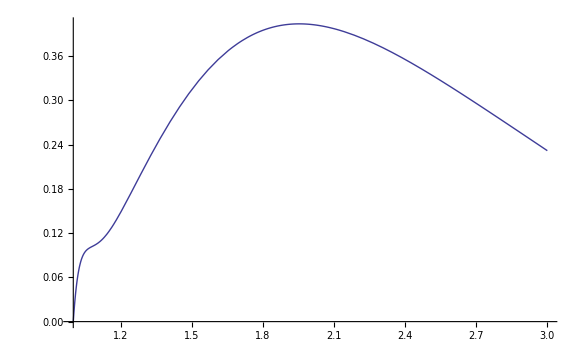

```mathematica
Plot[((x3-1)h v13Nh[r1,r2,x3,h,H])/.{r1->1,r2->1,H->4,h->h0},{x3,1,3}]
```

```mathematica
k=2Pi/h0;
j1xshNh[r1_,r2_,x3_,h_,H_]:=Print[NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h,H h,x3 h],{x,0,5}]]
0.01j1xshNh[1,1,1.01,h0,4]
-0.01j1xshNh[1,1,3.01,3h0,4]
```

```mathematica
sh[x k ,h,H h,x3 h]-sh[x k, (H-1)h,H h,(H-x3)h]
```

-Csch[31.4159 h H x] Sinh[31.4159 h (-1+H) x] Sinh[31.4159 x (h H-h (H-x3))]+Csch[31.4159 h H x] Sinh[31.4159 h x] Sinh[31.4159 x (h H-h x3)]

```mathematica
Simplify[-Csch[31.41592653589793 h H x] Sinh[31.41592653589793 h (-1+H) x] Sinh[31.41592653589793 x (h H-h (H-x3))]+Csch[31.41592653589793 h H x] Sinh[31.41592653589793 h x] Sinh[31.41592653589793 x (h H-h x3)]]
```

Cosh[31.4159 h x x3] Sinh[31.4159 h x]-Cosh[31.4159 h x] Sinh[31.4159 h x x3]

```mathematica
Manipulate[Plot[Cosh[31.41592653589793 h x x3] Sinh[31.41592653589793 h x]/Cosh[31.41592653589793 h x] Sinh[31.41592653589793 h x x3],{x,-8,8}],{h,{0.2}},{x3,0,1}]
```

```mathematica
Manipulate[With[{k=2Pi/h},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h,H h,x3 h]/.{h->h0,H->4,x3->1.01,r1->1,r2->1},{x,0,xm}]],{xm,2,500}]
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

NIntegrate::inumr: 在以 {{0, 2.}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ √2\ π\ x]\ sh[2\ π\ x/h0, h0, 4\ h0, 1.01\ h0]/h0^2 得到非数值.

NIntegrate::inumr: 在以 {{0,2.}} 为界的区域内，对于所有采样点，计算被积函数 (4 π^2 x BesselJ[1,2 √2 π x] sh[(2 π x)/h0,h0,4 h0,1.01 h0])/h0^2 得到非数值.

NIntegrate::levtime: 求解线性系统时在 LevinRule 中花费的时间超过了 10. 秒. 请尝试增加 " TimeConstraint " 选项的值，或者降低 " Points " 选项的值.

NIntegrate::mtdfb: 使用 LevinRule 的数值积分失效. 积分过程使用 Method -> GaussKronrodRule 继续.

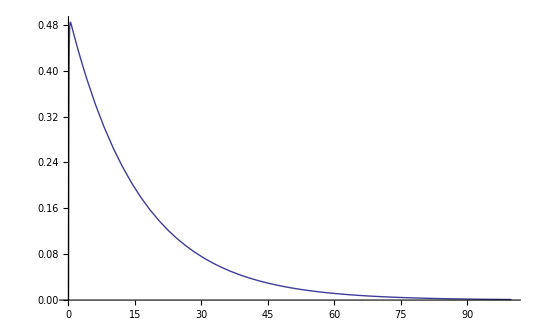

```mathematica
Plot[With[{k=2Pi/h},sh[x k,h,H h0,x3 h]/.{h->h0,H->4,x3->0.99}],{x,0,100},PlotRange->All]
```

```mathematica
With[{k=2Pi/h},  sh[x k ,h,H h,x3 h]]
```

Csch[2 H π x] Sinh[2 π x] Sinh[(2 π x (h H-h x3))/h]

```mathematica
Simplify[Csch[2 H π x] Sinh[2 π x] Sinh[(2 π x (h H-h x3))/h]]
```

Csch[2 H π x] Sinh[2 π x] Sinh[2 π x (H-x3)]

```mathematica
Manipulate[Plot[x Csch[2 H π x] Sinh[2 π x] Sinh[2 π x (H-x3)],{x,0,2}],{H,4,8},{x3,0,H}]
```

```mathematica
sh[x k,(H-1)h,H h,(H-x3)h]-sh[x k ,h,H h,x3 h]
```

Csch[h H k x] Sinh[h (-1+H) k x] Sinh[k x (h H-h (H-x3))]-Csch[h H k x] Sinh[h k x] Sinh[k x (h H-h x3)]

```mathematica
Simplify[Csch[h H k x] Sinh[h (-1+H) k x] Sinh[k x (h H-h (H-x3))]/(Csch[h H k x] Sinh[h k x] Sinh[k x (h H-h x3)])]
```

Csch[h k x] Csch[h k x (H-x3)] Sinh[h (-1+H) k x] Sinh[h k x x3]

```mathematica
Manipulate[Plot[Csch[h k x] Csch[h k x (H-x3)] Sinh[h (-1+H) k x] Sinh[h k x x3],{x,0,8}],{h,0,8},{H,2,4},{k,-2,2},{x3,-2,2}]
```

```mathematica
Manipulate[Plot[Sinh[h k x (-1+x3)],{x,-8,8}],{h,-8,8},{k,-2,2},{x3,-2,2}]
```

```mathematica
Simplify[Csch[h H k x] Sinh[h (-1+H) k x] Sinh[k x (h H-h (H-x3))]]
```

Csch[h H k x] Sinh[h (-1+H) k x] Sinh[h k x x3]

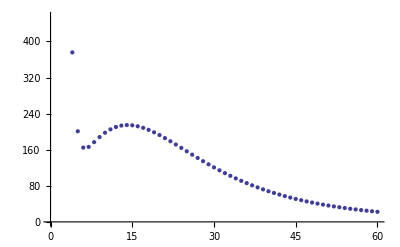

```mathematica
ListPlot[v13Nh[1,1,#,h0,10]&/@xz]
```

```mathematica
w13Nh[r1_,r2_,x3_,h_,H_]:=r1/(√(r1^2+r2^2))j1xa4Nh[##]&[r1,r2,x3,h,H];
```

```mathematica
With[{s0=0.2},With[{k=2Pi/s0},Print[s0," and ",k]]]
```

0.2 and 31.4159

```mathematica
2*N[Pi,8]
```

6.2831853

```mathematica
N[π,7]
```

3.141593

```mathematica
j0shNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[BesselJ[0,k √(r1^2+r2^2)2Pi x]sh[x k,h h0,H h0,x3 h0],{x,0,4}]]];
```

```mathematica
U13Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},Piecewise[{{0,x3==h},
{(x3-1)h0 v13Nh[r1,r2,x3,h,H],H>x3>  h},{(x3-1)h0 v13Nh[r1,r2,H-x3,H-h,H],x3<h}}]];
```

```mathematica
sss=U13Nh[1,1,#,1,4]&/@xz;//Timing
```

{1.90625,Null}

Parallelize::nopar1: Show[Plot[Evaluate[#1[1, 1, x, 1, 4]] &\ {U13Nh, u13Nh}, {x, 0, 3}]] cannot be parallelized; proceeding with sequential evaluation.

-Graphics-

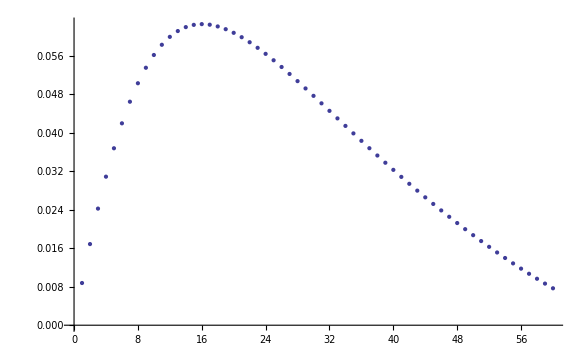

```mathematica
ListPlot[(U13Nh[1,1,#,1,4]-u13Nh[1,1,#,1,4])&/@xz]
```

```mathematica
With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,20},Method->{Automatic,"SymbolicProcessing"->False}]]]/.{r1->1,r2->2,H->4,x3->1.1,h->1}//Timing
```

NIntegrate::inumr: 在以 {{0, 20}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

{0.20313,0.0593513}

```mathematica
With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,20},Method->{Automatic,"SymbolicProcessing"->False}]]]/.{r1->1,r2->2,H->4,x3->2,h->1}//Timing
```

NIntegrate::inumr: 在以 {{0, 20}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

{0.09375,0.0512307}

```mathematica
With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,2},Method->{Automatic,"SymbolicProcessing"->False}]]]/.{r1->1,r2->2,H->4,x3->2,h->1}//Timing
```

NIntegrate::inumr: 在以 {{0, 2}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

{0.0625,0.051231}

```mathematica
ClearSystemCache[];Timing[With[{h0=h0},With[{k=(2 π)/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2) 2 π x] k x sh[x k,h h0,H h0,x3 h0],{x,0,20},Method->{Automatic,"SymbolicProcessing"->False}]]]/.{r1->1,r2->2,H->4,x3->1.1,h->1}]
```

NIntegrate::inumr: 在以 {{0, 20}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

{0.1875,0.0593513}

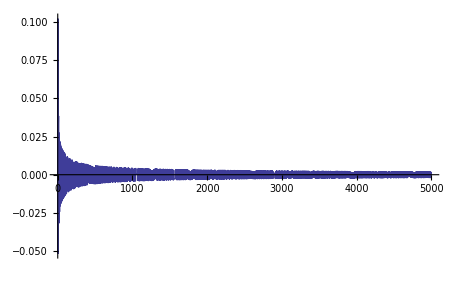

{-0.00910259,-0.0172227,-0.0243407,-0.030441,-0.035512,-0.0395466,-0.042542,-0.0445011,-0.0454336,-0.0453567,-0.0442978,-0.0422969,-0.0394141,-0.0357463,-0.031472,-0.0269535,-0.0229155,-0.0204392,-0.0187564,0,0.0189222,0.0211033,0.024414,0.0296284,0.0356733,0.0418345,0.0477624,0.0532932,0.0583469,0.0628822,0.0668797,0.0703342,0.0732517,0.075647,0.0775418,0.0789633,0.0799424,0.0805126,0.0807088,0.0805661,0.0801192,0.0794018,0.0784457,0.077281,0.0759357,0.0744353,0.072803,0.0710597,0.069224,0.0673123,0.0653391,0.0633167,0.0612559,0.0591656,0.0570533,0.0549253,0.0527863,0.0506401,0.0484895,0.0463364}

```mathematica
Plot[ BesselJ[0,√(r1^2+r2^2) 2Pi*x]sh[x k,h h0,H h0,x3 h0]/.{r1->1,r2->1,H->4,x3->1,h->1},{x,0,5000},PlotRange->All]
```

```mathematica
First[{0.046875`4.691541194015399,0.}]
```

0.04688

```mathematica
If
```

```mathematica
x>4
```

```mathematica
Divergence[{u11Nh[r1,r2,x3,h,H],u21Nh[r1,r2,x3,h,H],u31Nh[r1,r2,x3,h,H]},{r1,r2,x3}]
```

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ (x3\ (-H\ Cosh[2\ π\ x\ x3]\ Sinh[2\ h\ π\ x] + h\ Cosh[2\ π\ x\ Plus[« 3 »]]\ Sinh[2\ H\ π\ x]) + « 4 »)/-4\ H^2\ π^2\ x^2 + Sinh[2\ H\ π\ x]^2 得到非数值.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 8\ π^3\ x^2\ BesselJ[0, 2\ π\ √r1^2 + r2^2\ x]\ (x3\ (-H\ Cosh[2\ π\ x\ x3]\ Sinh[2\ h\ π\ x] + h\ Cosh[2\ π\ x\ Plus[« 3 »]]\ Sinh[2\ H\ π\ x]) + « 4 »)/-4\ H^2\ π^2\ x^2 + Sinh[2\ H\ π\ x]^2 得到非数值.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 BesselJ[0, 4\ π^2\ √r1^2 + r2^2\ x]\ Csch[2\ H\ π\ x]\ Sinh[2\ h\ π\ x]\ Sinh[2\ π\ x\ (H - x3)] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

Divergence[{Piecewise[{{(√h (r1^2-r2^2) NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/((r1^2+r2^2)^(3/2))-(r1^2 NIntegrate[(2 π) BesselJ[0,√(r1^2+r2^2) 2 π x] ((2 π) x)^2 a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(r1^2+r2^2)+NIntegrate[BesselJ[0,(2 π) √(r1^2+r2^2) 2 π x] sh[x (2 π),h 1,H 1,x3 1],{x,0,4}]+1/(√(r1^2+r2^2))h r1^2 NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x sh[x (2 π),h 1,H 1,x3 1],{x,0,20},Method→{Automatic,SymbolicProcessing→False}], H>x3≥1}, {(√h (r1^2-r2^2) NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/((r1^2+r2^2)^(3/2))-(r1^2 NIntegrate[(2 π) BesselJ[0,√(r1^2+r2^2) 2 π x] ((2 π) x)^2 a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(r1^2+r2^2)+NIntegrate[BesselJ[0,(2 π) √(r1^2+r2^2) 2 π x] sh[x (2 π),h (-1+H),H 1,(H-x3) 1],{x,0,4}]+1/(√(r1^2+r2^2))h (-1+H) r1^2 NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x sh[x (2 π),h (-1+H),H 1,(H-x3) 1],{x,0,20},Method→{Automatic,SymbolicProcessing→False}], x3<1}, {0, True}}],Piecewise[{{(2 √h r1 r2 NIntegrate[(2 π) BesselJ[1,√(r2^2+r1^2) 2 π x] (2 π) x a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/((r1^2+r2^2)^(3/2))-(r1 r2 NIntegrate[(2 π) BesselJ[0,√(r2^2+r1^2) 2 π x] ((2 π) x)^2 a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(r1^2+r2^2)+1/(√(r1^2+r2^2))r1 r2 NIntegrate[(2 π) BesselJ[1,√(r2^2+r1^2) 2 π x] (2 π) x sh[x (2 π),h 1,H 1,x3 1],{x,0,20},Method→{Automatic,SymbolicProcessing→False}], H>x3≥1}, {(2 √h r1 r2 NIntegrate[(2 π) BesselJ[1,√(r2^2+r1^2) 2 π x] (2 π) x a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/((r1^2+r2^2)^(3/2))-(r1 r2 NIntegrate[(2 π) BesselJ[0,√(r2^2+r1^2) 2 π x] ((2 π) x)^2 a1[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(r1^2+r2^2)+1/(√(r1^2+r2^2))r1 r2 NIntegrate[(2 π) BesselJ[1,√(r2^2+r1^2) 2 π x] (2 π) x sh[x (2 π),h (-1+H),H 1,(H-x3) 1],{x,0,20},Method→{Automatic,SymbolicProcessing→False}], x3<1}, {0, True}}],Piecewise[{{(r1 NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x a4s[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(√(r1^2+r2^2)), x3==1}, {(r1 NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x a4s[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(√(r1^2+r2^2))+1/(√(r1^2+r2^2))r1 (-h+x3) NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x sh[x (2 π),h 1,H 1,x3 1],{x,0,20},Method→{Automatic,SymbolicProcessing→False}], H>x3>1}, {(r1 NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x a4s[x (2 π),h 1,H 1,x3 1],{x,0,4}])/(√(r1^2+r2^2))+1/(√(r1^2+r2^2))r1 (-h+x3) NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x sh[x (2 π),(-h+H) 1,H 1,(H-x3) 1],{x,0,20},Method→{Automatic,SymbolicProcessing→False}], x3<1}, {0, True}}]},{r1,r2,x3}]

```mathematica
w11Nh[r1,r2,x3,h,H]
```

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ π\ √r1^2 + r2^2\ x]\ (x3\ (-H\ Cosh[2\ π\ x\ x3]\ Sinh[2\ h\ π\ x] + h\ Cosh[2\ π\ x\ Plus[« 3 »]]\ Sinh[2\ H\ π\ x]) + « 4 »)/-4\ H^2\ π^2\ x^2 + Sinh[2\ H\ π\ x]^2 得到非数值.

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ Null^2\ π^2\ x\ BesselJ[0, 2\ π\ √r1^2 + r2^2\ x]\ (x3\ (-H\ Cosh[2\ π\ x\ x3]\ Sinh[2\ h\ π\ x] + h\ Cosh[2\ π\ x\ Plus[« 3 »]]\ Sinh[2\ H\ π\ x]) + « 4 »)/-4\ H^2\ π^2\ x^2 + Sinh[2\ H\ π\ x]^2 得到非数值.

-1/(r1^2+r2^2)r1^2 NIntegrate[(2 π) BesselJ[0,√(r1^2+r2^2) 2 π x] ((2 π) x) Null^2 a1[x (2 π),h 1,H 1,x3 1],{x,0,4}]+1/((r1^2+r2^2)^(3/2))√h (r1^2-r2^2) NIntegrate[(2 π) BesselJ[1,√(r1^2+r2^2) 2 π x] (2 π) x a1[x (2 π),h 1,H 1,x3 1],{x,0,4}]

```mathematica
j0x2a1Nh[r1,r2,x3,h,H]
```

NIntegrate::inumr: 在以 {{0, 4}} 为界的区域内，对于所有采样点，计算被积函数 4\ Null^2\ π^2\ x\ BesselJ[0, 2\ π\ √r1^2 + r2^2\ x]\ (x3\ (-H\ Cosh[2\ π\ x\ x3]\ Sinh[2\ h\ π\ x] + h\ Cosh[2\ π\ x\ Plus[« 3 »]]\ Sinh[2\ H\ π\ x]) + « 4 »)/-4\ H^2\ π^2\ x^2 + Sinh[2\ H\ π\ x]^2 得到非数值.

NIntegrate[(2 π) BesselJ[0,√(r1^2+r2^2) 2 π x] ((2 π) x) Null^2 a1[x (2 π),h 1,H 1,x3 1],{x,0,4}]

```mathematica
k BesselJ[0,√(r1^2+r2^2)2Pi x](k x)^2 a1[x k ,h h0,H h0,x3 h0]
```

1/(-4 H^2 π^2 x^2+Sinh[2 H π x]^2)4 Null^2 π^2 x BesselJ[0,2 π √(r1^2+r2^2) x] (x3 (-H Cosh[2 π x x3] Sinh[2 h π x]+h Cosh[2 π x (-h+H-x3)] Sinh[2 H π x])+2 H π x x3 Cosh[2 π x (H-x3)] Sinh[2 H π x] ((-h+H) Cosh[2 (-h+H) π x] Csch[2 H π x]-H Coth[2 H π x] Csch[2 H π x] Sinh[2 (-h+H) π x])+2 h H π x x3 Sinh[2 (-h+H) π x] Sinh[2 π x (H-x3)]-H ((h Cosh[2 h π x] Csch[2 H π x]-H Coth[2 H π x] Csch[2 H π x] Sinh[2 h π x]) Sinh[2 H π x]+2 H π x ((-h+H) Cosh[2 (-h+H) π x] Csch[2 H π x]-H Coth[2 H π x] Csch[2 H π x] Sinh[2 (-h+H) π x])) Sinh[2 π x x3])

```mathematica
(k*x)^2
```

2 Null^2 π x

```mathematica
k+1
```

1+2 π

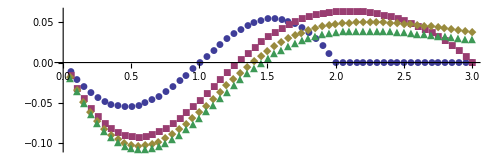

```mathematica
ListPlot[U13[[#]]&/@Range[Length@U31],PlotMarkers->Automatic,AspectRatio->1/3]
```

```mathematica
U31[[1]]
```

{-0.000128902,-0.000506578,-0.00110608,-0.00188563,-0.00279246,-0.00376663,-0.0047447,-0.00566324,-0.00646201,-0.00708701,-0.00749297,-0.00764556,-0.00752308,-0.00711756,-0.00643525,-0.00549637,-0.00433426,-0.00299333,-0.00142964,0.,0.00142964,0.00299333,0.00433426,0.00549637,0.00643525,0.00711756,0.00752308,0.00764556,0.00749297,0.00708701,0.00646201,0.00566324,0.0047447,0.00376663,0.00279246,0.00188563,0.00110608,0.000506578,0.000128902,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
u33Nh[1,1,1.1,1,4]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {1.32781} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0000124513 和 0.000055822.

-1.02739

```mathematica
j0a2Nh[1,1,1.1,1,4]
j0shNh[1,1,1.1,1,4]
```

-0.308545

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {1.32781} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0000124513 和 0.000055822.

-0.0000124513

```mathematica
j0a2Nh[1,1,1.1,1,4]+j0shNh[1,1,1.1,1,4]-j0xdshNh[1,1,1.1,1,4]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {1.32781} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0000124513 和 0.000055822.

-1.02739

```mathematica
ssss[x3_]:=If[x3>1.0,ssss[x3]=NIntegrate[BesselJ[0,(2 π) √(1^2+1^2) 2 π x] sh[x (2 π),1 1,4 1,x3 1],{x,0,4},Method->{Automatic,"SymbolicProcessing"->False}]-NIntegrate[BesselJ[0,(2 π) √(1^2+1^2) 2 π x] sh[x (2 π),1 1,4 1,x3 1],{x,0,20},Method->{Automatic,"SymbolicProcessing"->False}],0]
```

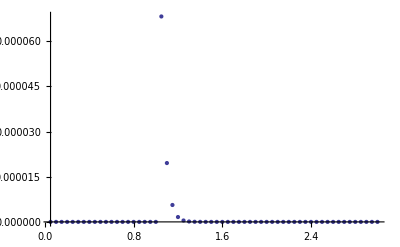

```mathematica
ListPlot[Transpose@Append[{xz},ssss[#]&/@xz],PlotRange->All]
```

```mathematica
ssss[0.1]
```

0

```mathematica
xz[[1]]
```

0.05

```mathematica
1+1/E//N
```

1.36788

```mathematica
ssss[1.01]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {1.32781} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -0.0000151797 和 1.40172×10^-10.

0.000217004

```mathematica
ssss[x3_]:=ssss[x3]=NIntegrate[BesselJ[0,(2 π) √(1^2+1^2) 2 π x] sh[x (2 π),1 1,4 1,x3 1],{x,0,4},Method->{Automatic,"SymbolicProcessing"->False}]
```

```mathematica
Gamma
```

```mathematica
j0shNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,k √(r1^2+r2^2)2Pi x]sh[x k,h h0,H h0,x3 h0],{x,0,100},Method->{Automatic,"SymbolicProcessing"->False},MaxRecursion->12,PrecisionGoal->12]]];
```

```mathematica
j0shNhNearh[1,1,1.1,1,4]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {1.58744} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -6.36429×10^-8 和 1.52936×10^-6.

-6.36429×10^-8

```mathematica
j0shNh[1,1,1.02,1,4]
```

0.714436

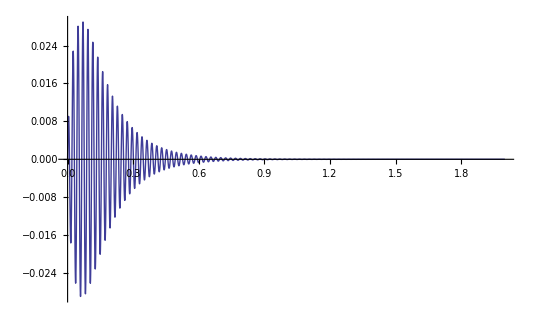

```mathematica
Plot[BesselJ[0,31.41592653589793 √(1^2+1^2) 2 π x] sh[x 31.41592653589793,1 0.2,4 0.2,2 0.2],{x,0,2},PlotRange->All]
```

```mathematica
NIntegrate[k BesselJ[0,k √(r1^2+r2^2)2Pi x]sh[x k,h h0,H h0,x3 h0]/.{r1->1,r2->1,H->4,x3->2,h->1},{x,0,4}]
```

```mathematica
NIntegrate[31.41592653589793 BesselJ[0,31.41592653589793 √(1^2+1^2) 2 π x] sh[x k,1 0.2,4 0.2,2 0.2],{x,0,4}]
```

-4.70063×10^-6

```mathematica
us=u11Nh[1,1,#,1,4]&/@xz;
```

```mathematica
us={-0.011200519832449797,-0.024521389810842318,-0.039483897959135705,-0.0556527767640805,-0.07264010839244617,-0.09010658917800912,-0.10776078369607048,-0.12535695526372276,-0.1426918384344896,-0.1596009577722019,-0.17595461664941608,-0.19165408076569096,-0.20662267240746773,-0.22081481424099236,-0.23419768319399756,-0.24675604774221643,-0.258487667392877,-0.26939781102217647,-0.27803929092491064,-3.9165651285771705,1.0276367093357146,1.0397222917987483,1.0367476403777234,1.0286195164016514,1.0156376752233507,0.9981422249949523,0.97652249338737,0.951203834552233,0.9226317581135695,0.8912663641150693,0.8575648758605239,0.8219737618510184,0.7849202138582334,0.7468056839667536,0.7080010595060819,0.6688435882744399,0.6296353023648639,0.5906427256407308,0.5520976154688052,0.5141985155772059,0.4771128853600836,0.4409796153838532,0.4059117610926188,0.3719993593208817,0.33931222220496393,0.307902630349853,0.2778078707551699,0.24905258466463004,0.2216509063485534,0.19560838598135188,0.17092369887332498,0.14759014970841755,0.12559698468630193,0.10493052700676153,0.08557515237138846,0.06751412145264274,0.050730285872229164,0.035206683361129476,0.02092703661359724,0.00787616902544458};
```

```mathematica
uw=w11Nh[1,1,#,1,4]&/@xz;
```

```mathematica
uv=If[#<1,j0shNh[1,1,4-#,3,4],j0shNh[1,1,#,1,4]]&/@xz;
```

```mathematica
uv2=If[#<1,j1xshNh[1,1,4-#,3,4],j1xshNh[1,1,#,1,4]]&/@xz;
```

```mathematica
uv3=If[#<1,v11Nh[1,1,4-#,3,4],v11Nh[1,1,#,1,4]]&/@xz;
```

```mathematica
Plot[v11Nh[1,1,x,1,4],{x,1,2}]
```

$Aborted

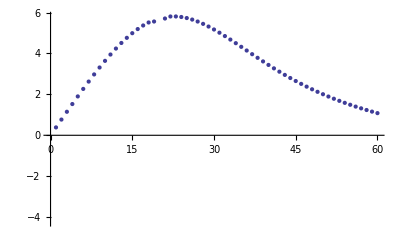

```mathematica
ListPlot[uv+uv2]
```

```mathematica
z
```

```mathematica
j0shNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2) 2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,1,20},Method->{Automatic,"SymbolicProcessing"->False},MaxRecursion->12,PrecisionGoal->12]]];
```

```mathematica
j0shNh[1,1,0\,1,4]
```

0.725639

```mathematica
j0shNhNearh[1,1,1.,1,4]
```

0.790536

```mathematica
v11Nh[j0shNh,1,3.01,3,4]
```

NIntegrate::ncvb: 在接近 {x} = {0.422135} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.0252282 和 4.45254×10^-14.

0.302472

```mathematica
Clear[j0shNh]
```

```mathematica
j0shNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},If[x3<h+1/N[E],j0shNhNearh[r1,r2,x3,h,H],NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,4},WorkingPrecision->12,AccuracyGoal->10]]]];
```

```mathematica
s=If[#>1,j0shNh[3,4,#,1,4],j0shNh[3,4,4-#,3,4]]&/@xz
```

NIntegrate::ncvb: 在接近 {x} = {0.310546} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.00286598 和 3.23842×10^-15.

NIntegrate::ncvb: 在接近 {x} = {0.310546} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.000860744 和 1.24119×10^-14.

```mathematica
sss={0.00034953724323280852080998669661016575`12.,0.00069666039323288820342477167406826165`12.,0.00103898105945631063457811888292741362`12.,0.00137414585751013119605436100777908954`12.,0.00169985590071711143609403694962842042`12.,0.00201372866126616390142469711637789109`12.,0.002314308034516451,0.002598931357098596,0.0028659766400345493,0.0008607444057401239,0.003340734252872268,0.003545535363321386,0.0037269530719437,0.00388374932090131530595438373517140154`12.,0.00401577772516406236125331734312890767`12.,0.00412175305927811341900408545787772175`12.,0.00420138958620212993132338299786590972`12.,0.00425446275594439425935237083535967778`12.,0.00428085183003766808930466832037152581`12.,0.0042806468230164603474410840886132108`12.,0.00425409706273069955772495275638849953`12.,0.00420161502971579266691356371722219831`12.,0.00412375830552461123484550238827005715`12.,0.00402123020312237028092087126290325641`12.,0.00389486581282632557120041035023744634`12.,0.00374562270007076830033203023104444258`12.,0.0035745709794874504347484335624603647`12.,0.00338288336915817419822761745403447044`12.,0.00317182540149378326143204179276378146`12.,0.00294275069301812724956674148706384772`12.};
```

```mathematica
NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] sh[x (2 π),3 1,4 1,3.9 1],{x,0,4},WorkingPrecision->12,AccuracyGoal->10]
```

0.000349537243233

```mathematica
ss=w11Nh[3,4,#,1,4]&/@xz
```

{-0.00165114,-0.00322592,-0.00472363,-0.00614354,-0.00748486,-0.00874673,-0.00992824,-0.0110284,-0.0120461,-0.0129804,-0.0138301,-0.014594,-0.0152711,-0.0158603,-0.0163605,-0.0167708,-0.0170903,-0.0173182,-0.0174538,-0.0174968,-0.0174467,-0.0173034,-0.0170669,-0.0167376,-0.0163158,-0.0158023,-0.0151981,-0.0145044,-0.0137226,-0.0128546}

```mathematica
j0shNh[3,4,1,1,4]
```

NIntegrate::ncvb: 在接近 {x} = {0.310546} 处的 x 中进行 12 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0.000860744 和 1.22521×10^-14.

0.000860744

```mathematica
Manipulate[Plot[If[x3>1,BesselJ[0,√(3^2+4^2)2Pi*x]sh[x 2Pi,1 h0,10h0,x3 h0],BesselJ[0,√(3^2+4^2)2Pi*x]sh[x 2Pi,9h0,10h0,(10-x3) h0]],{x,0,4},PlotRange->All],{x3,xz}]
```

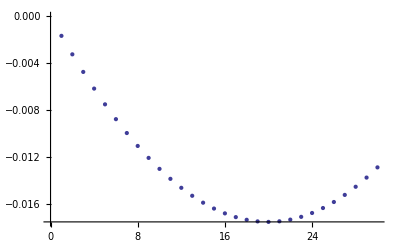

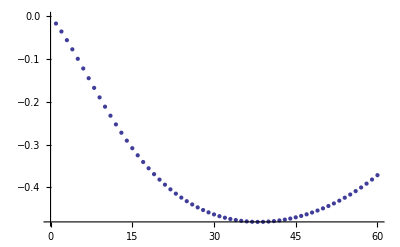

```mathematica
ListPlot[ss]
```

```mathematica
u12Nh[1,1,1,1,4]
```

-21.9565

```mathematica
NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] sh[x (2 π),9 1,10 1,9.9 1],{x,0,4},WorkingPrecision->12,AccuracyGoal->10,Method->{Automatic,"SymbolicProcessing"->False}]
```

0.000702329309122

```mathematica
(w11Nh[0.1,0.1,0.5,1,4 ]+v11Nh[0.1,0.1,4 -0.5,4 -1,4 ])
```

0.485397

```mathematica
ss =u11Nh[1,1,#,1,4]&/@xz
```

{0.0154456,0.0304102,0.0449312,0.0590356,0.0727378,0.0860391,0.0989269,0.111375,0.123346,0.13479,0.145647,0.155852,0.165334,0.17402,0.181839,0.188724,0.194617,0.199464,0.201289,-0.783313,0.205527,0.207944,0.20735,0.205724,0.203128,0.199628,0.195304,0.190241,0.184526,0.178253,0.171513,0.164395,0.156984,0.149361,0.1416,0.133769,0.125927,0.118129,0.11042,0.10284,0.0954226,0.0881959,0.0811824,0.0743999,0.0678624,0.0615805,0.0555616,0.0498105,0.0443302,0.0391217,0.0341847,0.029518,0.0251194,0.0209861,0.017115,0.0135028,0.0101461,0.00704134,0.00418541,0.00157523,-0.00079193,-0.00291849,-0.00480644,-0.00645737,-0.0078724,-0.00905217,-0.0099968,-0.0107059,-0.0111786,-0.0114135,-0.0114086,-0.0111614,-0.0106689,-0.00992755,-0.00893345,-0.00768209,-0.00616855,-0.00438752,-0.00233333,0}

```mathematica
Length[%43]
```

80

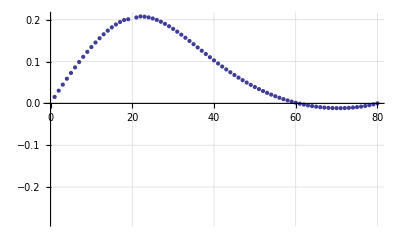

```mathematica
ListPlot[ss,GridLines->Automatic]
```

```mathematica
sh[x,h,H,h]
```

Csch[H x] Sinh[h x] Sinh[(-h+H) x]

```mathematica
Manipulate[Plot[Csch[H x] Sinh[h x] Sinh[(-h+H) x],{x,0,80},PlotRange->All],{h,0,5},{H,h,8}]
```

```mathematica
Manipulate[Plot[r f[x k0/r,h h0,H h0,z h0]BesselJ[n,2Pi √2 x]m,{x,0,xmax},PlotRange->{{-1/2 xmax,xmax},All},Epilog->Inset[Column[{Text[Style["H="<>ToString[H],14,Bold]],Text[Style["h="<>ToString[h],14,Bold]],Text[Style["z="<>ToString[z],14,Bold]],Text[Style["ρ="<>ToString[r],14,Bold]],Text[Style["xmax="<>ToString[xmax],14,Bold]]}],Scaled[{1/5.1,0.7}]],PlotLabel->Row[{Style["f",Italic],"=",PopupMenu[Dynamic[f],{sh,raSinh2}],PopupMenu[Dynamic[m],{1,x,x^2}],"BesselJ",PopupMenu[Dynamic[n],{0,1}]}]],{z,h,H},{h,0,H},{H,2,10,1},{xmax,{10,100,1000}},{r,0.5,10}]
```

```mathematica
Manipulate[Plot[r^2 f[x k0/r,h h0,H h0,z h0]BesselJ[n,2Pi √2 x]m[x k0/r,h h0,H h0,z h0]l,{x,0,xmax},PlotRange->{{-1/2 xmax,xmax},All},Epilog->Inset[Column[{Text[Style["H="<>ToString[H],14,Bold]],Text[Style["h="<>ToString[h],14,Bold]],Text[Style["z="<>ToString[z],14,Bold]],Text[Style["ρ="<>ToString[r],14,Bold]],Text[Style["xmax="<>ToString[xmax],14,Bold]]}],Scaled[{1/5.1,0.7}]],PlotLabel->Row[{Style["f",Italic],"=",PopupMenu[Dynamic[f],{sh,raSinh2}],PopupMenu[Dynamic[m],{a0,a1,a1,a2, a4, a4s}],PopupMenu[Dynamic[l],{1,x,x^2}],"BesselJ",PopupMenu[Dynamic[n],{0,1}]}]],{z,h,H},{h,0,H},{H,2,10,1},{xmax,{10,100,1000}},{r,0.5,25}]
```

```mathematica
a0[x_,h_,x3_,H_]:=1
```

```mathematica
a1[x,1,4,1]*x^2-sh[x,1,4,1]
```

-Csch[4 x] Sinh[x] Sinh[3 x]+1/(-16 x^2+Sinh[4 x]^2)x^2 (-4 Cosh[x] Sinh[x]+4 x Sinh[3 x]^2+Cosh[2 x] Sinh[4 x]+4 x Cosh[3 x] (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x]) Sinh[4 x]-4 Sinh[x] (4 x (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x])+(Cosh[x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[x]) Sinh[4 x]))

```mathematica
∂_x %148
```

-3 Cosh[3 x] Csch[4 x] Sinh[x]-Cosh[x] Csch[4 x] Sinh[3 x]+4 Coth[4 x] Csch[4 x] Sinh[x] Sinh[3 x]-1/((-16 x^2+Sinh[4 x]^2)^2)x^2 (-32 x+8 Cosh[4 x] Sinh[4 x]) (-4 Cosh[x] Sinh[x]+4 x Sinh[3 x]^2+Cosh[2 x] Sinh[4 x]+4 x Cosh[3 x] (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x]) Sinh[4 x]-4 Sinh[x] (4 x (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x])+(Cosh[x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[x]) Sinh[4 x]))+1/(-16 x^2+Sinh[4 x]^2)2 x (-4 Cosh[x] Sinh[x]+4 x Sinh[3 x]^2+Cosh[2 x] Sinh[4 x]+4 x Cosh[3 x] (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x]) Sinh[4 x]-4 Sinh[x] (4 x (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x])+(Cosh[x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[x]) Sinh[4 x]))+1/(-16 x^2+Sinh[4 x]^2)x^2 (-4 Cosh[x]^2+4 Cosh[2 x] Cosh[4 x]-4 Sinh[x]^2+24 x Cosh[3 x] Sinh[3 x]+4 Sinh[3 x]^2+16 x Cosh[3 x] Cosh[4 x] (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x])+2 Sinh[2 x] Sinh[4 x]+4 Cosh[3 x] (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x]) Sinh[4 x]+12 x Sinh[3 x] (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x]) Sinh[4 x]+4 x Cosh[3 x] (-24 Cosh[3 x] Coth[4 x] Csch[4 x]+9 Csch[4 x] Sinh[3 x]+16 Coth[4 x]^2 Csch[4 x] Sinh[3 x]+16 Csch[4 x]^3 Sinh[3 x]) Sinh[4 x]-4 Cosh[x] (4 x (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x])+(Cosh[x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[x]) Sinh[4 x])-4 Sinh[x] (4 Cosh[4 x] (Cosh[x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[x])+4 (3 Cosh[3 x] Csch[4 x]-4 Coth[4 x] Csch[4 x] Sinh[3 x])+4 x (-24 Cosh[3 x] Coth[4 x] Csch[4 x]+9 Csch[4 x] Sinh[3 x]+16 Coth[4 x]^2 Csch[4 x] Sinh[3 x]+16 Csch[4 x]^3 Sinh[3 x])+(-8 Cosh[x] Coth[4 x] Csch[4 x]+Csch[4 x] Sinh[x]+16 Coth[4 x]^2 Csch[4 x] Sinh[x]+16 Csch[4 x]^3 Sinh[x]) Sinh[4 x]))

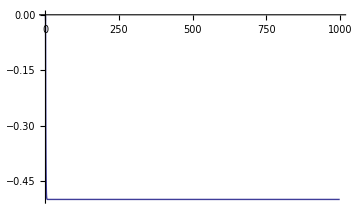

```mathematica
Plot[%148,{x,0,1000},PlotRange->All]
```

```mathematica
NIntegrate[BesselJ[1,x](a1[x,1,4,1]*x^2-sh[x,1,4,1]),{x,40,30}]//N
```

-0.126696

```mathematica
N[1-BesselJ[0,100]]
```

0.980014

```mathematica
Simplify[%137]
```

Csch[H x] (Sinh[h x] Sinh[(-h+H) x]+1/(-2+2 H^2 x^2 Csch[H x]^2)x^2 (-2 h^2 Cosh[(-2 h+H) x]+H Csch[H x] (2 h (h-H) x Cosh[(-h+H) x]^2-2 (h-H) H x Cosh[(-h+H) x] Csch[H x] Sinh[h x]+2 h (Sinh[2 h x]-h x Sinh[(-h+H) x]^2)+H Coth[H x] (1-Cosh[2 h x]-2 H x Csch[H x] Sinh[h x] Sinh[(-h+H) x]+h x Sinh[2 (-h+H) x]))))

```mathematica
Simplify[%135]
```

1/(-H^2 x^2+Sinh[H x]^2)(-h (h-H) H x Cosh[(-h+H) x]^2+(h-H) H^2 x Cosh[(-h+H) x] Csch[H x] Sinh[h x]+h (-H Sinh[2 h x]+h Cosh[(-2 h+H) x] Sinh[H x]+h H x Sinh[(-h+H) x]^2)+1/2 H^2 Coth[H x] (2 Sinh[h x]^2+2 H x Csch[H x] Sinh[h x] Sinh[(-h+H) x]-h x Sinh[2 (-h+H) x]))

```mathematica
u11Nh[1,1,0.9,1,4]
```

0.199463

```mathematica
0.002/0.199
```

0.0100503

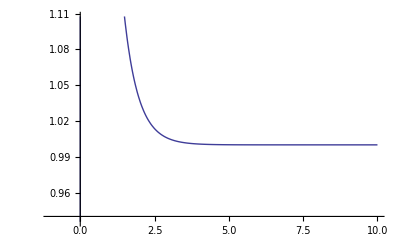

u11Nh

```mathematica
Plot[Coth[x],{x,-1,10}]
```

```mathematica
u33Nh[1,1,1.1,1,4]
```

-0.0603478

```mathematica
0.08341890183401218-NIntegrate[(2 π) BesselJ[0,√(1^2+1^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,4 1,1.1 1],{x,0,20}]
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

```mathematica
0.08341890183401218-NIntegrate[(2 π) BesselJ[0,√(1^2+1^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,4 1,1.1 1],{x,0,20},Method->{Automatic,"SymbolicProcessing"->False}]
```

-0.0590047

```mathematica
u11Nh[3,4,1.4,1,4]
```

NIntegrate::levmaxord: 35.1858\ x\ Sinh[16.3363\ x]\ Sinh[6\ π\ x] + « 4 » 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 35.1858\ x\ Sinh[16.3363\ x]\ Sinh[6\ π\ x] + « 4 » 视为非 Levin 函数处理.

-0.00572589

```mathematica
j0shNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,Infinity}]]];
```

NIntegrate::nconv: 振荡积分可能不是收敛的.

General::stop: 在本次计算中，NIntegrate :: nconv 的进一步输出将被抑制.

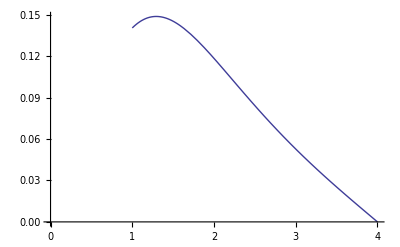

```mathematica
Plot[j0shNh[1,1,z,1,4],{z,0,4}]
```

```mathematica
j0xdshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi x]k x raSinh2[x k ,h h0,H h0,x3 h0],{x,0,Infinity}(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]];
```

```mathematica
j0xdshNh[3,4,1,1,4]//AbsoluteTiming
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {2.02526} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 4.68309×10^-12 和 1.05659×10^-17.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {2.13131} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.36552×10^-12 和 1.28352×10^-17.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate :: slwcon 的进一步输出将被抑制.

NIntegrate::ncvb: 在接近 {x} = {2.23931} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 3.97715×10^-13 和 1.09084×10^-17.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

{2.09432,0.0109325}

```mathematica
j0shNh[3,4,1,1,4]
```

0.00086074440574

```mathematica
U12[1]
```

NIntegrate::nconv: 振荡积分可能不是收敛的.

General::stop: 在本次计算中，NIntegrate :: nconv 的进一步输出将被抑制.

{{{0.05,0.0216928},{0.1,0.0415553},{0.15,0.0597533},{0.2,0.0764391},{0.25,0.0917492},{0.3,0.105803},{0.35,0.1187},{0.4,0.130524},{0.45,0.141338},{0.5,0.151191},{0.55,0.160114},{0.6,0.168125},{0.65,0.175232},{0.7,0.18143},{0.75,0.186711},{0.8,0.191061},{0.85,0.194465},{0.9,0.196909},{0.95,0.19838},{1.,0.0800659+1/(√2)NIntegrate[(2 π) BesselJ[1,√(1^2+1^2) 2 π x] (2 π) x sh[x (2 π),1 1,2 1,1. 1],{x,0,∞}]},{1.05,0.19838},{1.1,0.196909},{1.15,0.194465},{1.2,0.191061},{1.25,0.186711},{1.3,0.18143},{1.35,0.175232},{1.4,0.168125},{1.45,0.160114},{1.5,0.151191},{1.55,0.141338},{1.6,0.130524},{1.65,0.1187},{1.7,0.105803},{1.75,0.0917492},{1.8,0.0764391},{1.85,0.0597533},{1.9,0.0415553},{1.95,0.0216928},{2.,0},{2.05,0},{2.1,0},{2.15,0},{2.2,0},{2.25,0},{2.3,0},{2.35,0},{2.4,0},{2.45,0},{2.5,0},{2.55,0},{2.6,0},{2.65,0},{2.7,0},{2.75,0},{2.8,0},{2.85,0},{2.9,0},{2.95,0},{3.,0}},{{0.05,0.0192502},{0.1,0.0369705},{0.15,0.0532935},{0.2,0.0683422},{0.25,0.0822279},{0.3,0.0950479},{0.35,0.106884},{0.4,0.117804},{0.45,0.127859},{0.5,0.137086},{0.55,0.145508},{0.6,0.15314},{0.65,0.159983},{0.7,0.166034},{0.75,0.171286},{0.8,0.175728},{0.85,0.179352},{0.9,0.182152},{0.95,0.184129},{1.,0.0458596+1/(√2)NIntegrate[(2 π) BesselJ[1,√(1^2+1^2) 2 π x] (2 π) x sh[x (2 π),1 1,3 1,1. 1],{x,0,∞}]},{1.05,0.185649},{1.1,0.185234},{1.15,0.184078},{1.2,0.182224},{1.25,0.179725},{1.3,0.176636},{1.35,0.173022},{1.4,0.168948},{1.45,0.164482},{1.5,0.159689},{1.55,0.154635},{1.6,0.149381},{1.65,0.143984},{1.7,0.138495},{1.75,0.132959},{1.8,0.127417},{1.85,0.1219},{1.9,0.116435},{1.95,0.111042},{2.,0.105736},{2.05,0.100526},{2.1,0.095416},{2.15,0.0904046},{2.2,0.0854866},{2.25,0.0806525},{2.3,0.0758888},{2.35,0.0711785},{2.4,0.0665008},{2.45,0.0618314},{2.5,0.0571425},{2.55,0.0524025},{2.6,0.047576},{2.65,0.0426231},{2.7,0.0374999},{2.75,0.0321571},{2.8,0.0265399},{2.85,0.0205874},{2.9,0.0142318},{2.95,0.00739744},{3.,0}},{{0.05,0.018703},{0.1,0.0359212},{0.15,0.0517831},{0.2,0.0664081},{0.25,0.0799043},{0.3,0.0923659},{0.35,0.103873},{0.4,0.114488},{0.45,0.124263},{0.5,0.133232},{0.55,0.141416},{0.6,0.148828},{0.65,0.155469},{0.7,0.161333},{0.75,0.166413},{0.8,0.170697},{0.85,0.174176},{0.9,0.176843},{0.95,0.178699},{1.,0.037776+1/(√2)NIntegrate[(2 π) BesselJ[1,√(1^2+1^2) 2 π x] (2 π) x sh[x (2 π),1 1,4 1,1. 1],{x,0,∞}]},{1.05,0.180012},{1.1,0.17951},{1.15,0.178279},{1.2,0.176362},{1.25,0.173811},{1.3,0.170684},{1.35,0.167045},{1.4,0.162961},{1.45,0.158499},{1.5,0.153729},{1.55,0.148717},{1.6,0.143525},{1.65,0.138214},{1.7,0.132837},{1.75,0.127443},{1.8,0.122074},{1.85,0.116769},{1.9,0.111557},{1.95,0.106465},{2.,0.101513},{2.05,0.0967171},{2.1,0.0920895},{2.15,0.087638},{2.2,0.0833674},{2.25,0.0792798},{2.3,0.075375},{2.35,0.0716508},{2.4,0.0681033},{2.45,0.0647276},{2.5,0.0615174},{2.55,0.058466},{2.6,0.0555658},{2.65,0.052809},{2.7,0.0501873},{2.75,0.0476922},{2.8,0.0453153},{2.85,0.0430479},{2.9,0.0408813},{2.95,0.0388069},{3.,0.036816}},{{0.05,0.018469},{0.1,0.0354665},{0.15,0.05112},{0.2,0.0655483},{0.25,0.0788586},{0.3,0.0911446},{0.35,0.102485},{0.4,0.112944},{0.45,0.122569},{0.5,0.131396},{0.55,0.139447},{0.6,0.146732},{0.65,0.153251},{0.7,0.159001},{0.75,0.163972},{0.8,0.168152},{0.85,0.171532},{0.9,0.174105},{0.95,0.17587},{1.,0.0340874+1/(√2)NIntegrate[(2 π) BesselJ[1,√(1^2+1^2) 2 π x] (2 π) x sh[x (2 π),1 1,10 1,1. 1],{x,0,∞}]},{1.05,0.177016},{1.1,0.176436},{1.15,0.17513},{1.2,0.173142},{1.25,0.170523},{1.3,0.167331},{1.35,0.16363},{1.4,0.159487},{1.45,0.15497},{1.5,0.150147},{1.55,0.145084},{1.6,0.139845},{1.65,0.13449},{1.7,0.129071},{1.75,0.123639},{1.8,0.118235},{1.85,0.112898},{1.9,0.107658},{1.95,0.102541},{2.,0.0975688},{2.05,0.0927567},{2.1,0.0881173},{2.15,0.0836588},{2.2,0.0793866},{2.25,0.0753032},{2.3,0.0714089},{2.35,0.067702},{2.4,0.0641795},{2.45,0.0608369},{2.5,0.057669},{2.55,0.0546699},{2.6,0.0518329},{2.65,0.0491514},{2.7,0.0466182},{2.75,0.0442265},{2.8,0.0419691},{2.85,0.039839},{2.9,0.0378295},{2.95,0.035934},{3.,0.034146}}}[1]

```mathematica
j0shNh[3,4,1,1,8]
```

NIntegrate::ncvi: 在区域 {{0., ∞}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 256.614 和 229.088.

256.614

```mathematica
j1xshNh[1,1,1,1,8]
```

NIntegrate::ncvi: 在区域 {{0., ∞}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.31026×10^12 和 5.87538×10^12.

-1.31026×10^12

```mathematica
BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0]/.{r1->1,r2->1,k->2Pi,h->1,x3->1+10^-2,H->8}
```

2 π x BesselJ[1,2 √2 π x] Csch[16 π x] Sinh[2 π x] Sinh[(699 π x)/50]

```mathematica
x Sinh[(2 π)x]Sinh[(2 π)6x]/Sinh[8(2 π)x]
```

x Csch[16 π x] Sinh[2 π x] Sinh[12 π x]

i=2

i=3

i=4

i=10

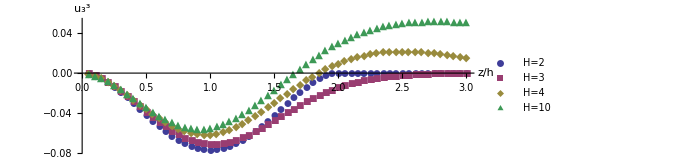

```mathematica
U33={};
Do[uu33=u33Nh[1,1,#,1,i]&/@xz;
uu33=Transpose@{xz,uu33};U33=Append[U33,uu33];Print["i=",i],{i,{2,3,4,10}}];

ListPlot[U33[[#]]&/@Range[Length@U33],PlotMarkers->Automatic,AspectRatio->1/3,AxesLabel->{"z/h","u_3^3"},PlotLegends->Placed[{"H=2","H=3","H=4","H=10"},Above]]
```

```mathematica
j0shNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,Infinity}]]]
j0shNhNearh[3,4,1,1,8]
```

0.00622165

```mathematica
method={Automatic,"DoubleExponential"}
Xmax={4,Infinity}
```

{Automatic,DoubleExponential}

{4,∞}

```mathematica
j0xdshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi x]k x raSinh2[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->{Automatic,"SymbolicProcessing"->False}]]];
j0xdshNh[3,4,1,1,8]
```

0.0133031

```mathematica
(* xmax = Infinity, Method->"DoubleExponential"*)
s=j0xdshNh[3,4,#,1,8]&/@Select[xz,#>1+1/E&]//AbsoluteTiming
```

{1.55879,{0.0169398,0.0173024,0.017644,0.0179643,0.0182635,0.0185415,0.0187984,0.0190344,0.0192495,0.019444,0.0196181,0.0197721,0.0199063,0.0200209,0.0201164,0.0201932,0.0202516,0.0202921,0.0203152,0.0203213,0.020311,0.0202847,0.0202429,0.0201863,0.0201153,0.0200305,0.0199324,0.0198216,0.0196987,0.0195643,0.0194188,0.0192629,0.019097}}

```mathematica
(* xmax = Infinity, Method->{Automatic,"SymbolicProcessing"->False}*)
ss=j0xdshNh[3,4,#,1,8]&/@Select[xz,#>1+1/E&]//AbsoluteTiming
```

{2.40802,{0.0169398,0.0173024,0.017644,0.0179643,0.0182635,0.0185415,0.0187984,0.0190344,0.0192495,0.019444,0.0196181,0.0197721,0.0199062,0.0200209,0.0201164,0.0201932,0.0202516,0.0202921,0.0203152,0.0203213,0.020311,0.0202847,0.0202429,0.0201863,0.0201153,0.0200305,0.0199324,0.0198216,0.0196987,0.0195643,0.0194188,0.0192629,0.019097}}

```mathematica
(* xmax = 4, Method->{Automatic,"SymbolicProcessing"->False} *)
sss=j0xdshNh[3,4,#,1,8]&/@Select[xz,#>1+1/E&]//AbsoluteTiming
```

{2.1633,{0.0169422,0.0173032,0.0176442,0.0179644,0.0182635,0.0185415,0.0187984,0.0190344,0.0192495,0.019444,0.0196181,0.0197721,0.0199063,0.0200209,0.0201164,0.0201932,0.0202516,0.0202921,0.0203152,0.0203213,0.020311,0.0202847,0.0202429,0.0201863,0.0201153,0.0200305,0.0199324,0.0198216,0.0196987,0.0195643,0.0194188,0.0192629,0.019097}}

```mathematica
sss-ss[[8;;]]
```

{2.33246×10^-6,7.52536×10^-7,2.39731×10^-7,7.55848×10^-8,2.36277×10^-8,7.33272×10^-9,2.26159×10^-9,6.93786×10^-10,2.11831×10^-10,6.44086×10^-11,1.93687×10^-11,5.8697×10^-12,1.77115×10^-12,5.32841×10^-13,1.60177×10^-13,4.83849×10^-14,1.49047×10^-14,4.89192×10^-15,1.89779×10^-15,9.67976×10^-16,6.76542×10^-16,5.6552×10^-16,4.96131×10^-16,4.57967×10^-16,4.33681×10^-16,-1.51268×10^-14,-3.83027×10^-15,-5.27356×10^-16,2.77556×10^-16,3.36536×10^-16,2.5327×10^-16,1.80411×10^-16,1.42247×10^-16}

```mathematica
(* xmax = 4, 不指定方法完全算不出来。可能是采用了错误的方法。*)
ssss=j0xdshNh[3,4,#,1,8]&/@Select[xz,#>1+1/E&]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {0.345688} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.38351×10^19 和 1.29127×10^20.

NIntegrate::ncvb: 在接近 {x} = {0.345688} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -4.49639×10^19 和 2.76701×10^19.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::ncvb: 在接近 {x} = {0.345688} 处的 x 中进行 9 次迭代对分后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -6.91753×10^18 和 1.15292×10^19.

General::stop: 在本次计算中，NIntegrate :: ncvb 的进一步输出将被抑制.

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

General::stop: 在本次计算中，NIntegrate :: errprec 的进一步输出将被抑制.

{-1.38351×10^19,-4.49639×10^19,-6.91753×10^18,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.55 1],{x,0,4}],-4.97197×10^18,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.65 1],{x,0,4}],-9.14231×10^17,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.75 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.8 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.85 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.9 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,1.95 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2. 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.05 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.1 1],{x,0,4}],-7.38425×10^14,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.2 1],{x,0,4}],-3.33354×10^13,-8.61506×10^13,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.35 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.4 1],{x,0,4}],1.12338×10^13,2.48007×10^13,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.55 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.6 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.65 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.7 1],{x,0,4}],-8.6083×10^11,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.8 1],{x,0,4}],1.15033×10^11,NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.9 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,2.95 1],{x,0,4}],NIntegrate[(2 π) BesselJ[0,√(3^2+4^2) 2 π x] (2 π) x raSinh2[x (2 π),1 1,8 1,3. 1],{x,0,4}]}

```mathematica
(* xmax = 4, Method->"DoubleExponential" *)
sssss=j0xdshNh[3,4,#,1,8]&/@Select[xz,#>1+1/E&]//AbsoluteTiming
```

{2.40103,{0.0169422,0.0173032,0.0176442,0.0179644,0.0182635,0.0185415,0.0187984,0.0190344,0.0192495,0.019444,0.0196181,0.0197721,0.0199063,0.0200209,0.0201164,0.0201932,0.0202516,0.0202921,0.0203152,0.0203213,0.020311,0.0202847,0.0202429,0.0201863,0.0201153,0.0200305,0.0199324,0.0198216,0.0196987,0.0195643,0.0194188,0.0192629,0.019097}}

```mathematica
Length[Select[xz,#>1&]]
```

40

{1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.}

```mathematica
method[[2]]
```

Method→DoubleExponential

```mathematica
u12Nh[1,1,1,1,8]
```

NIntegrate::ncvi: 在区域 {{0., ∞}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 -1.31026×10^12 和 5.87538×10^12.

0.0342055-1.2619×10^12 ，

```mathematica
j1xshNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->{"GaussKronrodRule","SymbolicProcessing"->False}]]];
```

```mathematica
j1xshNhNearh[1,1,1,1,8]
```

NIntegrate::inumri: 在以 {{0., 4.64782×10^14}} 为界的区域内，对于所有采样点，计算被积函数 4\ π^2\ x\ BesselJ[1, 2\ √2\ π\ x]\ Csch[16\ π\ x]\ Sinh[2\ π\ x]\ Sinh[14\ π\ x] 得到 Overflow、Indeterminate 或者 Infinity.

NIntegrate[(2 π) BesselJ[1,√(1^2+1^2) 2 π x] (2 π) x sh[x (2 π),1 1,8 1,1 1],{x,0,∞},Method→{GaussKronrodRule,SymbolicProcessing→False}]

```mathematica
j1xshNh[1,1,3,1,4]
```

0.0327648

```mathematica
w11Nh[3,4,1.1,1,4]
```

NIntegrate::levmaxord: 27.646\ x\ Sinh[18.2212\ x]\ Sinh[6\ π\ x] + 27.646\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[« 1 »]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[6.9115\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) 是一个微分阶数为 52 的 Levin 函数，它的阶数超过了选项值 "MaxOrder" -> 50. 将 27.646\ x\ Sinh[18.2212\ x]\ Sinh[6\ π\ x] + 27.646\ x\ « 1 »\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[« 1 »]\ Sinh[6\ π\ x])\ Sinh[8\ π\ x] + « 1 » - 4\ Sinh[6.9115\ x]\ (8\ π\ x\ (3\ Cosh[6\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[6\ π\ x]) + (Cosh[2\ π\ x]\ Csch[8\ π\ x] - 4\ Coth[8\ π\ x]\ Csch[8\ π\ x]\ Sinh[2\ π\ x])\ Sinh[8\ π\ x]) 视为非 Levin 函数处理.

-0.0138301

```mathematica
j1xa1Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x a1[x k ,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential" ]]];
```

```mathematica
j1xa1Nh[3,4,1.1,1,8]
```

0.0727542

```mathematica
j0x2a1Nh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi x](k x)^2 a1[x k ,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"]]];
```

```mathematica
j0x2a1Nh[3,4,1,1,8]
```

0.00718136

```mathematica
(* v11=j0sh + f(r)j1xsh *)
(* w11=g(r)j1xa1 + h(r)j0x2a1 *)
```

```mathematica
j0shNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[0,√(r1^2+r2^2)2Pi*x]sh[x k,h h0,H h0,x3 h0],{x,0,Infinity},Method->"DoubleExponentialOscillatory"]]]
```

```mathematica
(* xmax=Infinity, no method*)
Print[j0shNh[1,1,1,1,4]//AbsoluteTiming] 
Print[j0shNhNearh[1,1,1,1,4]//AbsoluteTiming]
```

{1.25589,0.140333}

{1.55711,0.140333}

```mathematica
(* xmax=Infinity, method-> "ExtrapolatingOscillatory"*)
Print[j0shNh[1,1,1,1,4]//AbsoluteTiming] 
Print[j0shNhNearh[1,1,1,1,4]//AbsoluteTiming]
```

{1.30496,0.140333}

{1.57912,0.140333}

```mathematica
(* xmax=Infinity, method-> "DoubleExponentialOscillatory"*)
Print[j0shNh[1,1,1,1,4]//AbsoluteTiming] 
Print[j0shNhNearh[1,1,1,1,4]//AbsoluteTiming]
```

{1.25889,0.140333}

{1.61915,0.140333}

```mathematica
j1xshNhNearh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,Infinity},Method->"ExtrapolatingOscillatory"]]];
```

```mathematica
(* xmax = Infinity, Method->"ExtrapolatingOscillatory" *)
Print[j1xshNh[3,4,1,1,4]//AbsoluteTiming] 
Print[j1xshNhNearh[3,4,1,1,4]//AbsoluteTiming]
```

{1.39499,0.00280923}

NIntegrate::nconv: 振荡积分可能不是收敛的.

{0.52537,NIntegrate[(2 π) BesselJ[1,√(3^2+4^2) 2 π x] (2 π) x sh[x (2 π),1 1,4 1,1 1],{x,0,∞},Method→ExtrapolatingOscillatory]}

```mathematica
v11Nh[1,1,1,1,4]//AbsoluteTiming
```

{0.39328,-0.0763952}

```mathematica
j1xshNh[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},If[x3<h+1/E,j1xshNhNearh[r1,r2,x3+10^-6,h,H],NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]]];
j1xshNhTset[r1_,r2_,x3_,h_,H_]:=With[{h0=h0},With[{k=2Pi/h0},If[x3<h+1/E,j1xshNhNearh[r1,r2,x3,h,H],NIntegrate[k BesselJ[1,√(r1^2+r2^2)2Pi x]k x sh[x k ,h h0,H h0,x3 h0],{x,0,4},Method->"DoubleExponential"(*,Method->{Automatic,"SymbolicProcessing"->False}*)]]]]
```

```mathematica
(* 观察用 x3+10^-6 处的值来代替 x3 处的值所产生的误差。*)
```

```mathematica
s=j1xshNh[1,1,#,1,3]&/@Select[xz,#>1&];//AbsoluteTiming
ss=j1xshNhTset[1,1,#,1,3]&/@Select[xz,#>1&];//AbsoluteTiming
```

NIntegrate::ncvi: 在区域 {{0., 4.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0. 和 0..

{19.456,Null}

NIntegrate::ncvi: 在区域 {{0., 4.}} 中的 x 中进行了 9 次迭代修正后，NIntegrate 无法收敛到规定的准确度. 对于积分和误差估计，NIntegrate 得到 0. 和 0..

{23.35961,Null}

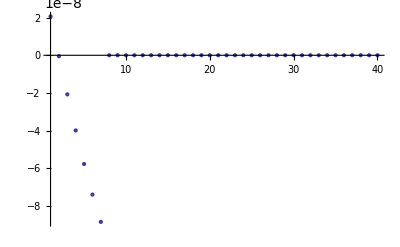

```mathematica
ListPlot[s-ss,PlotRange->All]
```

```mathematica
Length[s]
```

40

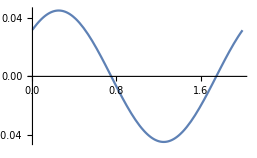

```mathematica
Plot[BesselJ[0,100Pi+x Pi],{x,0,2}]
```

```mathematica
With[{n_Integer},BesselI[0,n Pi]]
```

With::lvws: 局部变量指定 {n_Integer} 中的变量 n_Integer 需要一个值.

With[{n_Integer},BesselI[0,n π]]

```mathematica
BesselI[0,n Pi]
```

```mathematica
BesselI[0,1 π]
```

```mathematica
BesselK[0,π]*2//N
```

0.0590174

```mathematica
BesselJ[0,ⅈ Pi]//N
```

5.47784+0. ⅈ

```mathematica
NIntegrate[B]
```